```mathematica
ClearAll["Global`*"]
```

## SU(N) central charges

## a-maximization

```mathematica
FindCharges[nc_,n_,w_]:=Block[{$MaxExtraPrecision=100},Module[{(*Variables*)q,u,name,w2,μ,dim,mat,flatMat,abjSum,abjVarWrapped,abjVarBase,getMonomialCharge,termSum,v,baseVars,val,selectedVarBase,RRR,R,a,c,xVars,res,Hess,localmax,eqn,jacMatrix,rank,funds,pairs,indepVars,bestSol,ffields,rgio,opcharges,decouple,rcharge,uvar,uSum,uVarWrapped,uVarBase,iden,uassoc,central,global,rational,consistency,result,nsolve,time,finalResult,method,fterms,ringRelations,gio},

{time,finalResult }=AbsoluteTiming[

(*1. Inputs& Setup*)
name={"X","M","q","qb","phi","S","Sb","A","Ab"};
w2=ToExpression/@w;

(*Dynkin indices and dimensions*)
μ={0,0,1/2,1/2,nc,(nc+2)/2,(nc+2)/2,(nc-2)/2,(nc-2)/2};
dim={1,1,nc,nc,nc^2-1,(nc (nc+1))/2,(nc (nc+1))/2,(nc (nc-1))/2,(nc (nc-1))/2};

(*Generate matter field matrix functionally*)
mat=Table[ToExpression[name[[i]]<>ToString[j]],{i,Length[n]},{j,n[[i]]}];
flatMat=Flatten[mat];

method=<|"method"->"Exactly solved"|>;

Catch[
(*2. ABJ Anomaly Vanishing*)
abjSum=μ[[5]]+Sum[(q[mat[[i,j]]]-1) μ[[i]],{i,Length[μ]},{j,n[[i]]}];

abjVarWrapped=First[Variables[abjSum]];

(*Extract the base symbols from the q[...] wrappers*)
abjVarBase=abjVarWrapped/. q[sym_]:>sym;
q[abjVarBase]=abjVarWrapped/. First[Solve[abjSum==0,abjVarWrapped]];

(*Helper to extract R-charge from a superpotential monomial*)getMonomialCharge[monomial_]:=Total[Cases[Variables[monomial],var_:>Exponent[monomial,var]*q[var]]];

(*3. R-charge of superpotential terms should be 2*)
Do[
termSum=Expand[getMonomialCharge[term]];
If[termSum=!=2,
v=Variables[termSum];
If[Length[v]==0,Throw[<|"theory"->theory,"n"->n,"w"->w,"consistency"->"Superpotential not preserving R-symmetry."|>]
];

(*Extract the base symbols from the q[...] wrappers*)
baseVars=v/. q[sym_]:>sym;

(*Prioritize "X" or "M" fields if they exist in the term*)selectedVarBase=If[AnyTrue[baseVars,StringContainsQ[ToString[#],name[[1]]|name[[2]]]&],First[Select[baseVars,StringContainsQ[ToString[#],name[[1]]|name[[2]]]&]],First[baseVars]];

val=Solve[termSum==2,q[selectedVarBase]];

If[Length[val]==0,Throw[
<|"theory"->theory,"n"->n,"w"->w,"consistency"->"Superpotential not preserving R-symmetry"|>
],
q[selectedVarBase]=q[selectedVarBase]/. First[val];
];
],
{term,w2}
];

(*4. Central Charges*)
RRR=dim[[5]]+Sum[(q[mat[[i,j]]]-1)^3*dim[[i]],{i,Length[μ]},{j,n[[i]]}];
R=dim[[5]]+Sum[(q[mat[[i,j]]]-1)*dim[[i]],{i,Length[μ]},{j,n[[i]]}];
a=Expand[3 (3 RRR-R)/32];
c=Expand[(9 RRR-5 R)/32];

(*5. a-maximization*)
xVars=Variables[a];

(*Evaluate rank of Jacobian Matrix*)If[Length[xVars]===0,(*자유 변수가 하나도 없는 경우:행렬이 존재하지 않으므로 rank를 0으로 처리*)rank=0;,
(*정상적으로 자유 변수가 있는 경우:Jacobian 행렬 및 rank 계산*)eqn=D[a,{xVars}];
jacMatrix=D[eqn,{xVars}];
(*jacMatrix가 정상적인 2D 리스트(행렬)인지 한 번 더 방어적으로 체크*)If[MatrixQ[jacMatrix],rank=MatrixRank[jacMatrix];,rank=0; (*행렬 형태가 아니라면 안전하게 0으로 처리*)];];


If[Total[n]-Length[w]-1!=Length[xVars],
(*Print[w,"The number of variables doesn't match."];*)
Throw[<|"theory"->theory,"n"->n,"w"->w,"consistency"->"No unique solution of a-maximization"|>]
];

localmax={};

funds=Select[flatMat,StringStartsQ[ToString[#],"q"]&];


pairs=Values[GroupBy[funds,toGlobalGraph[Append[w,ToString[#]],n[[2]]]&]];

Scan[If[Length[#]>1,With[{targetVar=Last[#],restVar=Most[#]},Scan[With[{eq=(q[#]==q[targetVar])},If[eq=!=True,With[{vars=Variables[{q[#],q[targetVar]}]},If[Length[vars]>0,With[{solveVar=First[vars]},With[{sol=Solve[eq,solveVar]},(*핵심 2:Solve가 빈 룰({})을 반환할 때 자기 할당(x=x) 방지*)If[Length[sol]>0&&sol[[1]]=!={},
Scan[(q[#[[1]]/. q[sym_]:>sym]=#[[2]])&,sol[[1]]];
]]]]]]]&,restVar]]]&,pairs];

indepVars = Variables[xVars];

If[Length[indepVars]>0,
res=
Quiet[TimeConstrained[Simplify[TimeConstrained[Solve[(D[a,{#,1}]==0)&@indepVars,indepVars],3600,$NSolve]],3600,$NSolve]];
If[res=!=$NSolve,
(*다차원 평면(변수가 남은 식) 해는 버리고 고립된 점(Point) 해만 추출*)
res=Select[res,AllTrue[Values[#],NumericQ]&];
];

(*시간 초과*)
If[res===$NSolve,
method=<|"method"->"Numerically solved"|>;
res=TimeConstrained[
Quiet[
Check[
NSolve[Thread[D[a,{indepVars}]==0],indepVars,WorkingPrecision->50],
$Failed,
{NSolve::infsolns}
]
],
3600,
$Failed
];
];

(*시간 초과나 다른 이유로 해를 구하지 못한 경우*)
If[res===$Failed,Print[w];
Throw[<|"theory"->theory,"n"->n,"w"->w,"consistency"->"a-maximization timeout"|>]
];


Hess=D[a,{indepVars,2}];
localmax=Select[res,NegativeDefiniteMatrixQ[TimeConstrained[Simplify[Hess/. #],600,Hess/.#]]&];

If[Length[localmax]==0,Throw[Join[<|"theory"->theory,"n"->n,"w"->w,"consistency"->"a has no local maximum"|>]]
];

bestSol=Last[SortBy[localmax,(a/. #&)]];

(*Fix:#[[1]] is q[sym].Extract sym so we do q[sym]=value,not q[q[sym]]=value*)
Scan[(q[#[[1]]/. q[sym_]:>sym]=#[[2]])&,bestSol];
];

(*6. Realness& Consistency Checks*)If[!Element[N[SetPrecision[a,50]],Reals]||!Element[N[SetPrecision[c,50]],Reals]||!AllTrue[Values@localmax,Element[#,Reals]&],Throw[Join[<|"theory"->theory,"n"->n,"w"->w,"consistency"->"imaginary central charges"|>]]
];

(*If[!AllTrue[N[SetPrecision[Simplify[q[#]]&/@flatMat,50]],NumberQ],Throw[Join[<|"theory"->theory,"n"->n,"w"->w,"consistency"->"rcharge undetermined"|>,method]]
];*)

(*7. Operator Decoupling*)ffields=Join[ToExpression["M"<>ToString[#]]&/@Range[n[[2]]],ToExpression["X"<>ToString[#]]&/@Range[n[[1]]]];

fterms=Table[D[Total[w2],v],{v,flatMat}];
ringRelations=GroebnerBasis[fterms,flatMat];
gio=Flatten[Join[ffields,freeGIO,Flatten[Outer[Times,ffields,Join[freeGIO,ffields]]]]];
gio=Select[DeleteDuplicates[DeleteCases[(#[[2]]/. Times[c_?NumberQ,rest__]:>Times[rest])&/@PolynomialReduce[gio,ringRelations,flatMat],0]],#[[0]]=!=Plus&];

opcharges[expr_]:=expr/. {Times[arg1__,arg2__]:>Total[opcharges/@{arg1,arg2}],Power[base_,m_Integer]:>m N[SetPrecision[Simplify[q[base]],50]],sym_Symbol:>N[SetPrecision[Simplify[q[sym]],50]]};

decouple=Select[gio,opcharges[#]<=N[SetPrecision[2/3,50]]&];

(*
If[Length[decouple]>0,rcharge=AssociationThread[ToString/@flatMat->Expand[Simplify[q[#]]&/@flatMat]];
If[Min[Values[N[SetPrecision[rcharge,50]]]]<=0||Min[N[SetPrecision[{a,c},50]]]<=0||StringContainsQ[ToString[decouple[[1]]],"X"],Throw[<|"consistency"->"non-positive R-charges"|>],Throw[FindCharges[nc,n+{1,0,0,0,0,0,0,0,0},Append[w,"X"<>ToString[n[[1]]+1]<>"*"<>ToString[InputForm[decouple[[1]]]]]]]
]
];
*)

(*8. Outputs& Flavor Symmetry Mapping*)rcharge=AssociationThread[ToString/@flatMat->Expand[Simplify[q[#]]&/@flatMat]];

uvar=Flatten[u/@flatMat];

uSum=Sum[(u[mat[[i,j]]]) μ[[i]],{i,Length[μ]},{j,n[[i]]}];

uVarWrapped=First[Variables[uSum]];

uVarBase=uVarWrapped/. u[sym_]:>sym;

u[uVarBase]=uVarWrapped/. First[Solve[uSum==0,uVarWrapped]];

Do[termSum=Expand[Total[Cases[Variables[term],var_:>Exponent[term,var]*u[var]]]];

If[termSum=!=0,uVarWrapped=First[Variables[termSum]];
uVarBase=uVarWrapped/. u[sym_]:>sym;
u[uVarBase]=FullSimplify[uVarWrapped/. First[Solve[termSum==0,uVarWrapped]]];
],
{term,w2}
];


If[uvar=!=ConstantArray[0,Total[n]],uvar=uvar/. {0->ConstantArray[0,Length[Variables[uvar]]]};

v=Variables[uvar];

iden=IdentityMatrix[Length[v]];

Do[u[v[[i,1]]]=iden[[i]],{i,Length[v]}];

If[Length[iden]==1,
uvar=Flatten[uvar];
uvar={#}&/@(uvar*LCM@@Denominator/@uvar),uvar=Transpose[#*LCM@@Denominator[#]&/@Transpose[uvar]]
];
uassoc=AssociationThread[ToString/@flatMat->uvar],uassoc=AssociationThread[ToString/@flatMat->({#}&/@uvar)]
];

central=<|"a"->a,"c"->c|>;
rational=If[(SameQ[Rational,Head[Rationalize[a]]]||IntegerQ[Rationalize[a]])&&(SameQ[Rational,Head[Rationalize[c]]]||IntegerQ[Rationalize[c]]),
<|"rational"->Join[<|"a"->ToString[InputForm[Rationalize[a]]],"c"->ToString[InputForm[Rationalize[c]]]|>,AssociationThread[Keys[rcharge]->(ToString[InputForm[Rationalize[#]]]&/@Values[rcharge])]]|>,
<|"rational"->""|>
];

global=<|"global"->uassoc|>;

consistency=If[Min[Values[N[SetPrecision[rcharge,50]]]]<=0||Min[N[SetPrecision[{a,c},50]]]<=0||MemberQ[Values[N[SetPrecision[rcharge,50]]],2],
<|"consistency"->"non-positive R-charges"|>,
If[Length[decouple]>0,
<|"consistency"->"operator decoupled"|>
,
<|"consistency"->"consistent"|>
]
];

If[N[SetPrecision[c,50]]!=0&&(1/2>N[SetPrecision[a/c,50]]||N[SetPrecision[a/c,50]]>3/2),
consistency=<|"consistency"->"It violates Hofman-Maldacena bound"|>
];

(*Compile final results*)rgio=DeleteDuplicatesBy[gio,toGlobalGraph[Append[w,ToString[InputForm[#]]],n[[2]]]&];

result=Quiet[Join[<|"theory"->theory,"n"->n,"w"->w|>,consistency,method,N[SetPrecision[central,50],30],N[SetPrecision[rcharge,50],30],rational,global]];

Join[result,<|"inequiv_relevant"->Flatten[ToString[InputForm[#]]&/@Select[rgio,opcharges[#]<2&]]|>,<|"inequiv_flip"->Flatten[ToString[InputForm[#]]&/@Select[rgio,opcharges[#]<4/3&]],"all_relevant"->Flatten[ToString[InputForm[#]]&/@Select[Select[gio,#[[0]]=!=Plus&],opcharges[#]<2&]],"all_flip"->Flatten[ToString[InputForm[#]]&/@Select[Select[gio,#[[0]]=!=Plus&],opcharges[#]<4/3&]]|>]
]
];
Return[Join[finalResult,<|"computation_time"->time|>]];
]
]
```

## Superpotential to Graph (SET Field Contents)

```mathematica
(* superpotential to graph *)
toGlobalGraph[termList_List,maxM_]:=Module[{exprs,termNodes,varNodes,edges,g,anchorM,anchorQ,anchorT,allVars, chainNodes, portNode,varsQ,varsInTerm,portEdges,varsM},
varsM=Table[ToExpression["M"<>ToString[i]],{i,maxM}];
(*varsQ={q1,q2,q3,q4,qb1,qb2,qb3,qb4,q5,qb5};*)
varsQ={q1,q2,q3,q4,q5,q6,q7,q8,q9,q10};
exprs=ToExpression[termList];

(*Create unique IDs for Term Nodes*)(*We use indices 1,2,... to label the terms*)termNodes=Table[ToString[i]<>"_Term",{i,Length[exprs]}];

(*Build edges connecting Terms<->Variables*)edges=Flatten@MapIndexed[Function[{term,idx},Module[{factors,tNode},tNode=ToString[First@idx]<>"_Term";

(*Extract variables handling powers*)factors=If[Head[term]===Times,List@@term,{term}];
varsInTerm=Flatten[factors/. Power[x_,n_]:>ConstantArray[x,n]];

(*Create "Port Nodes" for every variable occurrence*)(*This avoids multiple edges between Term and Variable*)
portEdges={};
Do[portNode=ToString[First@idx]<>"_Port_"<>ToString[j];
AppendTo[portEdges,UndirectedEdge[ToString[First@idx]<>"_Term",portNode]];
AppendTo[portEdges,
UndirectedEdge[portNode,ToString[var]]];
,{j,Length[varsInTerm]},{var,{varsInTerm[[j]]}}];

(*Connect Term Node to Variable Nodes*)
portEdges
(*Join[portEdges,UndirectedEdge[tNode,ToString[#]]&/@varsInTerm]*)
]
],exprs
];


(*Add Anchors to enforce Group Constraints*)
anchorM="Anchor_M";
anchorQ="Anchor_Q";
anchorT="Anchor_Term";

(*Connect all specific variables to their group Anchor*)
edges=Join[edges,
UndirectedEdge[anchorM,ToString[#]]&/@varsM,UndirectedEdge[anchorQ,ToString[#]]&/@varsQ,(*All term nodes connect to a Term Anchor so they are structurally distinct from vars*)
UndirectedEdge[anchorT,#]&/@termNodes];

(*Add "Chains" to distinguish Anchors (No Loops!)*)(*AnchorM gets a 1-node appendage:M-X*)edges=Join[edges,{UndirectedEdge[anchorM,"TagM_1"]}];

(*AnchorQ gets a 2-node chain:Q-X-Y*)
edges=Join[edges,{UndirectedEdge[anchorQ,"TagQ_1"],UndirectedEdge["TagQ_1","TagQ_2"]}];

(*AnchorT gets a 3-node chain:T-X-Y-Z*)
edges=Join[edges,{UndirectedEdge[anchorT,"TagT_1"],UndirectedEdge["TagT_1","TagT_2"],UndirectedEdge["TagT_2","TagT_3"]}];

(*Return the canonical form*)
CanonicalGraph[Graph[edges]]
];
```

```mathematica
DistributeDefinitions[toGlobalGraph];
```

## WorkerFunction (SET N_c)

```mathematica
workerFunction[item_]:=Module[{res},
res=FindCharges[2, item[[1]], item[[2]]];
SafeUpsert[res];
res
];
DistributeDefinitions[workerFunction,FindCharges];
```

```mathematica
(* assign r-charges to operators *)
opcharge[theory_,expr_]:=expr/. {Times[a__,b__]:>Total[opcharge[theory,#]&/@{a,b}],Power[base_,n_Integer]:>n theory[ToString[base]],sym_Symbol:>theory[ToString[sym]]}
```

```mathematica
telegram:=URLExecute["https://api.telegram.org/bot<REDACTED>/sendMessage",{"chat_id"->"5926111332","text"->"Task completed"}];
```

## DB

```mathematica
(*1. 데이터베이스 패키지 로드*)
Needs["DatabaseLink`"];
```

```mathematica
(* ==========================================2. 데이터 변환 함수 (Association->DB Row)==========================================*)
TransformData[rawData_Association]:=Module[{knownKeys,wString,rCharges,repNames,repCounts,jsonPart,aCharge,cCharge,method,acRatio,rationality},(*R-charge 자동 분리:기본 키들을 제외한 나머지는 모두 R-charge로 간주*)knownKeys={"theory","n","w","consistency","method","a","c","rational","global","relevant","flip","computation_time"};
wString=StringRiffle[rawData["w"],"+"];
If[wString==="", wString="0"];

rCharges=KeyDrop[rawData,knownKeys];

(*n 리스트를 물리적 의미가 담긴 Association으로 매핑*)repNames={"X","M","q","qb","phi","S","Sb","A","Ab"};
(*repCounts=AssociationThread[repNames->rawData["n"]];*)

(*JSON으로 묶을 세부 데이터 구성*)
jsonPart=KeyDrop[rawData,{"theory","n","w","consistency","computation_time"}];

jsonPart=If[Length[jsonPart]===0,"{}",
<|"r_charges"->rCharges,"flavor_symmetry"->rawData["global"],"rational_exact"->rawData["rational"],"operators"-><|"inequiv_relevant"->rawData["inequiv_relevant"],"inequiv_flip"->rawData["inequiv_flip"],"all_relevant"->rawData["all_relevant"],"all_flip"->rawData["all_flip"]|>|>
];
method=Lookup[rawData,"method",Null];

aCharge = Lookup[rawData,"a",Null];
aCharge=If[aCharge===Null,Null,ToString[aCharge]];
cCharge = Lookup[rawData,"c",Null];
cCharge=If[cCharge===Null,Null,ToString[cCharge]];

If[aCharge=!=Null&&cCharge=!=Null&&cCharge=!=0,
acRatio=ToString[aCharge/cCharge];,
acRatio=Null;
];

rationality=Lookup[rawData,"rational",Null];
If[rationality=!=Null,
If[rationality=!="",
rationality=1;,
rationality=0;
];
];
(*DB 테이블의 각 Column에 들어갈 리스트 형태로 반환*)(*{theory,superpotential,consistency,a_charge,c_charge,data_json}*){rawData["theory"],wString,rawData["consistency"],aCharge,cCharge,acRatio,rationality,method,ExportString[jsonPart,"JSON","Compact"->True](*DB 용량 최적화를 위해 Compact 옵션 켬*),rawData["computation_time"] }];
```

```mathematica
(* ==========================================3. SQLite 데이터베이스 연결 및 테이블 생성==========================================*)
(*DB 파일 경로 설정 (원하시는 경로로 수정하세요)*)
dbPath=ExpandFileName[NotebookDirectory[]<>"4d_N1_SCFT_Database.sqlite"];
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];

(*테이블 생성 (최초 1회만 실행,이미 있으면 에러 무시됨)*)
SQLCreateTable[conn,"Theories",{SQLColumn["id","DataTypeName"->"INTEGER","PrimaryKey"->True],
SQLColumn["theory", "DataTypeName"->"TEXT"],
SQLColumn["superpotential", "DataTypeName"->"TEXT"],
SQLColumn["consistency","DataTypeName"->"TEXT"],
SQLColumn["a","DataTypeName"->"TEXT", "Nullable"->True],
SQLColumn["c","DataTypeName"->"TEXT", "Nullable"->True],
SQLColumn["ac_ratio","DataTypeName"->"TEXT", "Nullable"->True],
SQLColumn["rational_number", "DataTypeName"->"Integer", "Nullable"->True],
SQLColumn["method","DataTypeName"->"TEXT", "Nullable"->True],
SQLColumn["data_json","DataTypeName"->"TEXT", "Nullable"->True],
SQLColumn["computation_time", "DataTypeName"->"Real"],
SQLColumn["created_at", "DataTypeName"->"DATETIME"],
SQLColumn["updated_at", "DataTypeName"->"DATETIME"]
}];
CloseSQLConnection[conn];
```

JDBC::error: [SQLITE_ERROR] SQL error or missing database (table Theories already exists)

StringForm::sfr: Item 1 requested in "`1`" out of range; 0 items available.

JDBC::error: `1`

```mathematica
(* ==========================================
4. Upsert 함수
==========================================*)
UpsertTheory[conn_, rawData_]:=Module[{tName,wString,existingID,updateData,currentTime,rowData},
rowData=TransformData[rawData];

tName = rowData[[1]];
wString=rowData[[2]];

existingID=SQLExecute[conn,"SELECT id FROM Theories WHERE theory = `1` AND superpotential = `2`",{tName,wString}];

currentTime=DateString["ISODateTime"];

If[Length[existingID]>0,

SQLExecute[conn,"UPDATE Theories SET consistency = `1`,  a = `2`, c = `3`, ac_ratio = `4`, rational_number = `5`, method = `6`, data_json = `7`,computation_time = `8`, updated_at = `9` WHERE theory = `10` AND superpotential = `11`",{rowData[[3]],rowData[[4]],rowData[[5]],rowData[[6]],rowData[[7]],rowData[[8]],rowData[[9]],rowData[[10]],currentTime,tName,wString}];,

SQLExecute[conn,"INSERT INTO Theories (theory, superpotential, consistency, a, c, ac_ratio, rational_number, method, data_json,computation_time, created_at, updated_at) VALUES (`1`, `2`, `3`, `4`, `5`, `6`, `7`, `8`, `9`,`10`,`11`,`12`)",Join[rowData,{currentTime},{currentTime}]];
];
];
SafeUpsert[res_]:=UpsertTheory[conn,res];
SetSharedFunction[SafeUpsert];
```

## SU2nf4

## Import data

```mathematica
length0=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length0.wxf"];
length1=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length1.wxf"];
length2=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length2.wxf"];
length3=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length3.wxf"];
(*length4=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length4.wxf"];
length5=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length5.wxf"];*)
```

## Gauge Invariant Operators

```mathematica
theory="SU2_8q";
```

```mathematica
(* gauge-invariant operators *)
matter={q1,q2,q3,q4,q5,q6,q7,q8};
messon=(Times@@#)&/@Subsets[matter,{2}];
quartic=(Times@@#)&/@Tuples[messon,2];
freeGIO=Join[messon,quartic];
```

## Length0

```mathematica
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];
length0=Map[workerFunction,{{{0,0,8,0,0,0,0,0,0},{}}}];
%//Length
CloseSQLConnection[conn];
```

1

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length0.wxf",length0];
```

```mathematica
total=length0;
%//Length
```

1

## Length1

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["inequiv_relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["inequiv_flip"]}]],{ii,Select[length0,#["consistency"]=="consistent"&]}],1];
nw//Length
```

2

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

2

```mathematica
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];
length1=Map[workerFunction,rnw];
%//Length
CloseSQLConnection[conn];
```

2

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length1.wxf",length1];
```

```mathematica
length1=Select[length1,(!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}])&&#["consistency"]=="consistent"&];
%//Length
```

1

```mathematica
total=Join[length0,length1];
%//Length
```

2

## Length2

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["inequiv_relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["inequiv_flip"]}]],{ii,Select[length1,#["consistency"]=="consistent"&]}],1];
nw//Length
```

11

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

11

```mathematica
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];
length2=ParallelMap[workerFunction,rnw];
%//Length
CloseSQLConnection[conn];
```

11

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length2.wxf",length2];
```

```mathematica
length2=Select[length2,(!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}])&&#["consistency"]=="consistent"&];
%//Length
```

6

```mathematica
total=Join[length0,length1,length2];
%//Length
```

8

## Length3

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["inequiv_relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["inequiv_flip"]}]],{ii,Select[length2,#["consistency"]=="consistent"&]}],1];
nw//Length
```

158

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

125

```mathematica
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];
length3=ParallelMap[workerFunction,rnw];
%//Length
CloseSQLConnection[conn];
```

125

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length3.wxf",length3];
```

```mathematica
length3=Select[DeleteDuplicatesBy[length3,{#["a"],#["c"]}&],(!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}])&&#["consistency"]=="consistent"&];
%//Length
```

50

```mathematica
total=Join[length0,length1,length2,length3];
%//Length
```

58

## Length4

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["inequiv_relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["inequiv_flip"]}]],{ii,Select[length3,#["consistency"]=="consistent"&]}],1];
nw//Length
```

3510

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

2442

```mathematica
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];
length4=ParallelMap[workerFunction,rnw];
%//Length
CloseSQLConnection[conn];
```

2442

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length4.wxf",length4];
```

```mathematica
length4=Select[DeleteDuplicatesBy[length4,{#["a"],#["c"]}&],(!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}])&&#["consistency"]=="consistent"&];
%//Length
```

994

```mathematica
total=Join[length0,length1,length2,length3,length4];
%//Length
```

1052

## Length5

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["inequiv_relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["inequiv_flip"]}]],{ii,Select[length4,#["consistency"]=="consistent"&]}],1];
nw//Length
```

121978

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

76336

```mathematica
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];
length4=ParallelMap[workerFunction,rnw];
%//Length
CloseSQLConnection[conn];
```

76336

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length5.wxf",length4];
```

```mathematica
length5=Select[DeleteDuplicatesBy[length4,{#["a"],#["c"]}&],(!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}])&&#["consistency"]=="consistent"&];
%//Length
```

22720

```mathematica
total=Join[length0,length1,length2,length3,length4,length5];
%//Length
```

Join::heads: Heads List and Select at positions 1 and 6 are expected to be the same.

6

```mathematica
telegram;
```

## Distribution

```mathematica
Sort[Differences[SortBy[{#["a"],#["c"]}&/@total,#[[1]]&]]][[1]]
Position[Differences[SortBy[{#["a"],#["c"]}&/@total,#[[1]]&]],{%[[1]],%[[2]]}]
```

{0.,4.×10^-20}

{{10287}}

```mathematica
Sort[Differences[SortBy[{#["a"],#["c"]}&/@total,#[[1]]&]]][[2]]
Position[Differences[SortBy[{#["a"],#["c"]}&/@total,#[[1]]&]],{%[[1]],%[[2]]}]
SortBy[total,#["a"]&][[%[[1,1]]]]["a"]
SortBy[total,#["a"]&][[%%[[1,1]]]]["w"]
FindCharges[2,{0,2,4,4,0,0,0,0,0},{"M1*q1*q2","q3^2*q4^2","q3*qb1^2*qb2","M2*q4*qb3"}]
```

{4.×10^-20,2.×10^-19}

{{1532}}

0.75064588144087919931

{M1*q1*q2,q3^2*q4^2,q3*qb1^2*qb2,M2*q4*qb3,q3^2*q4*qb4}

<|w→{M1*q1*q2,q3^2*q4^2,q3*qb1^2*qb2,M2*q4*qb3},a→0.75255821372637802689,c→1.068439948922795394,M1→0.97306275642443348232,M2→0.9728294804328886437,q1→0.51346862178778325884,q2→0.51346862178778325884,q3→0.48629161653519796183,q4→0.51370838346480203817,qb1→0.51382493906355730323,qb2→0.4860585053376874317,qb3→0.51346213610230931813,qb4→0.45971717592087942925,consistency→consistent,global→<|M1→{0,1,1,1,1},M2→{0,-2,-1,-1,0},q1→{-1,-1,-1,-1,-1},q2→{1,0,0,0,0},q3→{0,-2,-1,0,0},q4→{0,2,1,0,0},qb1→{0,1,0,0,0},qb2→{0,0,1,0,0},qb3→{0,0,0,1,0},qb4→{0,0,0,0,1}|>,rational→,n→{0,2,4,4,0,0,0,0,0},relevant→{M1,M2,q1*q3,q1*q4,q1*qb1,q1*qb2,q1*qb3,q1*qb4,q3*q4,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb1,q4*qb2,q4*qb4,qb1*qb2,qb1*qb3,qb1*qb4,qb2*qb3,qb2*qb4,qb3*qb4,q1^2*q3^2,q1^2*q3*qb2,q1^2*q3*qb4,q1*q3^2*q4,q1*q3^2*qb1,q1*q3^2*qb2,q1*q3^2*qb3,q1*q3^2*qb4,q1*q3*q4*qb2,q1*q3*q4*qb4,q1*q3*qb1*qb4,q1*q3*qb2*qb3,q1*q3*qb2*qb4,q1*q3*qb3*qb4,q1*q4*qb2*qb4,q1*qb1*qb2*qb4,q1^2*qb2^2,q1^2*qb2*qb4,q1*q3*qb2^2,q1*q4*qb2^2,q1*qb1*qb2^2,q1*qb2^2*qb3,q1*qb2^2*qb4,q1*qb2*qb3*qb4,q1^2*qb4^2,q1*q3*qb4^2,q1*q4*qb4^2,q1*qb1*qb4^2,q1*qb2*qb4^2,q1*qb3*qb4^2,q3^2*q4*qb2,q3^2*q4*qb4,q3*q4^2*qb2,q3*q4^2*qb4,q3*q4*qb1*qb4,q3*q4*qb2*qb4,q3^2*qb1*qb2,q3^2*qb1*qb3,q3^2*qb1*qb4,q3*qb1*qb3*qb4,q3^2*qb2^2,q3^2*qb2*qb3,q3^2*qb2*qb4,q3*q4*qb2^2,q3*qb1*qb2^2,q3*qb2^2*qb3,q3*qb2^2*qb4,q3*qb2*qb3*qb4,q3^2*qb3^2,q3^2*qb3*qb4,q3*qb2*qb3^2,q3*qb3^2*qb4,q3^2*qb4^2,q3*q4*qb4^2,q3*qb2*qb4^2,q3*qb3*qb4^2,q4*qb1*qb2*qb4,q4^2*qb2^2,q4^2*qb2*qb4,q4*qb1*qb2^2,q4*qb2^2*qb4,q4^2*qb4^2,q4*qb1*qb4^2,q4*qb2*qb4^2,qb1^2*qb2^2,qb1^2*qb2*qb4,qb1*qb2^2*qb3,qb1*qb2^2*qb4,qb1*qb2*qb3*qb4,qb1^2*qb4^2,qb1*qb2*qb4^2,qb1*qb3*qb4^2,qb2^2*qb3^2,qb2^2*qb3*qb4,qb2*qb3^2*qb4,qb2^2*qb4^2,qb2*qb3*qb4^2,qb3^2*qb4^2,M1*q3*q4,M1*q3*qb1,M1*q3*qb2,M1*q3*qb3,M1*q3*qb4,M1*q4*qb2,M1*q4*qb4,M1*qb1*qb2,M1*qb1*qb4,M1*qb2*qb3,M1*qb2*qb4,M1*qb3*qb4,M1^2,M1*M2,M2*q1*q3,M2*q1*qb2,M2*q1*qb3,M2*q1*qb4,M2*q3*qb1,M2*q3*qb2,M2*q3*qb3,M2*q3*qb4,M2*qb1*qb2,M2*qb1*qb4,M2*qb2*qb3,M2*qb2*qb4,M2*qb3*qb4,M2^2},flip→{M1,M2,q1*q3,q1*q4,q1*qb1,q1*qb2,q1*qb3,q1*qb4,q3*q4,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb1,q4*qb2,q4*qb4,qb1*qb2,qb1*qb3,qb1*qb4,qb2*qb3,qb2*qb4,qb3*qb4}|>

```mathematica
%428["relevant"]//Length
```

132

```mathematica
{"qb2*qb4","q3*qb4","q3*qb2","M2","M1","q1*qb4","q2*qb4","q4*qb4","qb3*qb4","qb1*qb4","q2*q3","q2*qb2","q4*qb2","q3*qb3","qb2*qb3","q1*qb2","q1*q3","q3*q4","q3*qb1","qb1*qb2","q3*qb1","qb1*qb2","q2*qb3","q1*qb3","q2*qb1","q2*q4","qb1*qb3","q1*q4","q1*qb1","q4*qb1","q3*qb2*qb4^2","qb2^2*qb4^2","q3^2*qb4^2","q3*qb2^2*qb4","q3^2*qb2*qb4","M2*qb2*qb4","q1*qb2*qb4^2","M2*q3*qb4","q2*qb2*qb4^2","M1*q3*qb4","qb2*qb3*qb4^2","M1*qb2*qb4","q1*q3*qb4^2","q3*q4*qb4^2","q2*q3*qb4^2","qb1*qb2*qb4^2","q4*qb2*qb4^2","q3*qb3*qb4^2","q3*qb1*qb4^2","q3^2*qb2^2","M2*q3*qb2","q1*qb2^2*qb4","q2*qb2^2*qb4","M1*q3*qb2","qb2^2*qb3*qb4","M2^2","q1*q3^2*qb4","q1*q3*qb2*qb4","q2*q3*qb2*qb4","q2*q3^2*qb4","q3*q4*qb2*qb4","qb1*qb2^2*qb4","q4*qb2^2*qb4","q3*qb2*qb3*qb4","q3^2*qb3*qb4","M2*q1*qb4","M1*M2","q3*qb1*qb2*qb4","q3^2*qb1*qb4","M2*qb3*qb4","M2*q2*qb4","M1^2","q1^2*qb4^2","q1*qb3*qb4^2","M2*qb1*qb4","q1*q2*qb4^2","q2^2*qb4^2","q2*qb3*qb4^2","M1*q4*qb4","qb3^2*qb4^2","M1*qb3*qb4","q1*q4*qb4^2","q1*qb1*qb4^2","q2*qb1*qb4^2","q2*q4*qb4^2","qb1*qb3*qb4^2","M1*qb1*qb4","q4*qb3*qb4^2","qb1^2*qb4^2","q4*qb1*qb4^2","q4^2*qb4^2","q2*q3^2*qb2","q2*q3*qb2^2","q3*q4*qb2^2","q3^2*qb2*qb3","q3*qb2^2*qb3","q1*q3*qb2^2","q1*q3^2*qb2","M2*qb2*qb3","M2*q2*qb2","M2*q1*qb2","q1*qb2*qb3*qb4","M2*qb1*qb2","q1*q2*qb2*qb4","M2*q2*q3","M2*q1*q3","q1^2*qb2*qb4","q2^2*qb2*qb4","q2*qb2*qb3*qb4","M1*q4*qb2","M1*q3*qb3","qb2*qb3^2*qb4","M1*qb2*qb3","q1*q3*qb3*qb4","q1*qb1*qb2*qb4","M2*q3*qb1","q1*q2*q3*qb4","q1*q4*qb2*qb4","q1^2*q3*qb4","q2^2*q3*qb4","q2*qb1*qb2*qb4","q2*q4*qb2*qb4","q2*q3*qb3*qb4","M1*q3*q4","qb1*qb2*qb3*qb4","M1*qb1*qb2","q4*qb2*qb3*qb4","q3*qb3^2*qb4","q1*q3*qb1*qb4","q1*q3*q4*qb4","q2*q3*q4*qb4","q2*q3*qb1*qb4","qb1^2*qb2*qb4","q4*qb1*qb2*qb4","q4^2*qb2*qb4","M1*q3*qb1","q3*q4*qb3*qb4","q3*qb1*qb3*qb4","q3*q4*qb1*qb4","q2^2*qb2^2","q2*qb2^2*qb3","qb2^2*qb3^2","q1^2*qb2^2","q1*qb2^2*qb3","q1*q2*qb2^2","q2^2*q3*qb2","q2*qb1*qb2^2","q2*q4*qb2^2","q2*q3*qb2*qb3","qb1*qb2^2*qb3","q4*qb2^2*qb3","q3*qb2*qb3^2","q1^2*q3*qb2","q1*q3*qb2*qb3","q1*q2*q3*qb2","q1*qb1*qb2^2","q1*q4*qb2^2","q2*q3*qb1*qb2","q2^2*q3^2","M2*q2*qb3","q2*q3*q4*qb2","qb1^2*qb2^2","q4*qb1*qb2^2","q4^2*qb2^2","q3*qb1*qb2*qb3","q2*q3^2*qb3","q3*q4*qb2*qb3","q3^2*qb3^2","q1^2*q3^2","q1*q3^2*qb3","q1*q3*q4*qb2","q1*q2*q3^2","M2*q1*qb3","q1*q3*qb1*qb2"};
```

```mathematica
"M1*q1*q2","q3^2*q4^2","q3*qb1^2*qb2","M2*q4*qb3"
```

```mathematica
Complement[%428["relevant"],%431]
```

{M2*q3*qb3,q1*q3^2*q4,q1*q3^2*qb1,q3^2*q4*qb2,q3^2*q4*qb4,q3^2*qb1*qb2,q3^2*qb1*qb3,q3*q4^2*qb2,q3*q4^2*qb4,q3*q4*qb1*qb2,q3*qb1*qb2^2}

```mathematica
SortBy[total,#["a"]&][[10287]]["a"]
SortBy[total,#["a"]&][[10287]]["w"]
```

0.75255817889762083891

{M1*q1*q2,q3^2*q4*qb1,M2*q4*qb2,q3^2*qb1^2,M3*q3*qb3}

```mathematica
Charges30[2,{0,3,4,4,0,0,0,0,0},{"M1*q1*q2","q3^2*q4*qb1","M2*q4*qb2","q3^2*qb1^2","M3*q3*qb3"}]["a"]
Charges30[2,{0,3,4,4,0,0,0,0,0},{"M1*q1*q2","q3^2*q4*qb1","M2*q4*qb2","q3^2*qb1^2","M3*q3*qb3"}]["c"]
```

0.752558178897620838907083898128

1.0684398254703818953882809138

```mathematica
SortBy[total,#["a"]&][[10288]]["a"]
SortBy[total,#["a"]&][[10288]]["w"]
```

0.75255817889762083891

{M1*q1*q2,q3^2*q4*qb1,M2*q3*q4,M3*q3*qb2,M4*qb1*qb3}

```mathematica
Charges30[2,{0,4,4,4,0,0,0,0,0},{"M1*q1*q2","q3^2*q4*qb1","M2*q3*q4","M3*q3*qb2","M4*qb1*qb3"}]["a"]
Charges30[2,{0,4,4,4,0,0,0,0,0},{"M1*q1*q2","q3^2*q4*qb1","M2*q3*q4","M3*q3*qb2","M4*qb1*qb3"}]["c"]
```

0.752558178897620838911831029188

1.06843982547038189542982248801

```mathematica
%95-%93
```

4.74713106×10^-21

```mathematica
%96-%94
```

4.154157421×10^-20

```mathematica
SortBy[total,#["a"]&][[1]]
SortBy[total,#["a"]&][[-1]]
```

<|w→{},a→0.75,c→1.0625,q1→0.5,q2→0.5,q3→0.5,q4→0.5,qb1→0.5,qb2→0.5,qb3→0.5,qb4→0.5,consistency→consistent,global→<|q1→{-1,-1,-1,-1,-1,-1,-1},q2→{1,0,0,0,0,0,0},q3→{0,1,0,0,0,0,0},q4→{0,0,1,0,0,0,0},qb1→{0,0,0,1,0,0,0},qb2→{0,0,0,0,1,0,0},qb3→{0,0,0,0,0,1,0},qb4→{0,0,0,0,0,0,1}|>,rational→<|a→3/4,c→17/16,q1→1/2,q2→1/2,q3→1/2,q4→1/2,qb1→1/2,qb2→1/2,qb3→1/2,qb4→1/2|>,n→{0,0,4,4,0,0,0,0,0},relevant→{q1*q2},flip→{q1*q2}|>

<|w→{M1*q1*q2,M2*q1*q3,M3*q1*q4,M4*q1*qb1,M5*q1*qb2},a→0.79121710241585383623,c→1.1563869944371304086,M1→0.83145634553191496853,M2→0.83145634553191496853,M3→0.83145634553191496853,M4→0.83145634553191496853,M5→0.83145634553191496853,q1→0.68374084697764049286,q2→0.48480280749044453861,q3→0.48480280749044453861,q4→0.48480280749044453861,qb1→0.48480280749044453861,qb2→0.48480280749044453861,qb3→0.44612255778506840704,qb4→0.44612255778506840704,consistency→consistent,global→<|M1→{0,1,1,1,1,1,1},M2→{1,0,1,1,1,1,1},M3→{1,1,0,1,1,1,1},M4→{1,1,1,0,1,1,1},M5→{1,1,1,1,0,1,1},q1→{-1,-1,-1,-1,-1,-1,-1},q2→{1,0,0,0,0,0,0},q3→{0,1,0,0,0,0,0},q4→{0,0,1,0,0,0,0},qb1→{0,0,0,1,0,0,0},qb2→{0,0,0,0,1,0,0},qb3→{0,0,0,0,0,1,0},qb4→{0,0,0,0,0,0,1}|>,rational→,n→{0,5,4,4,0,0,0,0,0},relevant→{M1,q1*qb3,q2*q3,q2*qb3,qb3*qb4,q2^2*q3^2,q2^2*q3*q4,q2^2*q3*qb3,q2*q3*q4*qb1,q2*q3*q4*qb3,q2*q3*qb3*qb4,q2^2*qb3^2,q2^2*qb3*qb4,q2*q3*qb3^2,q2*qb3^2*qb4,qb3^2*qb4^2,M1*q2*q3,M1*q2*qb3,M1*q3*q4,M1*q3*qb3,M1*qb3*qb4,M1^2,M1*M2},flip→{M1,q1*qb3,q2*q3,q2*qb3,qb3*qb4},nsolve→exactly solved without Groebner|>

```mathematica
SortBy[total,#["a"]&][[49718]]
```

<|w→{M1*q1*q2,q3^2*q4^2,q1*qb1^2*qb2,q2*qb1*qb3*qb4,M2*q3*qb2,M3*qb3*qb4},a→0.75129617737527806322,c→1.0655205558556224078,M1→0.99981229845965476501,M2→0.97259765759879168964,M3→0.99999998825604403228,q1→0.50018771328430120271,q2→0.49999998825604403228,q3→0.52759005568550951307,q4→0.47240994431449048693,qb1→0.5,qb2→0.49981228671569879729,qb3→0.50000000587197798386,qb4→0.50000000587197798386,consistency→consistent,global→<|M1→{0,1,1,1},M2→{1,-1,0,0},M3→{0,0,-1,-1},q1→{0,-1,0,0},q2→{0,0,-1,-1},q3→{-1,0,0,0},q4→{1,0,0,0},qb1→{0,0,0,0},qb2→{0,1,0,0},qb3→{0,0,1,0},qb4→{0,0,0,1}|>,rational→,n→{0,3,4,4,0,0,0,0,0},relevant→{M1,M2,M3,q1*q3,q1*q4,q1*qb1,q1*qb2,q1*qb3,q2*q3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q3*q4,q3*qb1,q3*qb3,q4*qb1,q4*qb2,q4*qb3,qb1*qb2,qb1*qb3,qb2*qb3,q1^2*q2*q4,q1*q2^2*q4,q1*q2^2*qb2,q1^2*q4^2,q1^2*q4*qb1,q1^2*q4*qb2,q1^2*q4*qb3,q1*q3*q4^2,q1*q4^2*qb1,q1*q4^2*qb2,q1*q4^2*qb3,q1*q4*qb1*qb2,q1*q4*qb1*qb3,q1*q4*qb2*qb3,q1*q4*qb1^2,q1*q4*qb2^2,q1*qb1*qb2^2,q1*qb2^2*qb3,q1*q4*qb3^2,q2^2*q3*q4,q2*q3*q4*qb1,q2*q3*q4*qb3,q2^2*q4^2,q2^2*q4*qb1,q2^2*q4*qb2,q2^2*q4*qb3,q2*q3*q4^2,q2*q4^2*qb1,q2*q4^2*qb2,q2*q4^2*qb3,q2*q4*qb1*qb2,q2*q4*qb1*qb3,q2*q4*qb2*qb3,q2^2*qb1^2,q2^2*qb1*qb2,q2^2*qb1*qb3,q2*q4*qb1^2,q2*qb1^2*qb2,q2*qb1^2*qb3,q2*qb1*qb2*qb3,q2^2*qb2^2,q2^2*qb2*qb3,q2*q4*qb2^2,q2*qb1*qb2^2,q2*qb2^2*qb3,q2^2*qb3^2,q2*q4*qb3^2,q2*qb2*qb3^2,q3*q4^2*qb1,q3*q4^2*qb3,q3*q4*qb2^2,q4^2*qb1^2,q4^2*qb1*qb2,q4^2*qb1*qb3,q4*qb1^2*qb2,q4*qb1^2*qb3,q4*qb1*qb2*qb3,q4^2*qb2^2,q4^2*qb2*qb3,q4*qb1*qb2^2,q4*qb2^2*qb3,q4^2*qb3^2,q4*qb1*qb3^2,q4*qb2*qb3^2,q4*qb3^2*qb4,qb1^2*qb2^2,qb1^2*qb2*qb3,qb1*qb2^2*qb3,qb1*qb2*qb3^2,qb2^2*qb3^2,qb2*qb3^2*qb4,M1*q1*q4,M1*q1*qb2,M1*q2*q4,M1*q2*qb1,M1*q2*qb2,M1*q2*qb3,M1*q3*q4,M1*q4*qb1,M1*q4*qb2,M1*q4*qb3,M1*qb1*qb2,M1*qb1*qb3,M1*qb2*qb3,M1^2,M1*M2,M1*M3,M2*q1*q4,M2*q1*qb1,M2*q1*qb2,M2*q1*qb3,M2*q2*q4,M2*q2*qb1,M2*q2*qb2,M2*q2*qb3,M2*q3*q4,M2*q4*qb1,M2*q4*qb2,M2*q4*qb3,M2*qb1*qb2,M2*qb1*qb3,M2*qb2*qb3,M2^2,M2*M3,M3*q1*q4,M3*q1*qb2,M3*q2*q4,M3*q2*qb1,M3*q2*qb2,M3*q2*qb3,M3*q3*q4,M3*q4*qb1,M3*q4*qb2,M3*q4*qb3,M3*qb1*qb2,M3*qb1*qb3,M3*qb2*qb3,M3^2},flip→{M1,M2,M3,q1*q3,q1*q4,q1*qb1,q1*qb2,q1*qb3,q2*q3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q3*q4,q3*qb1,q3*qb3,q4*qb1,q4*qb2,q4*qb3,qb1*qb2,qb1*qb3,qb2*qb3},nsolve→exactly solved without Groebner|>

```mathematica
SortBy[total,#["a"]&][[49719]]
```

<|w→{M1*q1*q2,q3^2*q4^2,q3^2*qb1*qb2,M2*q1*qb1,M1*q2*q4,M3*qb3*qb4},a→0.75129617737527806323,c→1.0655205558556224079,M1→0.99999998825530910814,M2→0.97222223103018919801,M3→1.0001877250289921796,q1→0.50009385664215064389,q2→0.49990615510254024798,q3→0.49990614335784935611,q4→0.50009385664215064389,qb1→0.52768391232766015811,qb2→0.47250380095664112967,qb3→0.49990613748550391018,qb4→0.49990613748550391018,consistency→consistent,global→<|M1→{2,2,1,1},M2→{-3,-1,0,0},M3→{0,0,-1,-1},q1→{1,1,0,0},q2→{-3,-3,-1,-1},q3→{-1,-1,0,0},q4→{1,1,0,0},qb1→{2,0,0,0},qb2→{0,2,0,0},qb3→{0,0,1,0},qb4→{0,0,0,1}|>,rational→,n→{0,3,4,4,0,0,0,0,0},relevant→{M1,M2,M3,q1*q2,q1*q3,q1*q4,q1*qb2,q1*qb3,q2*q3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q3*q4,q3*qb1,q3*qb2,q3*qb3,q4*qb1,q4*qb2,q4*qb3,qb1*qb2,qb1*qb3,qb2*qb3,q1^2*q2*qb2,q1*q2^2*q3,q1*q2^2*qb2,q1*q2^2*qb3,q1*q2*q3*qb2,q1*q2*q3*qb3,q1*q2*q4*qb2,q1*q2*qb2*qb3,q1^2*q3*qb2,q1^2*q3*qb3,q1*q2*q3^2,q1*q3^2*qb2,q1*q3^2*qb3,q1*q3*q4*qb2,q1*q3*q4*qb3,q1*q3*qb2*qb3,q1^2*q4*qb2,q1*q4^2*qb2,q1*q4*qb2*qb3,q1^2*qb2^2,q1^2*qb2*qb3,q1*q2*qb2^2,q1*q3*qb2^2,q1*q4*qb2^2,q1*qb2^2*qb3,q1^2*qb3^2,q1*q2*qb3^2,q1*q3*qb3^2,q1*q4*qb3^2,q1*qb2*qb3^2,q1*qb3^2*qb4,q2^2*q3^2,q2^2*q3*q4,q2^2*q3*qb2,q2^2*q3*qb3,q2*q3^2*q4,q2*q3^2*qb2,q2*q3^2*qb3,q2*q3*q4*qb2,q2*q3*q4*qb3,q2*q3*qb2*qb3,q2^2*q4*qb2,q2^2*q4*qb3,q2*q4^2*qb2,q2*q4*qb2*qb3,q2^2*qb2^2,q2^2*qb2*qb3,q2*q3*qb2^2,q2*q4*qb2^2,q2*qb1*qb2^2,q2*qb2^2*qb3,q2^2*qb3^2,q2*q3*qb3^2,q2*q4*qb3^2,q2*qb2*qb3^2,q2*qb3^2*qb4,q3^2*q4*qb2,q3^2*q4*qb3,q3*q4^2*qb2,q3*q4^2*qb3,q3*q4*qb2*qb3,q3*qb1*qb2*qb3,q3^2*qb2^2,q3^2*qb2*qb3,q3*q4*qb2^2,q3*qb1*qb2^2,q3*qb2^2*qb3,q3^2*qb3^2,q3*q4*qb3^2,q3*qb2*qb3^2,q3*qb3^2*qb4,q4^2*qb2^2,q4^2*qb2*qb3,q4*qb1*qb2^2,q4*qb2^2*qb3,q4^2*qb3^2,q4*qb2*qb3^2,q4*qb3^2*qb4,qb1*qb2^2*qb3,qb1*qb2*qb3^2,qb2^2*qb3^2,qb2*qb3^2*qb4,M1*q1*q3,M1*q1*qb2,M1*q1*qb3,M1*q2*q3,M1*q2*qb2,M1*q2*qb3,M1*q3*q4,M1*q3*qb2,M1*q3*qb3,M1*q4*qb2,M1*q4*qb3,M1*qb2*qb3,M1^2,M1*M2,M2*q1*q2,M2*q1*q3,M2*q1*q4,M2*q1*qb2,M2*q1*qb3,M2*q2*q3,M2*q2*q4,M2*q2*qb1,M2*q2*qb2,M2*q2*qb3,M2*q3*q4,M2*q3*qb1,M2*q3*qb2,M2*q3*qb3,M2*q4*qb2,M2*q4*qb3,M2*qb1*qb2,M2*qb1*qb3,M2*qb2*qb3,M2^2,M2*M3,M3*q1*qb2,M3*q2*qb2,M3*q3*qb2,M3*q4*qb2},flip→{M1,M2,M3,q1*q2,q1*q3,q1*q4,q1*qb2,q1*qb3,q2*q3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q3*q4,q3*qb1,q3*qb2,q3*qb3,q4*qb1,q4*qb2,q4*qb3,qb1*qb2,qb1*qb3,qb2*qb3},nsolve→exactly solved without Groebner|>

```mathematica
Charges50[2,{0,2,4,4,0,0,0,0,0},{"M1*q1*q2","M2*q3*qb2","M3*qb3*qb4","q2*qb1*qb3*qb4","q1*qb1^2*qb2"}]
%["q3"]+%["q3"]+%["q4"]+%["q4"]
%%["q1"]+%%["qb1"]+%%["qb1"]+%%["qb2"]
%%%["q2"]+%%%["qb1"]+%%%["qb3"]+%%%["qb4"]
```

<|w→{M1*q1*q2,M2*q3*qb2,M3*qb3*qb4,q2*qb1*qb3*qb4,q1*qb1^2*qb2},a→0.75385542731693844439,c→1.0714642722686556632,M1→0.94569478967988329835,M2→0.9725636910926412015,q1→0.51278458548759803267,q2→0.54152062483251866898,q3→0.51352344896330146618,q4→0.45977910560504316883,qb1→0.48665127728417231751,qb2→0.51391285994405733232,qb3→0.48591404894165450676,qb4→0.48591404894165450676,consistency→consistent,global→<|M1→{0,3,1,1,1},M2→{1,-2,-1,0,0},q1→{0,-2,-1,0,0},q2→{0,-1,0,-1,-1},q3→{-1,2,0,0,0},q4→{1,0,0,0,0},qb1→{0,1,0,0,0},qb2→{0,0,1,0,0},qb3→{0,0,0,1,0},qb4→{0,0,0,0,1}|>,rational→,n→{0,2,4,4,0,0,0,0,0},relevant→{M1,M2,q1*qb1,q1*qb2,q1*qb3,q2*qb1,q2*qb2,q2*qb3,q3*qb1,q3*qb3,q4*qb1,q4*qb2,q4*qb3,q1^2*qb1^2,q1^2*qb1*qb3,q1*q3*qb1^2,q1*q3*qb1*qb3,q1*q4*qb1^2,q1*q4*qb1*qb2,q1*q4*qb1*qb3,q1*q4*qb2*qb3,q1^2*qb3^2,q1^2*qb3*qb4,q1*q3*qb3^2,q1*q3*qb3*qb4,q1*q4*qb3^2,q1*q4*qb3*qb4,q2*q4*qb1^2,q2*q4*qb1*qb3,q2*q4*qb3^2,q2*q4*qb3*qb4,q3^2*qb1*qb3,q3*q4*qb1^2,q3*q4*qb1*qb3,q3^2*qb3^2,q3^2*qb3*qb4,q3*q4*qb3^2,q3*q4*qb3*qb4,q4^2*qb1^2,q4^2*qb1*qb2,q4^2*qb1*qb3,q4^2*qb2^2,q4^2*qb2*qb3,q4^2*qb3^2,q4^2*qb3*qb4,M1*q1*qb1,M1*q1*qb2,M1*q1*qb3,M1*q2*qb1,M1*q2*qb3,M1*q3*qb1,M1*q3*qb3,M1*q4*qb1,M1*q4*qb2,M1*q4*qb3,M1^2,M1*M2,M2*q1*qb1,M2*q1*qb3,M2*q2*qb3,M2*q3*qb1,M2*q3*qb3,M2*q4*qb1,M2*q4*qb3,M2^2},flip→{M1,M2,q1*qb1,q1*qb2,q1*qb3,q2*qb1,q2*qb2,q2*qb3,q3*qb1,q3*qb3,q4*qb1,q4*qb2,q4*qb3},nsolve→exactly solved without Groebner|>

1.94660510913668927

2.

2.

```mathematica
Charges50[2,{0,2,4,4,0,0,0,0,0},{"M1*q1*q2","q3^2*q4^2","q1*qb1^2*qb2","q2*qb1*qb3*qb4","M2*q3*qb2"}]
2/3+%["qb3"]+%["qb4"]
```

<|w→{M1*q1*q2,q3^2*q4^2,q1*qb1^2*qb2,q2*qb1*qb3*qb4,M2*q3*qb2},a→0.7530394799854272748,c→1.0695930913710052923,M1→0.96287978679939879272,M2→0.97226243103135292672,q1→0.49984786562605809123,q2→0.53727234757454311605,q3→0.52758543459470516451,q4→0.47241456540529483549,qb1→0.5,qb2→0.50015213437394190877,qb3→0.48136382621272844198,qb4→0.48136382621272844198,consistency→consistent,global→<|M1→{0,1,1,1},M2→{1,-1,0,0},q1→{0,-1,0,0},q2→{0,0,-1,-1},q3→{-1,0,0,0},q4→{1,0,0,0},qb1→{0,0,0,0},qb2→{0,1,0,0},qb3→{0,0,1,0},qb4→{0,0,0,1}|>,rational→,n→{0,2,4,4,0,0,0,0,0},relevant→{M1,M2,q1*qb1,q1*qb2,q1*qb3,q2*qb1,q2*qb2,q2*qb3,q3*qb1,q3*qb3,q4*qb1,q4*qb2,q4*qb3,q1^2*qb1^2,q1^2*qb1*qb2,q1^2*qb1*qb3,q1*q4*qb1^2,q1*q4*qb1*qb2,q1*q4*qb1*qb3,q1^2*qb2*qb3,q1*q4*qb2^2,q1*q4*qb2*qb3,q1^2*qb3^2,q1^2*qb3*qb4,q1*q3*qb3^2,q1*q3*qb3*qb4,q1*q4*qb3^2,q1*q4*qb3*qb4,q2*q4*qb2*qb3,q2*q4*qb3^2,q2*q4*qb3*qb4,q3*q4*qb1*qb3,q3*q4*qb3^2,q3*q4*qb3*qb4,q4^2*qb1^2,q4^2*qb1*qb2,q4^2*qb1*qb3,q4^2*qb2^2,q4^2*qb2*qb3,q4^2*qb3^2,q4^2*qb3*qb4,M1*q1*qb1,M1*q1*qb2,M1*q1*qb3,M1*q2*qb3,M1*q3*qb1,M1*q3*qb3,M1*q4*qb1,M1*q4*qb2,M1*q4*qb3,M1^2,M1*M2,M2*q1*qb1,M2*q1*qb2,M2*q1*qb3,M2*q2*qb3,M2*q3*qb1,M2*q3*qb3,M2*q4*qb1,M2*q4*qb2,M2*q4*qb3,M2^2},flip→{M1,M2,q1*qb1,q1*qb2,q1*qb3,q2*qb1,q2*qb2,q2*qb3,q3*qb1,q3*qb3,q4*qb1,q4*qb2,q4*qb3},nsolve→exactly solved without Groebner|>

1.6293943190921235506

```mathematica
Charges50[2,{0,2,4,4,0,0,0,0,0},{"M1*q1*q2","q3^2*q4^2","q3^2*qb1*qb2","M2*q1*qb1","M1*q2*q4"}]
2/3+%["qb3"]+%["qb4"]
```

<|w→{M1*q1*q2,q3^2*q4^2,q3^2*qb1*qb2,M2*q1*qb1,M1*q2*q4},a→0.754289207292810503,c→1.0724754112516630584,M1→0.96372031478498222313,M2→0.94530042187337689009,q1→0.51346099168327975282,q2→0.52281869353173802405,q3→0.48653900831672024718,q4→0.51346099168327975282,qb1→0.54123858644334335709,qb2→0.48568339692321614855,qb3→0.46839916570921135875,qb4→0.46839916570921135875,consistency→consistent,global→<|M1→{2,2,1,1},M2→{-3,-1,0,0},q1→{1,1,0,0},q2→{-3,-3,-1,-1},q3→{-1,-1,0,0},q4→{1,1,0,0},qb1→{2,0,0,0},qb2→{0,2,0,0},qb3→{0,0,1,0},qb4→{0,0,0,1}|>,rational→,n→{0,2,4,4,0,0,0,0,0},relevant→{M1,M2,q1*qb2,q1*qb3,q2*qb1,q2*qb2,q2*qb3,q3*qb1,q3*qb2,q3*qb3,q4*qb1,q4*qb2,q4*qb3,q1^2*qb2^2,q1^2*qb2*qb3,q1*q2*qb2*qb3,q1*q3*qb2^2,q1*q3*qb2*qb3,q1*q4*qb2^2,q1*q4*qb2*qb3,q1^2*qb3^2,q1^2*qb3*qb4,q1*q2*qb3^2,q1*q2*qb3*qb4,q1*q3*qb3^2,q1*q3*qb3*qb4,q1*q4*qb3^2,q1*q4*qb3*qb4,q2^2*qb2*qb3,q2*q3*qb2^2,q2*q3*qb2*qb3,q2*q4*qb2*qb3,q2^2*qb3^2,q2^2*qb3*qb4,q2*q3*qb3^2,q2*q3*qb3*qb4,q2*q4*qb3^2,q2*q4*qb3*qb4,q3^2*qb2^2,q3^2*qb2*qb3,q3*q4*qb2^2,q3*q4*qb2*qb3,q3^2*qb3^2,q3^2*qb3*qb4,q3*q4*qb3^2,q3*q4*qb3*qb4,q4^2*qb2^2,q4^2*qb2*qb3,q4^2*qb3^2,q4^2*qb3*qb4,M1*q1*qb2,M1*q1*qb3,M1*q2*qb2,M1*q2*qb3,M1*q3*qb1,M1*q3*qb2,M1*q3*qb3,M1*q4*qb2,M1*q4*qb3,M1^2,M1*M2,M2*q1*qb2,M2*q1*qb3,M2*q2*qb2,M2*q2*qb3,M2*q3*qb1,M2*q3*qb2,M2*q3*qb3,M2*q4*qb2,M2*q4*qb3,M2^2},flip→{M1,M2,q1*qb2,q1*qb3,q2*qb1,q2*qb2,q2*qb3,q3*qb1,q3*qb2,q3*qb3,q4*qb1,q4*qb2,q4*qb3},nsolve→exactly solved without Groebner|>

1.6034649980850893842

```mathematica
Sort[Differences[SortBy[{#["a"],#["c"]}&/@total,#[[1]]&]]][[5]]
```

{4.6×10^-18,4.×10^-17}

```mathematica
Position[Differences[SortBy[{#["a"],#["c"]}&/@total,#[[1]]&]],{4.55749830276494805454`2.4796788467876234*^-18,3.996526020860738507608`3.2694852546837057*^-17}]
```

{{17291}}

```mathematica
Position[Differences[SortBy[{#["a"],#["c"]}&/@total,#[[1]]&]],{0``19.822429924259495,4.154157420655109451`0.28870288659293447*^-20}]
```

{{10287}}

```mathematica
Min[Differences[#["a"]&/@SortBy[total,#["a"]&]]]
```

0.

```mathematica
Min[Differences[#["c"]&/@SortBy[total,#["c"]&]]]
```

4.×10^-20

```mathematica
Position[Differences[#["a"]&/@SortBy[total,#["a"]&]],Min[Differences[#["a"]&/@SortBy[total,#["a"]&]]]]
```

{{153}}

```mathematica
SortBy[total,#["a"]&][[153]]["a"]
SortBy[total,#["a"]&][[153]]["w"]
```

0.75129660656448921474

{M1*q1*q2,q3^2*q4^2,q1*qb1^2*qb2,M2*qb3*qb4}

```mathematica
SortBy[total,#["a"]&][[154]]["a"]
SortBy[total,#["a"]&][[154]]["w"]
```

0.75129660656449260187

{M1*q1*q2,q3^2*q4*qb1,M2*q4*qb2,M3*qb3*qb4}

```mathematica
SortBy[total,#["a"]&][[-1]]
```

<|w→{M1*q1*q2,M2*q1*q3,M3*q1*q4,M4*q1*qb1,M5*q1*qb2},a→0.79121710241585383623,c→1.1563869944371304086,M1→0.83145634553191496853,M2→0.83145634553191496853,M3→0.83145634553191496853,M4→0.83145634553191496853,M5→0.83145634553191496853,q1→0.68374084697764049286,q2→0.48480280749044453861,q3→0.48480280749044453861,q4→0.48480280749044453861,qb1→0.48480280749044453861,qb2→0.48480280749044453861,qb3→0.44612255778506840704,qb4→0.44612255778506840704,consistency→consistent,global→<|M1→{0,1,1,1,1,1,1},M2→{1,0,1,1,1,1,1},M3→{1,1,0,1,1,1,1},M4→{1,1,1,0,1,1,1},M5→{1,1,1,1,0,1,1},q1→{-1,-1,-1,-1,-1,-1,-1},q2→{1,0,0,0,0,0,0},q3→{0,1,0,0,0,0,0},q4→{0,0,1,0,0,0,0},qb1→{0,0,0,1,0,0,0},qb2→{0,0,0,0,1,0,0},qb3→{0,0,0,0,0,1,0},qb4→{0,0,0,0,0,0,1}|>,rational→,n→{0,5,4,4,0,0,0,0,0},relevant→{M1,q1*qb3,q2*q3,q2*qb3,qb3*qb4,q2^2*q3^2,q2^2*q3*q4,q2^2*q3*qb3,q2*q3*q4*qb1,q2*q3*q4*qb3,q2*q3*qb3*qb4,q2^2*qb3^2,q2^2*qb3*qb4,q2*q3*qb3^2,q2*qb3^2*qb4,qb3^2*qb4^2,M1*q2*q3,M1*q2*qb3,M1*q3*q4,M1*q3*qb3,M1*qb3*qb4,M1^2,M1*M2},flip→{M1,q1*qb3,q2*q3,q2*qb3,qb3*qb4},nsolve→exactly solved without Groebner|>

```mathematica
SortBy[total,#["a"]&][[-2]]
```

<|w→{M1*q1*q2,q3^2*q4^2,M2*q1*q3,M3*q1*q4,M4*q1*qb1,M5*q1*qb2},a→0.79062118877175821596,c→1.1549025214823781739,M1→0.84210217177586034277,M2→0.82259608065124982201,M3→0.82259608065124982201,M4→0.84210217177586034277,M5→0.84210217177586034277,q1→0.67740391934875017799,q2→0.48049390887538947924,q3→0.5,q4→0.5,qb1→0.48049390887538947924,qb2→0.48049390887538947924,qb3→0.44055717701254069214,qb4→0.44055717701254069214,consistency→consistent,global→<|M1→{0,0,1,1,1,1},M2→{1,1,1,1,1,1},M3→{1,-1,1,1,1,1},M4→{1,0,0,1,1,1},M5→{1,0,1,0,1,1},q1→{-1,0,-1,-1,-1,-1},q2→{1,0,0,0,0,0},q3→{0,-1,0,0,0,0},q4→{0,1,0,0,0,0},qb1→{0,0,1,0,0,0},qb2→{0,0,0,1,0,0},qb3→{0,0,0,0,1,0},qb4→{0,0,0,0,0,1}|>,rational→,n→{0,5,4,4,0,0,0,0,0},relevant→{M1,M2,q1*qb3,q2*q3,q2*qb1,q2*qb3,q3*q4,q3*qb3,qb3*qb4,q1*qb3^2*qb4,q2^2*q3^2,q2^2*q3*q4,q2^2*q3*qb1,q2^2*q3*qb3,q2*q3^2*q4,q2*q3^2*qb1,q2*q3^2*qb3,q2*q3*q4*qb1,q2*q3*q4*qb3,q2*q3*qb1*qb2,q2*q3*qb1*qb3,q2*q3*qb3*qb4,q2^2*qb1^2,q2^2*qb1*qb2,q2^2*qb1*qb3,q2*qb1*qb2*qb3,q2*qb1*qb3*qb4,q2^2*qb3^2,q2^2*qb3*qb4,q2*q3*qb3^2,q2*qb1*qb3^2,q2*qb3^2*qb4,q3^2*q4*qb3,q3*q4*qb3*qb4,q3^2*qb3^2,q3^2*qb3*qb4,q3*q4*qb3^2,q3*qb3^2*qb4,qb3^2*qb4^2,M1*q2*q3,M1*q2*qb1,M1*q2*qb3,M1*q3*q4,M1*q3*qb1,M1*q3*qb3,M1*qb1*qb2,M1*qb1*qb3,M1*qb3*qb4,M1^2,M1*M2,M1*M4,M2*q1*qb3,M2*q2*q3,M2*q2*q4,M2*q2*qb1,M2*q2*qb3,M2*q3*q4,M2*q3*qb3,M2*q4*qb3,M2*qb3*qb4,M2^2,M2*M3},flip→{M1,M2,q1*qb3,q2*q3,q2*qb1,q2*qb3,q3*q4,q3*qb3,qb3*qb4},nsolve→exactly solved without Groebner|>

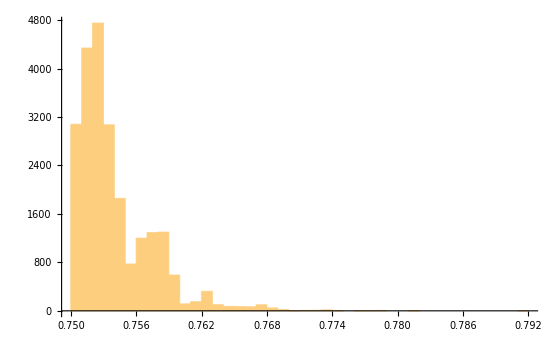

```mathematica
Histogram[#["a"]&/@total,{0.001},PlotRange->Full]
```

```mathematica
data={#["c"],#["a"]}&/@total;
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[0.2886503858267340717+0.43418819458895124841 x]

```mathematica
{intercept, slope}=lm["BestFitParameters"]
```

{0.2886503858267340717,0.43418819458895124841}

```mathematica
verticalDistances=lm["FitResiduals"];
```

```mathematica
orthogonalDistances=Map[Abs[#[[2]]-(slope*#[[1]]+intercept)]/Sqrt[slope^2+1]&,data];
```

```mathematica
binSize=0.0000005
```

5.×10^-7

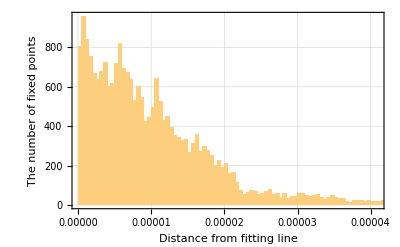

```mathematica
Histogram[orthogonalDistances,{binSize},PlotTheme->"Detailed",FrameLabel->{"Distance from fitting line","The number of fixed points"}]
```

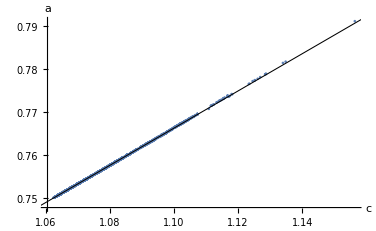

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@total,PlotRange->All,AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005]];
p2=Plot[intercept+slope  x,{x,1,1.2},PlotStyle->{Black,Thickness->0.002}];
Show[p1,p2]
```

```mathematica
SU2nf4=SortBy[import,#["CentralChargeA"]&]
```

Dataset[<>]

```mathematica
SU2nf4[[1]]["CentralChargeA"]
```

0.691186

```mathematica
SU2nf41=Select[SU2nf4,Length[Association[ToExpression[StringReplace[#["Rcharges"],{"["->"{","]"->"}",":"->"->"}]]][M]]==1&]
```

Dataset[<>]

```mathematica
Show[ListPlot[{#["c"],#["a"]}&/@total,PlotRange->All,AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}]]]
```

-Graphics-

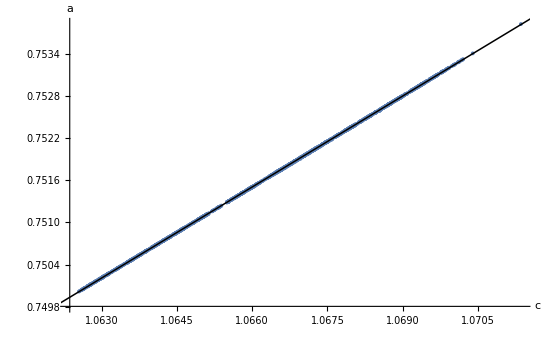

```mathematica
p1=ListPlot[{#["CentralChargeC"],#["CentralChargeA"]}&/@SU2nf41,PlotRange->All,AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005]];
p2=Plot[0.2922893556065832+0.4307835955550063 x,{x,1,1.2},PlotStyle->{Black,Thickness->0.002}];
Show[p1,p2]
```

```mathematica
SU2nf4[[-1]]
```

```mathematica
Clear[x]
```

```mathematica
{#["CentralChargeA"],#["CentralChargeC"]}&/@import[[2;;-2]]//Normal
```

```mathematica
MinimalBy[Select[Differences[{#["CentralChargeA"],#["CentralChargeC"]}&/@DeleteDuplicatesBy[SU2nf4[[2;;-2]],#["SCI"]&]//Sort],#[[1]]!=0&],#[[1]]&][[1]][[1]]//Normal
```

2.22045×10^-16

```mathematica
0.4965+2 0.4887+0.4995
3%
```

1.9734

5.9202

```mathematica
Position[Differences[{#["CentralChargeA"]}&/@DeleteDuplicatesBy[SU2nf4[[2;;-2]],#["SCI"]&]//Sort],2.220446049250313*^-16]
```

{{3730,1}}

```mathematica
SortBy[DeleteDuplicatesBy[SU2nf4[[2;;-2]],#["SCI"]&],#["CentralChargeA"]&][[3730]]["Superpotentials"]
SortBy[DeleteDuplicatesBy[SU2nf4[[2;;-2]],#["SCI"]&],#["CentralChargeA"]&][[3730]]["CentralChargeA"]
SortBy[DeleteDuplicatesBy[SU2nf4[[2;;-2]],#["SCI"]&],#["CentralChargeA"]&][[3730]]["SCI"]//ToExpression
SortBy[DeleteDuplicatesBy[SU2nf4[[2;;-2]],#["SCI"]&],#["CentralChargeA"]&][[3731]]["Superpotentials"]
SortBy[DeleteDuplicatesBy[SU2nf4[[2;;-2]],#["SCI"]&],#["CentralChargeA"]&][[3731]]["CentralChargeA"]
SortBy[DeleteDuplicatesBy[SU2nf4[[2;;-2]],#["SCI"]&],#["CentralChargeA"]&][[3731]]["SCI"]//ToExpression
%-%%%%
%%%-%%%%%%
```

[M1*q2*q3, q1*q4*qb2^2, qb1^2*qb2^2]

0.753072

t^2.805+t^2.871+6 t^2.903+3 t^2.934+2 t^2.968+3 t^3.+4 t^3.033+6 t^3.065+2 t^3.13+t^5.61+t^5.676+6 t^5.708+3 t^5.739+t^5.741+8 t^5.773+24 t^5.805+16 t^5.837+2 t^5.839+6 t^5.869+12 t^5.871+16 t^5.903+4 t^5.904+5 t^5.934+24 t^5.935+3 t^5.936+36 t^5.967+16 t^5.999-11 t^6.+8 t^6.001-6 t^6.032+24 t^6.033+16 t^6.065+6 t^6.066+16 t^6.097+4 t^6.099+18 t^6.129-4 t^6.162+6 t^6.163+9 t^6.195+3 t^6.261+t^8.415+t^8.481+6 t^8.513+3 t^8.544+t^8.547+8 t^8.578+24 t^8.61+t^8.612+16 t^8.642+8 t^8.644+6 t^8.674+33 t^8.676+72 t^8.708+2 t^8.71+56 t^8.739+15 t^8.741+30 t^8.771+40 t^8.773+4 t^8.774+10 t^8.803+42 t^8.805+24 t^8.806+3 t^8.807+18 t^8.837+84 t^8.838+12 t^8.839+7 t^8.869+124 t^8.87-18 t^8.871+8 t^8.872+84 t^8.901-80 t^8.903+48 t^8.904+4 t^8.905+30 t^8.933-65 t^8.934+100 t^8.935+6 t^8.936-16 t^8.966+80 t^8.967+12 t^8.968+12 t^8.969+24 t^8.999+t^8.676/y+(6 t^8.708)/y+(3 t^8.739)/y+(8 t^8.773)/y+(21 t^8.805)/y+(18 t^8.837)/y+(4 t^8.838)/y+(2 t^8.839)/y+(3 t^8.869)/y+(6 t^8.87)/y+(15 t^8.871)/y+(24 t^8.903)/y+(4 t^8.904)/y+(9 t^8.934)/y+(32 t^8.935)/y+t^8.936/y+(48 t^8.967)/y+(6 t^8.968)/y+(18 t^8.999)/y+t^8.676 y+6 t^8.708 y+3 t^8.739 y+8 t^8.773 y+21 t^8.805 y+18 t^8.837 y+4 t^8.838 y+2 t^8.839 y+3 t^8.869 y+6 t^8.87 y+15 t^8.871 y+24 t^8.903 y+4 t^8.904 y+9 t^8.934 y+32 t^8.935 y+t^8.936 y+48 t^8.967 y+6 t^8.968 y+18 t^8.999 y

[M1*q2*q3, q1*q4*qb2^2, qb1^2*qb2^2, M2*q1*q4]

0.753072

t^2.805+2 t^2.87+t^2.871+t^2.934+6 t^2.935+4 t^2.967+3 t^3.+2 t^3.032+2 t^3.066+6 t^3.097+t^5.61+2 t^5.675+t^5.676+4 t^5.739+8 t^5.74+t^5.741+4 t^5.772+2 t^5.804+13 t^5.805+6 t^5.806+8 t^5.837+t^5.869+6 t^5.87+23 t^5.871+8 t^5.901+24 t^5.903+9 t^5.934+14 t^5.935+2 t^5.936+2 t^5.966+24 t^5.967+6 t^5.999-9 t^6.+10 t^6.001+6 t^6.032+32 t^6.033+3 t^6.064+16 t^6.065+2 t^6.066+14 t^6.097+9 t^6.129-6 t^6.13+3 t^6.131-4 t^6.162+10 t^6.163+18 t^6.195+t^8.415+2 t^8.48+t^8.481+4 t^8.544+8 t^8.545+t^8.547+4 t^8.577+6 t^8.609+16 t^8.61+8 t^8.611+t^8.612+8 t^8.642+4 t^8.674+20 t^8.675+33 t^8.676+6 t^8.677+16 t^8.707+24 t^8.708+2 t^8.738+19 t^8.739+44 t^8.74+23 t^8.741+14 t^8.771+48 t^8.772+t^8.803+18 t^8.804+2 t^8.805+64 t^8.806+2 t^8.807+8 t^8.836+42 t^8.837+80 t^8.838+21 t^8.869+26 t^8.87+32 t^8.871+10 t^8.872+2 t^8.9+28 t^8.901+92 t^8.903+12 t^8.933+47 t^8.934-70 t^8.935+32 t^8.936+12 t^8.966-16 t^8.967+100 t^8.968+3 t^8.998+34 t^8.999+(2 t^8.675)/y+t^8.676/y+(2 t^8.739)/y+(8 t^8.74)/y+(4 t^8.772)/y+(2 t^8.804)/y+(16 t^8.805)/y+(6 t^8.806)/y+(10 t^8.837)/y+(4 t^8.838)/y+(12 t^8.87)/y+(20 t^8.871)/y+(8 t^8.901)/y+(32 t^8.903)/y+(9 t^8.934)/y+(22 t^8.935)/y+(2 t^8.936)/y+(2 t^8.966)/y+(36 t^8.967)/y+(6 t^8.968)/y+(8 t^8.999)/y+2 t^8.675 y+t^8.676 y+2 t^8.739 y+8 t^8.74 y+4 t^8.772 y+2 t^8.804 y+16 t^8.805 y+6 t^8.806 y+10 t^8.837 y+4 t^8.838 y+12 t^8.87 y+20 t^8.871 y+8 t^8.901 y+32 t^8.903 y+9 t^8.934 y+22 t^8.935 y+2 t^8.936 y+2 t^8.966 y+36 t^8.967 y+6 t^8.968 y+8 t^8.999 y

2 t^2.87-6 t^2.903-2 t^2.934+6 t^2.935+4 t^2.967-2 t^2.968+2 t^3.032-4 t^3.033-6 t^3.065+2 t^3.066+6 t^3.097-2 t^3.13+2 t^5.675-6 t^5.708+t^5.739+8 t^5.74+4 t^5.772-8 t^5.773+2 t^5.804-11 t^5.805+6 t^5.806-8 t^5.837-2 t^5.839-5 t^5.869+6 t^5.87+11 t^5.871+8 t^5.901+8 t^5.903-4 t^5.904+4 t^5.934-10 t^5.935-t^5.936+2 t^5.966-12 t^5.967-10 t^5.999+2 t^6.+2 t^6.001+12 t^6.032+8 t^6.033+3 t^6.064-4 t^6.066-2 t^6.097-4 t^6.099-9 t^6.129-6 t^6.13+3 t^6.131+4 t^6.163+9 t^6.195-3 t^6.261+2 t^8.48-6 t^8.513+t^8.544+8 t^8.545+4 t^8.577-8 t^8.578+6 t^8.609-8 t^8.61+8 t^8.611-8 t^8.642-8 t^8.644-2 t^8.674+20 t^8.675+6 t^8.677+16 t^8.707-48 t^8.708-2 t^8.71+2 t^8.738-37 t^8.739+44 t^8.74+8 t^8.741-16 t^8.771+48 t^8.772-40 t^8.773-4 t^8.774-9 t^8.803+18 t^8.804-40 t^8.805+40 t^8.806-t^8.807+8 t^8.836+24 t^8.837-4 t^8.838-12 t^8.839+14 t^8.869-98 t^8.87+50 t^8.871+2 t^8.872+2 t^8.9-56 t^8.901+172 t^8.903-48 t^8.904-4 t^8.905-18 t^8.933+112 t^8.934-170 t^8.935+26 t^8.936+28 t^8.966-96 t^8.967+88 t^8.968-12 t^8.969+3 t^8.998+10 t^8.999+(2 t^8.675)/y-(6 t^8.708)/y-t^8.739/y+(8 t^8.74)/y+(4 t^8.772)/y-(8 t^8.773)/y+(2 t^8.804)/y-(5 t^8.805)/y+(6 t^8.806)/y-(8 t^8.837)/y-(2 t^8.839)/y-(3 t^8.869)/y+(6 t^8.87)/y+(5 t^8.871)/y+(8 t^8.901)/y+(8 t^8.903)/y-(4 t^8.904)/y-(10 t^8.935)/y+t^8.936/y+(2 t^8.966)/y-(12 t^8.967)/y-(10 t^8.999)/y+2 t^8.675 y-6 t^8.708 y-t^8.739 y+8 t^8.74 y+4 t^8.772 y-8 t^8.773 y+2 t^8.804 y-5 t^8.805 y+6 t^8.806 y-8 t^8.837 y-2 t^8.839 y-3 t^8.869 y+6 t^8.87 y+5 t^8.871 y+8 t^8.901 y+8 t^8.903 y-4 t^8.904 y-10 t^8.935 y+t^8.936 y+2 t^8.966 y-12 t^8.967 y-10 t^8.999 y

2.22045×10^-16

```mathematica
Charges50[2,{0,1,4,4,0,0,0,0,0},{"M1*q2*q3", "q1*q4*qb2^2", "qb1^2*qb2^2"}]
```

<|w→{M1*q2*q3,q1*q4*qb2^2,qb1^2*qb2^2},a→0.753072,c→1.06963,M1→0.935019,q1→0.489055,q2→0.53249,q3→0.53249,q4→0.489055,qb1→0.489055,qb2→0.510945,qb3→0.478455,qb4→0.478455,consistency→consistent,global→<|M1→{0,0,-2,1,1},q1→{0,-1,-2,0,0},q2→{-1,0,2,-1,-1},q3→{1,0,0,0,0},q4→{0,1,0,0,0},qb1→{0,0,-1,0,0},qb2→{0,0,1,0,0},qb3→{0,0,0,1,0},qb4→{0,0,0,0,1}|>,rational→,n→{0,1,4,4,0,0,0,0,0}|>

```mathematica
Charges50[2,{0,2,4,4,0,0,0,0,0},{"M1*q2*q3", "q1*q4*qb2^2", "qb1^2*qb2^2", "M2*q1*q4"}]
```

<|w→{M1*q2*q3,q1*q4*qb2^2,qb1^2*qb2^2,M2*q1*q4},a→0.753072,c→1.06963,M1→0.956909,M2→0.97811,q1→0.510945,q2→0.521545,q3→0.521545,q4→0.510945,qb1→0.510945,qb2→0.489055,qb3→0.46751,qb4→0.46751,consistency→consistent,global→<|M1→{0,0,-2,1,1},M2→{0,0,2,0,0},q1→{0,-1,-2,0,0},q2→{-1,0,2,-1,-1},q3→{1,0,0,0,0},q4→{0,1,0,0,0},qb1→{0,0,-1,0,0},qb2→{0,0,1,0,0},qb3→{0,0,0,1,0},qb4→{0,0,0,0,1}|>,rational→,n→{0,2,4,4,0,0,0,0,0}|>

```mathematica
0.7530716232149125-0.7530716232149125
```

0.

## SU2nf5

## Import data

```mathematica
su210qlen0=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length0.wxf"];
su210qlen1=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length1.wxf"];
su210qlen2=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length2.wxf"];
su210qlen3=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length3.wxf"];
su210qlen4=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length4.wxf"];
su210qlen5=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length5.wxf"];
```

## Gauge Invariant Operators

```mathematica
theory="SU2_10q";
```

```mathematica
(* gauge-invariant operators *)
matter={q1,q2,q3,q4,q5,q6,q7,q8,q9,q10};
messon=(Times@@#)&/@Subsets[matter,{2}];
quartic=(Times@@#)&/@Tuples[messon,2];
freeGIO=Join[messon,quartic];
```

## Length0

```mathematica
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];
su210qlen0=Map[workerFunction,{{{0,0,10,0,0,0,0,0,0},{}}}];
%//Length
CloseSQLConnection[conn];
```

1

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length0.wxf",su210qlen0];
```

```mathematica
total=su210qlen0;
%//Length
```

1

## Length1

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["inequiv_relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["inequiv_flip"]}]],{ii,Select[su210qlen0,#["consistency"]=="consistent"&]}],1];
nw//Length
```

2

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

2

```mathematica
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];
su210qlen1=Map[workerFunction,rnw];
%//Length
CloseSQLConnection[conn];
```

2

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length1.wxf",su210qlen1];
```

```mathematica
su210qlen1=Select[su210qlen1,(!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}])&&#["consistency"]=="consistent"&];
%//Length
```

1

```mathematica
total=Join[su210qlen0,su210qlen1];
%//Length
```

2

## Length2

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["inequiv_relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["inequiv_flip"]}]],{ii,Select[su210qlen1,#["consistency"]=="consistent"&]}],1];
nw//Length
```

8

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

8

```mathematica
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];
su210qlen2=Map[workerFunction,rnw];
%//Length
CloseSQLConnection[conn];
```

8

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length2.wxf",su210qlen2];
```

```mathematica
su210qlen2=Select[su210qlen2,(!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}])&&#["consistency"]=="consistent"&];
%//Length
```

4

```mathematica
total=Join[su210qlen0,su210qlen1,su210qlen2];
%//Length
```

6

## Length3

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["inequiv_relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["inequiv_flip"]}]],{ii,Select[su210qlen2,#["consistency"]=="consistent"&]}],1];
nw//Length
```

47

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

39

```mathematica
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];
su210qlen3=Map[workerFunction,rnw];
%//Length
CloseSQLConnection[conn];
```

39

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length3.wxf",su210qlen3];
```

```mathematica
su210qlen3=Select[su210qlen3,(!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}])&&#["consistency"]=="consistent"&];
%//Length
```

18

```mathematica
total=Join[su210qlen0,su210qlen1,su210qlen2,su210qlen3];
%//Length
```

24

## Length4

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["inequiv_relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["inequiv_flip"]}]],{ii,Select[su210qlen3,#["consistency"]=="consistent"&]}],1];
nw//Length
```

324

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

244

```mathematica
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];
su210qlen4=Map[workerFunction,rnw];
%//Length
CloseSQLConnection[conn];
```

244

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length4.wxf",su210qlen4];
```

```mathematica
su210qlen4=Select[su210qlen4,(!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}])&&#["consistency"]=="consistent"&];
%//Length
```

106

```mathematica
total=Join[su210qlen0,su210qlen1,su210qlen2,su210qlen3,su210qlen4];
%//Length
```

130

## Length5

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["inequiv_relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["inequiv_flip"]}]],{ii,Select[su210qlen4,#["consistency"]=="consistent"&]}],1];
nw//Length
```

3389

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

2314

```mathematica
conn=OpenSQLConnection[JDBC["SQLite",dbPath]];
su210qlen5=Map[workerFunction,rnw];
%//Length
CloseSQLConnection[conn];
```

0

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length5.wxf",su210qlen5];
```

```mathematica
su210qlen5=Select[su210qlen5,(!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}])&&#["consistency"]=="consistent"&];
%//Length
```

0

```mathematica
total=Join[su210qlen0,su210qlen1,su210qlen2,su210qlen3,su210qlen4,su210qlen5];
%//Length
```

2

```mathematica
telegram;
```

## Distribution

```mathematica
su2nf5total//Length
```

715

```mathematica
su2nf5total=Select[su2nf5total,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
```

715

```mathematica
Sort[Differences[SortBy[{#["a"],#["c"]}&/@su2nf5total,#[[1]]&]]][[1]]
Position[Differences[SortBy[{#["a"],#["c"]}&/@su2nf5total,#[[1]]&]],{%[[1]],%[[2]]}]
```

{3.7603869744×10^-9,1.8350312319×10^-8}

{{104}}

```mathematica
SortBy[su2nf5total,#["a"]&][[104]]["a"]
SortBy[su2nf5total,#["a"]&][[104]]["c"]
SortBy[su2nf5total,#["a"]&][[104]]["w"]
```

0.7599852322869549511

1.0855408954588342622

{M1*q1*q2,M1*q3*q4,q1*q5,q2^2*q6*q7,M2*q2*q3}

```mathematica
SortBy[su2nf5total,#["a"]&][[105]]["a"]
SortBy[su2nf5total,#["a"]&][[105]]["c"]
SortBy[su2nf5total,#["a"]&][[105]]["w"]
```

0.75998523604734192547

1.0855409138091465816

{M1*q1*q2,M1*q3*q4,q1*q5,M2*q2*q3,q2*q4*q6^2}

```mathematica
%125-%122
%126-%123
```

3.7603869744×10^-9

1.8350312319×10^-8

```mathematica
SortBy[su2nf5total,#["a"]&][[1]]
SortBy[su2nf5total,#["a"]&][[-1]]
```

<|w→{M1*q1*q2,M1*q3*q4,M2*q1*q5,M2*q3*q6,q2*q5},a→0.70087754178396489993,c→1.0507189563632598048,M1→0.70126868336564076089,M2→0.70126868336564076089,q1→0.29873131663435923911,q2→1.,q3→0.72770667697832702884,q4→0.57102463965603221027,q5→1.,q6→0.57102463965603221027,q7→0.45787818176881232788,q8→0.45787818176881232788,q9→0.45787818176881232788,q10→0.45787818176881232788,consistency→consistent,global→<|M1→{-1,2,-1,0,0,0},M2→{-1,0,-1,0,0,0},q1→{1,-1,1,0,0,0},q2→{0,-1,0,0,0,0},q3→{1,0,0,0,0,0},q4→{0,-2,1,0,0,0},q5→{0,1,0,0,0,0},q6→{0,0,1,0,0,0},q7→{0,0,0,1,0,0},q8→{0,0,0,0,1,0},q9→{0,0,0,0,0,1},q10→{-2,3,-3,-1,-1,-1}|>,rational→,n→{0,2,10,0,0,0,0,0,0},relevant→{M1,q1*q2,q1*q3,q1*q4,q1*q7,q2*q3,q2*q4,q2*q6,q2*q7,q3*q4,q3*q7,q4*q6,q4*q7,q7*q8,q1^2*q3*q4,q1^2*q3*q7,q1*q3*q7*q8,q1^2*q4^2,q1^2*q4*q6,q1^2*q4*q7,q1*q4^2*q7,q1*q4*q6*q7,q1*q4*q7*q8,q1^2*q7^2,q1^2*q7*q8,q1*q3*q7^2,q1*q4*q7^2,q1*q7^2*q8,q1*q7*q8*q9,q4*q7^2*q8,q4*q7*q8*q9,q7^2*q8^2,q7^2*q8*q9,q10*q7*q8*q9,M1*q1*q4,M1*q1*q6,M1*q1*q7,M1*q4*q6,M1*q4*q7,M1*q6*q7,M1*q7*q8,M1^2,M1*M2},flip→{M1,q1*q2,q1*q3,q1*q4,q1*q7,q3*q4,q3*q7,q4*q6,q4*q7,q7*q8}|>

<|w→{M1*q1*q2,M2*q1*q3,M3*q1*q4,M4*q1*q5,M5*q1*q6},a→1.0477806596317209597,c→1.4488898141299123214,M1→0.71645070560578764245,M2→0.71645070560578764245,M3→0.71645070560578764245,M4→0.71645070560578764245,M5→0.71645070560578764245,q1→0.6846399951119890395,q2→0.59890929928222331805,q3→0.59890929928222331805,q4→0.59890929928222331805,q5→0.59890929928222331805,q6→0.59890929928222331805,q7→0.58020337711922359256,q8→0.58020337711922359256,q9→0.58020337711922359256,q10→0.58020337711922359256,consistency→consistent,global→<|M1→{1,0,1,1,1,1,1,1,1},M2→{1,1,0,1,1,1,1,1,1},M3→{1,1,1,0,1,1,1,1,1},M4→{1,1,1,1,0,1,1,1,1},M5→{1,1,1,1,1,0,1,1,1},q1→{-1,-1,-1,-1,-1,-1,-1,-1,-1},q2→{0,1,0,0,0,0,0,0,0},q3→{0,0,1,0,0,0,0,0,0},q4→{0,0,0,1,0,0,0,0,0},q5→{0,0,0,0,1,0,0,0,0},q6→{0,0,0,0,0,1,0,0,0},q7→{0,0,0,0,0,0,1,0,0},q8→{0,0,0,0,0,0,0,1,0},q9→{0,0,0,0,0,0,0,0,1},q10→{1,0,0,0,0,0,0,0,0}|>,rational→,n→{0,5,10,0,0,0,0,0,0},relevant→{M1,q1*q7,q2*q3,q2*q7,q7*q8,M1*q2*q3,M1*q2*q7,M1*q3*q4,M1*q3*q7,M1*q7*q8,M1^2,M1*M2},flip→{M1,q1*q7,q2*q3,q2*q7,q7*q8}|>

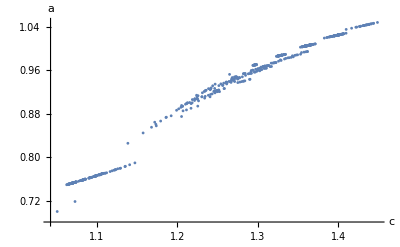

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@su2nf5total,PlotRange->All,AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005]];
Show[p1]
```

### protected

```mathematica
su3nf6totalnoX=Select[su3nf6total,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&&#["consistency"]=="consistent"&];
```

```mathematica
su3Wgraph=toGlobalGraph[#["w"],#["n"][[2]]]&/@su3nf6totalnoX;
su2Wgraph=toGlobalGraph[#["w"],#["n"][[2]]]&/@total;
```

```mathematica
su2Wprotected=Select[total,MemberQ[su3Wgraph,toGlobalGraph[#["w"],#["n"][[2]]]]&];
%//Length
```

4158

```mathematica
su3Wprotected=Select[su3nf6totalnoX,MemberQ[su2Wgraph,toGlobalGraph[#["w"],#["n"][[2]]]]&];
%//Length
```

4158

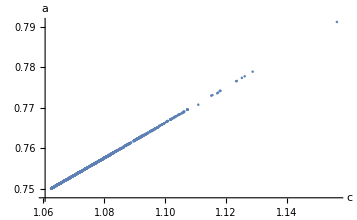

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@Select[su2Wprotected,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],PlotRange->All,AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005],PlotRange->{{1.062,1.157},{0.75,0.792}}];
p2=ListPlot[{#["c"],#["a"]}&/@Select[Complement[total,su2Wprotected],!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->{PointSize[0.005],Red}];
Show[p1]
```

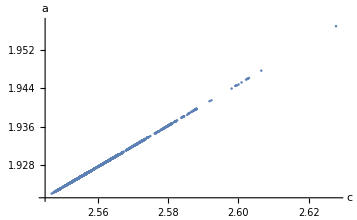

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@Select[su3Wprotected,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005],PlotRange->{{2.545,2.628},{1.921,1.958}}];
p2=ListPlot[{#["c"],#["a"]}&/@Select[Complement[su3nf6totalnoX,su3Wprotected],!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->{PointSize[0.005],Red},PlotRange->All];
Show[p1]
```

```mathematica
Select[Complement[su3nf6totalnoX,su3Wprotected],#["c"]<2.5469&][[112]]
```

<|w→{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb2,q3*qb2,M3*q2*qb1},a→1.3385546140307950698,c→1.9497301582665615803,M1→1.1105956461138679159,M2→0.93369649717066913256,M3→1.1768991489431987834,q1→0.4487386226863189095,q2→0.38243511985698804206,q3→1.3824351198569880421,q4→0.38973721803669712484,q5→0.38973721803669712484,q6→0.38973721803669712484,qb1→0.44066573119981317457,qb2→0.61756488014301195794,qb3→0.38973721803669712484,qb4→0.38973721803669712484,qb5→0.38973721803669712484,qb6→0.38973721803669712484,consistency→consistent,global→<|M1→{1,1,1,0,-1,1,1,1,1},M2→{1,1,1,1,-2,1,1,1,1},M3→{0,0,0,-1,1,0,0,0,0},q1→{-1,-1,-1,-1,1,-1,-1,-1,-1},q2→{0,0,0,0,-1,0,0,0,0},q3→{0,0,0,0,-1,0,0,0,0},q4→{1,0,0,0,0,0,0,0,0},q5→{0,1,0,0,0,0,0,0,0},q6→{0,0,1,0,0,0,0,0,0},qb1→{0,0,0,1,0,0,0,0,0},qb2→{0,0,0,0,1,0,0,0,0},qb3→{0,0,0,0,0,1,0,0,0},qb4→{0,0,0,0,0,0,1,0,0},qb5→{0,0,0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,0,0,1}|>,rational→,n→{0,3,6,6,0,0,0,0,0},relevant→{M1,M2,M3,q1*qb3,q2*qb3,q3*qb1,q3*qb3,q4*qb1,q4*qb3,q1^2*qb1*qb3,q1*q2*qb1^2,q1*q4*qb1^2,q1^2*qb3^2,q1^2*qb3*qb4,q1*q2*qb3^2,q1*q2*qb3*qb4,q1*q4*qb3^2,q1*q4*qb3*qb4,q2^2*qb1*qb3,q2*q4*qb1^2,q2^2*qb3^2,q2^2*qb3*qb4,q2*q4*qb3^2,q2*q4*qb3*qb4,q4^2*qb1^2,q4^2*qb1*qb3,q4*q5*qb1^2,q4*q5*qb1*qb3,q4^2*qb3^2,q4^2*qb3*qb4,q4*q5*qb3*qb4,M1*q1*qb3,M1*q2*qb3,M1*q4*qb1,M1*q4*qb3,M2*q1*qb3,M2*q2*qb3,M2*q4*qb1,M2*q4*qb3,M2^2,M3*q2*qb3,M3*q4*qb3},flip→{M1,M2,M3,q1*qb3,q2*qb3,q4*qb1,q4*qb3}|>

```mathematica
FindCharges[2,{0,3,4,4,0,0,0,0,0},{"M1*q1*qb1","q2^2*qb2^2","M2*q1*qb2","q3*qb2","M3*q2*qb1"}]
```

<|w→{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb2,q3*qb2,M3*q2*qb1,q2*qb3*X1,q2*qb4*X2},a→0.23684833425881484985,c→0.4653528404505985334,X1→1.4276667611233189722,X2→1.4276667611233189722,M1→1.2442971893424115594,M2→0.84478596710259334974,M3→1.3995112222398182097,q1→0.40507918938392314138,q2→0.24986515648651649112,q3→1.2498651564865164911,q4→0.34949586807556599499,qb1→0.35062362127366529918,qb2→0.75013484351348350888,qb3→0.32246808239016453667,qb4→0.32246808239016453667,consistency→consistent,global→<|X1→{0,0,0,1,0},X2→{0,0,0,0,1},M1→{1,0,1,-1,0},M2→{1,1,0,-1,-1},M3→{0,-1,1,0,1},q1→{-1,-1,-1,1,0},q2→{0,0,-1,0,-1},q3→{0,0,-1,0,-1},q4→{1,0,0,0,0},qb1→{0,1,0,0,0},qb2→{0,0,1,0,1},qb3→{0,0,1,-1,1},qb4→{0,0,1,0,0}|>,rational→,n→{2,3,4,4,0,0,0,0,0},relevant→{M1,M2,M3,X1,q1*qb3,q3*qb1,q3*qb3,q4*qb1,q4*qb3,q1^2*qb1*qb3,q1*q2*qb1^2,q1*q4*qb1^2,q1^2*qb3^2,q1^2*qb3*qb4,q1*q2*qb3^2,q1*q4*qb3^2,q1*q4*qb3*qb4,q2^2*qb1*qb3,q2*q4*qb1^2,q2^2*qb3*qb4,q2*q4*qb3^2,q4^2*qb1^2,q4^2*qb1*qb3,q4^2*qb3^2,q4^2*qb3*qb4,M1*q1*qb3,M1*q4*qb1,M1*q4*qb3,M2*q1*qb3,M2*q4*qb1,M2*q4*qb3,M2*q2^2*qb3*qb4,M2^2},flip→{M1,M2,q1*qb3,q4*qb1,q4*qb3,q1*q2*qb3^2,q2^2*qb1*qb3,q2*q4*qb1^2,q2^2*qb3*qb4,q2*q4*qb3^2}|>

```mathematica
Sort[Differences[SortBy[{#["a"],#["c"]}&/@su3Wprotected,#[[1]]&]]][[1]]
Position[Differences[SortBy[{#["a"],#["c"]}&/@su3Wprotected,#[[1]]&]],{%[[1]],%[[2]]}]
```

{3.4×10^-17,2.11×10^-16}

{{3908}}

```mathematica
SortBy[su3Wprotected,#["a"]&][[3908]]["a"]
SortBy[su3Wprotected,#["a"]&][[3908]]["c"]
SortBy[su3Wprotected,#["a"]&][[3908]]["w"]
```

1.9336923360254912712

2.5742385278274092053

{M1*q1*qb1,q2^2*qb2*qb3,M2*q2*qb1,q1*q3*qb2*qb3,M3*q1*qb4}

```mathematica
SortBy[su3Wprotected,#["a"]&][[3909]]["a"]
SortBy[su3Wprotected,#["a"]&][[3909]]["c"]
SortBy[su3Wprotected,#["a"]&][[3909]]["w"]
```

1.9336923360254913053

2.5742385278274094164

{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb2,q2^2*qb1*qb3,M3*q3*qb1}

```mathematica
Select[su3Wprotected,#["a"]==1.92557907068431444020021424192468181343`20.&]
```

{}

```mathematica
FindCharges[3,{0,3,6,6,0,0,0,0,0},{"M1*q1*qb1","q2^2*qb2*qb3","M2*q3*qb2","q2^2*qb3^2","M3*q2^2*"}]
```

<|w→{M1*q1*qb1,q2^2*qb2*qb3,M2*q3*qb2,q2^2*qb3^2},a→1.9255790706843144402,c→2.5555072711314834549,M1→0.95292443056541212614,M2→0.96822436227988363866,q1→0.52353778471729393693,q2→0.49218433956077073274,q3→0.52395997728088709407,q4→0.48685813214088262747,q5→0.48685813214088262747,q6→0.48685813214088262747,qb1→0.52353778471729393693,qb2→0.50781566043922926726,qb3→0.50781566043922926726,qb4→0.48685813214088262747,qb5→0.48685813214088262747,qb6→0.48685813214088262747,consistency→consistent,global→<|M1→{1,1,1,1,0,1,1,1,1},M2→{-1,0,0,0,0,-1,0,0,0},q1→{-1,-1,-1,-1,-1,-1,-1,-1,-1},q2→{0,0,0,0,0,-1,0,0,0},q3→{1,0,0,0,0,0,0,0,0},q4→{0,1,0,0,0,0,0,0,0},q5→{0,0,1,0,0,0,0,0,0},q6→{0,0,0,1,0,0,0,0,0},qb1→{0,0,0,0,1,0,0,0,0},qb2→{0,0,0,0,0,1,0,0,0},qb3→{0,0,0,0,0,1,0,0,0},qb4→{0,0,0,0,0,0,1,0,0},qb5→{0,0,0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,0,0,1}|>,rational→,n→{0,2,6,6,0,0,0,0,0},relevant→{M1,M2,q1*qb2,q1*qb3,q1*qb4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*qb1,q3*qb3,q3*qb4,q4*qb2,q4*qb3,q4*qb4,q1*q2*qb4^2,q1*q2*qb4*qb5,q1*q4*qb4^2,q1*q4*qb4*qb5,q2^2*qb1*qb4,q2^2*qb2*qb4,q2*q4*qb2^2,q2*q4*qb2*qb3,q2*q4*qb2*qb4,q2^2*qb3*qb4,q2*q4*qb3^2,q2*q4*qb3*qb4,q2^2*qb4^2,q2^2*qb4*qb5,q2*q3*qb4^2,q2*q3*qb4*qb5,q2*q4*qb4^2,q2*q4*qb4*qb5,q3*q4*qb4^2,q3*q4*qb4*qb5,q4^2*qb2^2,q4^2*qb2*qb3,q4^2*qb2*qb4,q4*q5*qb2^2,q4*q5*qb2*qb3,q4*q5*qb2*qb4,q4^2*qb3^2,q4^2*qb3*qb4,q4*q5*qb3^2,q4*q5*qb3*qb4,q4^2*qb4^2,q4^2*qb4*qb5,q4*q5*qb4*qb5,M1*q2*qb2,M1*q2*qb3,M1*q2*qb4,M1*q3*qb3,M1*q3*qb4,M1*q4*qb2,M1*q4*qb3,M1*q4*qb4,M1^2,M1*M2,M2*q1*qb3,M2*q1*qb4,M2*q2*qb1,M2*q2*qb3,M2*q2*qb4,M2*q3*qb4,M2*q4*qb3,M2*q4*qb4,M2^2},flip→{M1,M2,q1*qb2,q1*qb3,q1*qb4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*qb1,q3*qb3,q3*qb4,q4*qb2,q4*qb3,q4*qb4}|>

## SU3nf5

```mathematica
theory="SU3_5q_5qb";
```

## Gauge Invariant Operators

```mathematica
(* gauge-invariant operators *)
fund={q1,q2,q3,q4,q5};
antifund={qb1,qb2,qb3,qb4,qb5};
matter=Join[fund,antifund];
messon=Flatten[Outer[Times,fund,antifund]];
quartic=(Times@@#)&/@Tuples[messon,2];
freeGIO=Join[messon,quartic];
```

## Import data

```mathematica
su35q5qblen0=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length0.wxf"];
su35q5qblen1=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length1.wxf"];
su35q5qblen2=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length2.wxf"];
su35q5qblen3=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length3.wxf"];
su35q5qblen4=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length4.wxf"];
su35q5qblen5=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length5.wxf"];
```

## Length0

```mathematica
su3nf5len0={FindCharges[3,{0,0,5,5,0,0,0,0,0},{}]}
```

{<|w→{},a→1.365,c→1.99,q1→0.4,q2→0.4,q3→0.4,q4→0.4,q5→0.4,qb1→0.4,qb2→0.4,qb3→0.4,qb4→0.4,qb5→0.4,consistency→consistent,global→<|q1→{-1,-1,-1,-1,-1,-1,-1,-1,-1},q2→{1,0,0,0,0,0,0,0,0},q3→{0,1,0,0,0,0,0,0,0},q4→{0,0,1,0,0,0,0,0,0},q5→{0,0,0,1,0,0,0,0,0},qb1→{0,0,0,0,1,0,0,0,0},qb2→{0,0,0,0,0,1,0,0,0},qb3→{0,0,0,0,0,0,1,0,0},qb4→{0,0,0,0,0,0,0,1,0},qb5→{0,0,0,0,0,0,0,0,1}|>,rational→<|a→273/200,c→199/100,q1→2/5,q2→2/5,q3→2/5,q4→2/5,q5→2/5,qb1→2/5,qb2→2/5,qb3→2/5,qb4→2/5,qb5→2/5|>,n→{0,0,5,5,0,0,0,0,0},relevant→{q1*qb1,q1^2*qb1^2,q1^2*qb1*qb2,q1*q2*qb1*qb2},flip→{q1*qb1}|>}

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length0.wxf",su3nf5len0];
```

```mathematica
su3nf5total=su3nf5len0;
%//Length
```

1

## Length1

```mathematica
su3nf5len1=Table[DeleteDuplicatesBy[
Select[Join[FindCharges[3,ii["n"],Append[ii["w"],#]]&/@(ii["relevant"]),FindCharges[3,ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>#]]&/@(ii["flip"])],#["consistency"]=="consistent"&],{#["a"],#["c"]}&],{ii,su3nf5len0}]//Flatten;
```

```mathematica
su3nf5len1=Select[DeleteDuplicatesBy[su3nf5len1,{#["a"],#["c"]}&],!MemberQ[{#["a"],#["c"]}&/@su3nf5total,{#["a"],#["c"]}]&];
%//Length
```

4

```mathematica
su3nf5len1=Select[su3nf5len1,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
```

3

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length1.wxf",su3nf5len1];
```

```mathematica
su3nf5total=DeleteDuplicatesBy[Join[su3nf5len0,su3nf5len1],{#["a"],#["c"]}&];
%//Length
```

4

## Length2

```mathematica
Length[#["relevant"]]+Length[#["flip"]]&/@su3nf5len1
Total[%]
```

{14,22,15}

51

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["flip"]}]],{ii,su3nf5len1}],1];
nw//Length
```

51

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[nw,toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&];
%//Length
```

42

```mathematica
su3nf5len2=
Select[ParallelTable[FindCharges[3,iii[[1]],iii[[2]]],{iii,rnw}],#["consistency"]=="consistent"&];
%//Length
```

32

```mathematica
su3nf5len2=Select[su3nf5len2,!MemberQ[{#["a"],#["c"]}&/@su3nf5total,{#["a"],#["c"]}]&];
%//Length
```

29

```mathematica
su3nf5len2=Select[su3nf5len2,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
```

14

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length2.wxf",su3nf5len2];
```

```mathematica
su3nf5len2=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length2.wxf"];
%//Length
```

14

```mathematica
su3nf5total=DeleteDuplicatesBy[Join[su3nf5len0,su3nf5len1,su3nf5len2],{#["a"],#["c"]}&];
%//Length
```

18

## Length3

```mathematica
Length[#["relevant"]]+Length[#["flip"]]&/@su3nf5len2
Total[%]
```

{37,57,36,33,37,24,61,40,39,60,52,28,27,23}

554

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["flip"]}]],{ii,su3nf5len2}],1];
nw//Length
```

554

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[nw,toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&];
%//Length
```

406

```mathematica
rnw[[1]]
```

{{0,0,5,5,0,0,0,0,0},{q1^2*qb1^2,q1^2*qb2*qb3,q1*q2*qb2^2,q1*qb1}}

```mathematica
FindCharges[3,{0,0,5,5,0,0,0,0,0},{"q1^2*qb1^2","q1^2*qb2*qb3","q1*q2*qb2^2","q1*qb1"}]
```

<|theory→SU3nf5,n→{0,0,5,5,0,0,0,0,0},w→{q1^2*qb1^2,q1^2*qb2*qb3,q1*q2*qb2^2,q1*qb1},consistency→Superpotential not preserving R-symmetry.,computation_time→0.004106|>

```mathematica
su3nf5len3=
ParallelMap[workerFunction,rnw];
%//Length
```

simplify

simplify

simplify

«77 more identical outputs»

317

```mathematica
su3nf5len3=Select[DeleteDuplicatesBy[su3nf5len3,{#["a"],#["c"]}&],!MemberQ[{#["a"],#["c"]}&/@su3nf5total,{#["a"],#["c"]}]&];
%//Length
```

233

```mathematica
su3nf5len3=Select[su3nf5len3,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
```

70

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length3.wxf",su3nf5len3];
```

```mathematica
su3nf5len3=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length3.wxf"];
%//Length
```

70

```mathematica
su3nf5total=DeleteDuplicatesBy[Join[su3nf5len0,su3nf5len1,su3nf5len2,su3nf5len3],{#["a"],#["c"]}&];
%//Length
```

88

## Length4

```mathematica
Length[#["relevant"]]+Length[#["flip"]]&/@su3nf5len3
Total[%]
```

{91,23,57,52,66,92,78,65,91,61,62,88,88,93,116,60,44,88,40,39,63,80,53,56,45,40,63,94,36,91,73,39,57,24,92,40,94,70,90,66,117,56,60,68,67,84,104,40,96,69,82,92,59,132,42,91,68,53,119,75,63,65,31,46,94,55,27,42,61,25}

4743

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["flip"]}]],{ii,su3nf5len3}],1];
nw//Length
```

4743

```mathematica
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

3452

```mathematica
su3nf5len4=
ParallelMap[workerFunction,rnw];
%//Length
```

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,1.,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1^2*qb2*qb3,M1*q1*qb4,q2^2*qb5^2},a→1.21270173216982258873908336378,c→1.83453422464110786912768787115|>,«5»,<|flip→{M1,«16»,q3*…4^2}|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,1.,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1^2*qb2*qb3,M1*q2*qb1,q1*q3*qb2*qb3},a→1.20876388463646592371650380849,c→1.81991564082874220437175194208|>,«5»,<|flip→{M1,«17»,q…b5}|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,0,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1^2*qb2*qb3,q1*q2*qb2^2,q3^2*qb1^2},a→1.19965634724121394598810530992,c→1.82465634724121394598810530992|>,«5»,<|flip→{q1*qb1,«24»,q4…qb5}|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,1.,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1^2*qb2*qb3,M1*q1*qb4,q2^2*qb5^2},a→1.21270173216982258873908336378,c→1.83453422464110786912768787115|>,«6»,<|computation_time→«9»|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,1.,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1^2*qb2*qb3,M1*q2*qb4,q3^2*qb2^2},a→1.23363980493362226874345029097,c→1.83671783489979951150761036373|>,«5»,<|flip→{q1*qb1,«23»,q…^2}|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,1.,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1*q2*qb2^2,M1*q1*qb2,M1*q1*qb1},a→1.265625,c→1.890625|>,«5»,<|flip→{M1,q1*qb1,q1*qb2,q1*qb3,q2*qb1,q2*qb2,q2*qb3,q3*qb1,q3*qb2,q3*qb3}|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,1.,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1*q2*qb2^2,M1*q1*qb3,q1*q2*qb1^2},a→1.25224889869471123053992014884,c→1.868515752752082870355924721|>,«5»,<|flip→{M1,«13»,q3*…*qb5}|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,0,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1^2*qb2*qb3,q1*q2*qb2^2,q1*q3*qb3*qb4},a→1.08433674740197199952382740127,c→1.70933674740197199952382740127|>,«5»,<|flip→{q1*qb1,«43»,q…2}|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,1.,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1^2*qb2*qb3,M1*q2*qb1,q1*q3*qb2*qb3},a→1.20876388463646592371650380849,c→1.81991564082874220437175194208|>,«6»,<|computation_time→«9»|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,1.,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1*q2*qb2^2,M1*q1*qb2,q1^2*qb3^2},a→1.27756927085108303596476485769,c→1.90869589154084729553402884116|>,«5»,<|flip→{M1,«7»,q3*qb4}|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,0,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1^2*qb2*qb3,q1*q2*qb2^2,q3^2*qb1^2},a→1.19965634724121394598810530992,c→1.82465634724121394598810530992|>,«6»,<|computation_time→0.716995|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,1.,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1^2*qb2*qb3,M1*q1*qb4,q1*q2*qb1^2},a→1.21510055034618300286909054339,c→1.83271163399345957790844709978|>,«5»,<|flip→{M1,«16»,q3…5^2}|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,1.,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1^2*qb2*qb3,M1*q2*qb1,q3*q4*qb2*qb4},a→1.08589033383218838728631977333,c→1.68965803205088850598441065869|>,<|«1»|>,«3»,<|«1»|>,<|flip→{«1»}|>] cannot be joined.

Join::incpt: Incompatible elements in Join[<|theory→SU3nf5,n→{0,1.,5.,5.,0,0,0,0,0},w→{q1^2*qb1^2,q1^2*qb2*qb3,M1*q2*qb2,q1*q3*qb1^2},a→1.20903360347680712841901562232,c→1.82090419171569542773300050305|>,«5»,<|flip→{M1,«21»,q4…qb5}|>] cannot be joined.

$Aborted

0

```mathematica
telegram;
```

```mathematica
su3nf5len4=Select[DeleteDuplicatesBy[su3nf5len4,{#["a"],#["c"]}&],!MemberQ[{#["a"],#["c"]}&/@su3nf5total,{#["a"],#["c"]}]&];
%//Length
```

900

```mathematica
su3nf5len4=Select[su3nf5len4,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
```

855

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length4.wxf",su3nf5len4];
```

```mathematica
su3nf5total=DeleteDuplicatesBy[Join[su3nf5len0,su3nf5len1,su3nf5len2,su3nf5len3,su3nf5len4],{#["a"],#["c"]}&];
%//Length
```

4

## Length5

```mathematica
Length[#["relevant"]]+Length[#["flip"]]&/@su3nf5len4;
Total[%]
```

96314

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["flip"]}]],{ii,su3nf5len4}],1];
nw//Length
```

96314

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

58417

```mathematica
Export[NotebookDirectory[]<>"SU3nf5_rnw5.wxf",rnw];
```

```mathematica
rnw=Import[NotebookDirectory[]<>"SU3nf5_rnw5.wxf"];
%//Length
```

58417

```mathematica
su3nf5len5=ParallelMap[workerFunction,rnw];
%//Length
```

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb4*qb5,q3*q4*qb2*qb4,q1*qb3,X1*M1,X2*q5*qb1,X3*q5*qb6}

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb4*qb5,q3*q4*qb2*qb4,q5*qb3,X1*q1*qb6}

50707

```mathematica
su3nf5len5=Select[DeleteDuplicatesBy[su3nf5len5,{#["a"],#["c"]}&],!MemberQ[{#["a"],#["c"]}&/@su3nf5total,{#["a"],#["c"]}]&];
%//Length
```

$Aborted

0

```mathematica
su3nf5len5=Select[su3nf5len5,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
```

23700

```mathematica
Export[NotebookDirectory[]<>theory<>"/"<>theory<>"_length5.wxf",su3nf5len5];
```

```mathematica
su3nf5total=DeleteDuplicatesBy[Join[su3nf5len0,su3nf5len1,su3nf5len2,su3nf5len3,su3nf5len4,su3nf5len5],{#["a"],#["c"]}&];
%//Length
```

4

```mathematica
telegram;
```

## Distribution

```mathematica
total//Length
```

23366

```mathematica
su3nf6total=Select[su3nf6total,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
```

24615

```mathematica
Sort[Differences[SortBy[{#["a"],#["c"]}&/@su3nf6total,#[[1]]&]]][[1]]
```

{7.×10^-19,3.×10^-18}

```mathematica
Position[Differences[SortBy[{#["a"],#["c"]}&/@su3nf6total,#[[1]]&]],{6.730408202921511941`1.2427166284851896*^-19,3.33025915433591249436`1.8144395805471116*^-18}]
```

{{12542}}

```mathematica
SortBy[su3nf6total,#["a"]&][[12542]]["a"]
SortBy[su3nf6total,#["a"]&][[12542]]["c"]
SortBy[su3nf6total,#["a"]&][[12542]]["w"]
```

1.9243974868612553346

2.5527509975066833044

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb2*qb4,q1*q4*qb5^2,q2*q4*qb4^2}

```mathematica
Charges30[3,{0,1,6,6,0,0,0,0,0},{"M1*q1*qb1","q2^2*qb2*qb3","q2*q3*qb2*qb4","q1*q4*qb5^2","q2*q4*qb4^2"}]["a"]
Charges30[3,{0,1,6,6,0,0,0,0,0},{"M1*q1*qb1","q2^2*qb2*qb3","q2*q3*qb2*qb4","q1*q4*qb5^2","q2*q4*qb4^2"}]["c"]
```

1.92439748686125533461172170468

2.55275099750668330436552572543

```mathematica
SortBy[su3nf6total,#["a"]&][[12543]]["a"]
SortBy[su3nf6total,#["a"]&][[12543]]["c"]
SortBy[su3nf6total,#["a"]&][[12543]]["w"]
```

1.9243974868612553353

2.5527509975066833077

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb2*qb4,q1*q4*qb5^2,q3*q4*qb2^2}

```mathematica
FindCharges[3,{0,4,6,6,0,0,0,0,0},{"M1*q1*q2","q3^2*q4*qb1","M2*q3*q4","M3*q3*qb2","M4*qb1*qb3"}]["a"]
```

$Aborted

```mathematica
Charges30[3,{0,4,6,6,0,0,0,0,0},{"M1*q1*q2","q3^2*q4*qb1","M2*q3*q4","M3*q3*qb2","M4*qb1*qb3"}]["a"]
Charges30[3,{0,4,6,6,0,0,0,0,0},{"M1*q1*q2","q3^2*q4*qb1","M2*q3*q4","M3*q3*qb2","M4*qb1*qb3"}]["c"]
```

1.92583094173114250236060455929

2.55609755528542315050543968721

```mathematica
%174-%179
```

7.×10^-19

```mathematica
%175-%180
```

3.×10^-18

```mathematica
SortBy[su3nf6total,#["a"]&][[1]]
SortBy[su3nf6total,#["a"]&][[-1]]
```

<|w→{M1*q1*qb1,q2^2*qb2^2,q2*qb3,q3^2*qb2*qb4,q3*q4*qb5^2},a→1.248161028232307284,c→1.8528279617303113734,M1→1.3253290640319345696,q1→0.33733546798403271521,q2→0.59228879368997108092,q3→0.59228879368997108092,q4→0.41145968508688413638,q5→0.33601080400781637425,q6→0.33601080400781637425,qb1→0.33733546798403271521,qb2→0.40771120631002891908,qb3→1.4077112063100289191,qb4→0.40771120631002891908,qb5→0.49812576061157239135,qb6→0.33601080400781637425,consistency→consistent,global→<|M1→{1,1,0,2,2,-1,1},q1→{-1,-1,-1,-2,-2,1,-1},q2→{0,0,0,-2,0,0,0},q3→{0,0,0,-1,-1,0,0},q4→{0,0,0,1,1,-2,0},q5→{1,0,0,0,0,0,0},q6→{0,1,0,0,0,0,0},qb1→{0,0,1,0,0,0,0},qb2→{0,0,0,2,0,0,0},qb3→{0,0,0,2,0,0,0},qb4→{0,0,0,0,2,0,0},qb5→{0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,1}|>,rational→,n→{0,1,6,6,0,0,0,0,0},relevant→{M1,q1*qb2,q1*qb3,q1*qb4,q1*qb5,q1*qb6,q3*qb1,q3*qb2,q3*qb4,q3*qb5,q3*qb6,q4*qb1,q4*qb2,q4*qb3,q4*qb4,q4*qb5,q4*qb6,q5*qb2,q5*qb3,q5*qb4,q5*qb5,q5*qb6,q1^2*qb1*qb2,q1^2*qb1*qb4,q1^2*qb1*qb5,q1^2*qb1*qb6,q1*q3*qb1^2,q1*q4*qb1^2,q1^2*qb2^2,q1^2*qb2*qb4,q1^2*qb2*qb5,q1^2*qb2*qb6,q1*q3*qb2^2,q1*q3*qb2*qb4,q1*q3*qb2*qb5,q1*q3*qb2*qb6,q1*q4*qb2^2,q1*q4*qb2*qb4,q1*q4*qb2*qb5,q1*q4*qb2*qb6,q1*q5*qb2^2,q1*q5*qb2*qb4,q1*q5*qb2*qb5,q1*q5*qb2*qb6,q1^2*qb4^2,q1^2*qb4*qb5,q1^2*qb4*qb6,q1*q3*qb4^2,q1*q3*qb4*qb5,q1*q3*qb4*qb6,q1*q4*qb4^2,q1*q4*qb4*qb5,q1*q4*qb4*qb6,q1*q5*qb4^2,q1*q5*qb4*qb5,q1*q5*qb4*qb6,q1^2*qb5^2,q1^2*qb5*qb6,q1*q3*qb5*qb6,q1*q4*qb5^2,q1*q4*qb5*qb6,q1*q5*qb5^2,q1*q5*qb5*qb6,q1^2*qb6^2,q1*q3*qb6^2,q1*q4*qb6^2,q1*q5*qb6^2,q3^2*qb1^2,q3^2*qb1*qb4,q3^2*qb1*qb6,q3*q4*qb1^2,q3*q4*qb1*qb2,q3*q4*qb1*qb4,q3*q4*qb1*qb5,q3*q4*qb1*qb6,q3*q5*qb1^2,q3*q5*qb1*qb6,q3*q4*qb2^2,q3*q4*qb2*qb4,q3*q4*qb2*qb5,q3*q4*qb2*qb6,q3*q5*qb2^2,q3*q5*qb2*qb4,q3*q5*qb2*qb5,q3*q5*qb2*qb6,q3^2*qb4*qb6,q3*q4*qb4^2,q3*q4*qb4*qb5,q3*q4*qb4*qb6,q3*q5*qb4^2,q3*q5*qb4*qb5,q3*q5*qb4*qb6,q3*q4*qb5*qb6,q3*q5*qb5*qb6,q3^2*qb6^2,q3*q4*qb6^2,q3*q5*qb6^2,q4^2*qb1^2,q4^2*qb1*qb2,q4^2*qb1*qb4,q4^2*qb1*qb5,q4^2*qb1*qb6,q4*q5*qb1^2,q4*q5*qb1*qb6,q4^2*qb2^2,q4^2*qb2*qb4,q4^2*qb2*qb5,q4^2*qb2*qb6,q4*q5*qb2^2,q4*q5*qb2*qb4,q4*q5*qb2*qb5,q4*q5*qb2*qb6,q4^2*qb4^2,q4^2*qb4*qb5,q4^2*qb4*qb6,q4*q5*qb4^2,q4*q5*qb4*qb5,q4*q5*qb4*qb6,q4^2*qb5^2,q4^2*qb5*qb6,q4*q5*qb5^2,q4*q5*qb5*qb6,q4^2*qb6^2,q4*q5*qb6^2,q5^2*qb1*qb2,q5^2*qb1*qb4,q5^2*qb1*qb5,q5*q6*qb1^2,q5*q6*qb1*qb6,q5^2*qb2^2,q5^2*qb2*qb4,q5^2*qb2*qb5,q5^2*qb2*qb6,q5*q6*qb2^2,q5*q6*qb2*qb4,q5*q6*qb2*qb5,q5*q6*qb2*qb6,q5^2*qb4^2,q5^2*qb4*qb5,q5^2*qb4*qb6,q5*q6*qb4^2,q5*q6*qb4*qb5,q5*q6*qb4*qb6,q5^2*qb5^2,q5^2*qb5*qb6,q5*q6*qb5^2,q5*q6*qb5*qb6,q5^2*qb6^2,q5*q6*qb6^2,M1*q5*qb6},flip→{M1,q1*qb2,q1*qb4,q1*qb5,q1*qb6,q3*qb1,q3*qb2,q3*qb4,q3*qb5,q3*qb6,q4*qb1,q4*qb2,q4*qb4,q4*qb5,q4*qb6,q5*qb2,q5*qb4,q5*qb5,q5*qb6}|>

<|w→{M1*q1*qb1,M2*q1*qb2,M3*q1*qb3,M4*q1*qb4,M5*q1*qb5},a→1.9571075098250921978,c→2.6277506800262471921,M1→0.853941855356304018,M2→0.853941855356304018,M3→0.853941855356304018,M4→0.853941855356304018,M5→0.853941855356304018,q1→0.64311825457020509798,q2→0.47369704917705674699,q3→0.47369704917705674699,q4→0.47369704917705674699,q5→0.47369704917705674699,q6→0.47369704917705674699,qb1→0.50293989007349088402,qb2→0.50293989007349088402,qb3→0.50293989007349088402,qb4→0.50293989007349088402,qb5→0.50293989007349088402,qb6→0.47369704917705674699,consistency→consistent,global→<|M1→{1,1,1,1,1,0,1,1,1,1,1},M2→{1,1,1,1,1,1,0,1,1,1,1},M3→{1,1,1,1,1,1,1,0,1,1,1},M4→{1,1,1,1,1,1,1,1,0,1,1},M5→{1,1,1,1,1,1,1,1,1,0,1},q1→{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},q2→{1,0,0,0,0,0,0,0,0,0,0},q3→{0,1,0,0,0,0,0,0,0,0,0},q4→{0,0,1,0,0,0,0,0,0,0,0},q5→{0,0,0,1,0,0,0,0,0,0,0},q6→{0,0,0,0,1,0,0,0,0,0,0},qb1→{0,0,0,0,0,1,0,0,0,0,0},qb2→{0,0,0,0,0,0,1,0,0,0,0},qb3→{0,0,0,0,0,0,0,1,0,0,0},qb4→{0,0,0,0,0,0,0,0,1,0,0},qb5→{0,0,0,0,0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,0,0,0,0,1}|>,rational→,n→{0,5,6,6,0,0,0,0,0},relevant→{M1,q1*qb6,q2*qb1,q2*qb6,q2^2*qb1^2,q2^2*qb1*qb2,q2^2*qb1*qb6,q2*q3*qb1^2,q2*q3*qb1*qb2,q2*q3*qb1*qb6,q2^2*qb6^2,q2*q3*qb6^2,M1*q2*qb1,M1*q2*qb2,M1*q2*qb6,M1^2,M1*M2},flip→{M1,q1*qb6,q2*qb1,q2*qb6}|>

```mathematica
su3nf6len0
```

{<|w→{},a→1.921875,c→2.546875,q1→0.5,q2→0.5,q3→0.5,q4→0.5,q5→0.5,q6→0.5,qb1→0.5,qb2→0.5,qb3→0.5,qb4→0.5,qb5→0.5,qb6→0.5,consistency→consistent,global→<|q1→{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},q2→{1,0,0,0,0,0,0,0,0,0,0},q3→{0,1,0,0,0,0,0,0,0,0,0},q4→{0,0,1,0,0,0,0,0,0,0,0},q5→{0,0,0,1,0,0,0,0,0,0,0},q6→{0,0,0,0,1,0,0,0,0,0,0},qb1→{0,0,0,0,0,1,0,0,0,0,0},qb2→{0,0,0,0,0,0,1,0,0,0,0},qb3→{0,0,0,0,0,0,0,1,0,0,0},qb4→{0,0,0,0,0,0,0,0,1,0,0},qb5→{0,0,0,0,0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,0,0,0,0,1}|>,rational→<|a→123/64,c→163/64,q1→1/2,q2→1/2,q3→1/2,q4→1/2,q5→1/2,q6→1/2,qb1→1/2,qb2→1/2,qb3→1/2,qb4→1/2,qb5→1/2,qb6→1/2|>,n→{0,0,6,6,0,0,0,0,0},relevant→{q1*qb1},flip→{q1*qb1},nsolve→exactly solved without Groebner|>}

```mathematica
su3nf6total;
SortBy[%%,#["a"]&][[1]]
```

27679

<|w→{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb4*qb5,q3*qb2,q2*qb3*X1,q2*qb4*X2,q2*qb5*X3,q1*qb3,q2*qb1*X4,q2*qb6*X5,q4*qb1*X6,q4*qb4*X7,q4*qb5*X8,q4*qb6*X9,q5*qb1*X10,q5*qb4*X11,q5*qb5*X12,q5*qb6*X13,q6*qb4*X14,q6*qb1*X15,q6*qb5*X16,q6*qb6*X17},a→0.18705220717039440624,c→0.34383796821514069378,X1→0.77877448081292772431,X2→1.6106127595935361378,X3→1.6106127595935361378,X4→1.4914278232840593994,X5→1.5395892393579557046,X6→1.4073469626743636062,X7→1.5265318989838403446,X8→1.5265318989838403446,X9→1.4555083787482599113,X10→1.4073469626743636062,X11→1.5265318989838403446,X12→1.5265318989838403446,X13→1.4555083787482599113,X14→1.5265318989838403446,X15→1.4073469626743636062,X16→1.5265318989838403446,X17→1.4555083787482599113,M1→0.71265334247113167511,q1→0.96530530353117384738,q2→0.18653082271824612307,q3→1.4077563419053183988,q4→0.2706116833279419163,q5→0.2706116833279419163,q6→0.2706116833279419163,qb1→0.32204135399769447751,qb2→0.59224365809468160123,qb3→1.0346946964688261526,qb4→0.20285641768821773908,qb5→0.20285641768821773908,qb6→0.27387993792379817235,consistency→consistent,global→<|X1→{0,0,-2,0,-1,-1,2},X2→{0,0,1,0,1,0,-1},X3→{0,0,1,0,0,1,-1},X4→{0,0,1,1,0,0,-1},X5→{0,0,1,0,0,0,0},X6→{0,0,0,1,0,0,0},X7→{0,0,0,0,1,0,0},X8→{0,0,0,0,0,1,0},X9→{0,0,0,0,0,0,1},X10→{0,-1,-1,0,-1,-1,1},X11→{0,-1,-1,-1,0,-1,1},X12→{0,-1,-1,-1,-1,0,1},X13→{0,-1,-1,-1,-1,-1,2},X14→{0,1,0,0,1,0,-1},X15→{0,1,0,1,0,0,-1},X16→{0,1,0,0,0,1,-1},X17→{0,1,0,0,0,0,0},M1→{0,0,3,1,1,1,-3},q1→{-1,0,-3,0,-1,-1,2},q2→{-1,0,-1,0,0,0,0},q3→{-1,0,1,0,1,1,-2},q4→{-1,0,0,0,0,0,-1},q5→{-1,1,1,1,1,1,-2},q6→{-1,-1,0,0,0,0,0},qb1→{1,0,0,-1,0,0,1},qb2→{1,0,-1,0,-1,-1,2},qb3→{1,0,3,0,1,1,-2},qb4→{1,0,0,0,-1,0,1},qb5→{1,0,0,0,0,-1,1},qb6→{1,0,0,0,0,0,0}|>,rational→,n→{17,1,6,6,0,0,0,0,0},relevant→{M1,X1,X2,X4,X5,X6,X7,X9,q1*qb2,q1*qb4,q1*qb6,q2*qb2,q3*qb1,q3*qb4,q3*qb6,q4*qb2,q4*qb3,q1*q2*qb1^2,q1*q4*qb1^2,q1*q2*qb4^2,q1*q4*qb4^2,q1*q2*qb6^2,q1*q4*qb6^2,q2^2*qb1*qb2,q2^2*qb1*qb3,q2^2*qb1*qb4,q2^2*qb1*qb6,q2*q4*qb1^2,q2^2*qb2^2,q2^2*qb2*qb4,q2^2*qb2*qb6,q2*q4*qb2^2,q2^2*qb3*qb4,q2^2*qb3*qb6,q2^2*qb4*qb5,q2^2*qb4*qb6,q2*q4*qb4^2,q2*q4*qb6^2,q4^2*qb1*qb2,q4^2*qb1*qb3,q4^2*qb1*qb4,q4^2*qb1*qb6,q4*q5*qb1^2,q4^2*qb2^2,q4^2*qb2*qb4,q4^2*qb2*qb6,q4*q5*qb2^2,q4^2*qb3*qb4,q4^2*qb3*qb6,q4^2*qb4*qb5,q4^2*qb4*qb6,q4*q5*qb4^2,q4*q5*qb6^2,M1*q1*qb4,M1*q1*qb6,M1*q2*qb2,M1*q4*qb2,M1*q2^2*qb1*qb4,M1*q2^2*qb1*qb6,M1*q2*q4*qb1^2,M1*q2^2*qb2*qb4,M1*q2^2*qb2*qb6,M1*q2^2*qb4*qb5,M1*q2^2*qb4*qb6,M1*q2*q4*qb4^2,M1*q2*q4*qb6^2,M1*q4^2*qb1*qb4,M1*q4^2*qb1*qb6,M1*q4*q5*qb1^2,M1*q4^2*qb4*qb5,M1*q4^2*qb4*qb6,M1*q4*q5*qb4^2,M1*q4*q5*qb6^2,M1^2,M1*X1,q1*qb4*X1,q2*qb2*X1,q4*qb2*X1,q2^2*qb1*qb4*X1,q2^2*qb1*qb6*X1,q2*q4*qb1^2*X1,q2^2*qb2*qb4*X1,q2^2*qb4*qb5*X1,q2^2*qb4*qb6*X1,q2*q4*qb4^2*X1,q2*q4*qb6^2*X1,q4^2*qb1*qb4*X1,q4^2*qb1*qb6*X1,q4*q5*qb1^2*X1,q4^2*qb4*qb5*X1,q4^2*qb4*qb6*X1,q4*q5*qb4^2*X1,q4*q5*qb6^2*X1,X1^2},flip→{M1,X1,q1*qb4,q1*qb6,q2*qb2,q4*qb2,q4*qb3,q2^2*qb1*qb2,q2^2*qb1*qb4,q2^2*qb1*qb6,q2*q4*qb1^2,q2^2*qb2*qb4,q2^2*qb2*qb6,q2^2*qb4*qb5,q2^2*qb4*qb6,q2*q4*qb4^2,q2*q4*qb6^2,q4^2*qb1*qb4,q4^2*qb1*qb6,q4*q5*qb1^2,q4^2*qb4*qb5,q4^2*qb4*qb6,q4*q5*qb4^2,q4*q5*qb6^2}|>

```mathematica
Select[su3nf6total,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
SortBy[%%,#["c"]&][[1]]
```

62442

<|w→{M1*q1*qb1,q2^2*qb2^2,q2*qb3,q3^2*qb2*qb4,q3*q4*qb5^2,M2*q5*qb6},a→1.2273382328935346457,c→1.8115514512758523397,M1→1.3262942529414584477,M2→1.3262942529414584477,q1→0.33685287352927077615,q2→0.59249019148498969268,q3→0.59249019148498969268,q4→0.41127369648039111946,q5→0.33685287352927077615,q6→0.3356869448702058747,qb1→0.33685287352927077615,qb2→0.40750980851501030732,qb3→1.4075098085150103073,qb4→0.40750980851501030732,qb5→0.49811805601730959393,qb6→0.33685287352927077615,consistency→consistent,global→<|M1→{1,1,0,2,2,-1,1},M2→{-1,0,0,0,0,0,-1},q1→{-1,-1,-1,-2,-2,1,-1},q2→{0,0,0,-2,0,0,0},q3→{0,0,0,-1,-1,0,0},q4→{0,0,0,1,1,-2,0},q5→{1,0,0,0,0,0,0},q6→{0,1,0,0,0,0,0},qb1→{0,0,1,0,0,0,0},qb2→{0,0,0,2,0,0,0},qb3→{0,0,0,2,0,0,0},qb4→{0,0,0,0,2,0,0},qb5→{0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,1}|>,rational→,n→{0,2,6,6,0,0,0,0,0},relevant→{M1,q1*qb2,q1*qb3,q1*qb4,q1*qb5,q1*qb6,q3*qb1,q3*qb2,q3*qb4,q3*qb5,q4*qb1,q4*qb2,q4*qb3,q4*qb4,q4*qb5,q6*qb1,q6*qb2,q6*qb3,q6*qb4,q6*qb5,q1^2*qb1*qb2,q1^2*qb1*qb4,q1^2*qb1*qb5,q1^2*qb1*qb6,q1*q3*qb1^2,q1*q4*qb1^2,q1*q6*qb1^2,q1^2*qb2^2,q1^2*qb2*qb4,q1^2*qb2*qb5,q1^2*qb2*qb6,q1*q3*qb2^2,q1*q3*qb2*qb4,q1*q3*qb2*qb5,q1*q3*qb2*qb6,q1*q4*qb2^2,q1*q4*qb2*qb4,q1*q4*qb2*qb5,q1*q4*qb2*qb6,q1*q5*qb2^2,q1*q5*qb2*qb4,q1*q5*qb2*qb5,q1*q6*qb2^2,q1*q6*qb2*qb4,q1*q6*qb2*qb5,q1*q6*qb2*qb6,q1^2*qb4^2,q1^2*qb4*qb5,q1^2*qb4*qb6,q1*q3*qb4^2,q1*q3*qb4*qb5,q1*q3*qb4*qb6,q1*q4*qb4^2,q1*q4*qb4*qb5,q1*q4*qb4*qb6,q1*q5*qb4^2,q1*q5*qb4*qb5,q1*q6*qb4^2,q1*q6*qb4*qb5,q1*q6*qb4*qb6,q1^2*qb5^2,q1^2*qb5*qb6,q1*q3*qb5*qb6,q1*q4*qb5^2,q1*q4*qb5*qb6,q1*q5*qb5^2,q1*q6*qb5^2,q1*q6*qb5*qb6,q1^2*qb6^2,q1*q3*qb6^2,q1*q4*qb6^2,q1*q6*qb6^2,q3^2*qb1^2,q3^2*qb1*qb4,q3^2*qb1*qb6,q3*q4*qb1^2,q3*q4*qb1*qb2,q3*q4*qb1*qb4,q3*q4*qb1*qb5,q3*q4*qb1*qb6,q3*q6*qb1^2,q3*q6*qb1*qb2,q3*q6*qb1*qb4,q3*q6*qb1*qb5,q3*q6*qb1*qb6,q3*q4*qb2^2,q3*q4*qb2*qb4,q3*q4*qb2*qb5,q3*q6*qb2^2,q3*q6*qb2*qb4,q3*q6*qb2*qb5,q3*q4*qb4^2,q3*q4*qb4*qb5,q3*q6*qb4^2,q3*q6*qb4*qb5,q4^2*qb1^2,q4^2*qb1*qb2,q4^2*qb1*qb4,q4^2*qb1*qb5,q4^2*qb1*qb6,q4*q6*qb1^2,q4*q6*qb1*qb2,q4*q6*qb1*qb4,q4*q6*qb1*qb5,q4*q6*qb1*qb6,q4^2*qb2^2,q4^2*qb2*qb4,q4^2*qb2*qb5,q4*q6*qb2^2,q4*q6*qb2*qb4,q4*q6*qb2*qb5,q4^2*qb4^2,q4^2*qb4*qb5,q4*q6*qb4^2,q4*q6*qb4*qb5,q4^2*qb5^2,q4*q6*qb5^2,q6^2*qb1^2,q6^2*qb1*qb2,q6^2*qb1*qb4,q6^2*qb1*qb5,q6^2*qb1*qb6,q6^2*qb2^2,q6^2*qb2*qb4,q6^2*qb2*qb5,q6^2*qb4^2,q6^2*qb4*qb5,q6^2*qb5^2,M1*q6*qb6},flip→{M1,q1*qb2,q1*qb4,q1*qb5,q1*qb6,q3*qb1,q3*qb2,q3*qb4,q3*qb5,q4*qb1,q4*qb2,q4*qb4,q4*qb5,q6*qb1,q6*qb2,q6*qb4,q6*qb5}|>

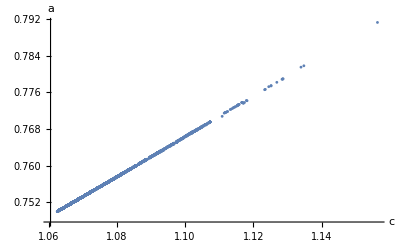

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@Select[total,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],PlotRange->All,AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005]];
Show[p1]
```

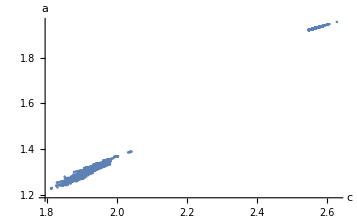

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@Select[su3nf6total,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],PlotRange->All,AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005]];
Show[p1]
```

### protected

```mathematica
su3nf6totalnoX=Select[su3nf6total,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&&#["consistency"]=="consistent"&];
```

```mathematica
su3Wgraph=toGlobalGraph[#["w"],#["n"][[2]]]&/@su3nf6totalnoX;
su2Wgraph=toGlobalGraph[#["w"],#["n"][[2]]]&/@total;
```

```mathematica
su2Wprotected=Select[total,MemberQ[su3Wgraph,toGlobalGraph[#["w"],#["n"][[2]]]]&];
%//Length
```

4158

```mathematica
su3Wprotected=Select[su3nf6totalnoX,MemberQ[su2Wgraph,toGlobalGraph[#["w"],#["n"][[2]]]]&];
%//Length
```

4158

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@Select[su2Wprotected,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],PlotRange->All,AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005],PlotRange->{{1.062,1.157},{0.75,0.792}}];
p2=ListPlot[{#["c"],#["a"]}&/@Select[Complement[total,su2Wprotected],!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->{PointSize[0.005],Red}];
Show[p1]
```

-Graphics-

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@Select[su3Wprotected,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005],PlotRange->{{2.545,2.628},{1.921,1.958}}];
p2=ListPlot[{#["c"],#["a"]}&/@Select[Complement[su3nf6totalnoX,su3Wprotected],!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->{PointSize[0.005],Red},PlotRange->All];
Show[p1]
```

-Graphics-

```mathematica
Select[Complement[su3nf6totalnoX,su3Wprotected],#["c"]<2.5469&][[112]]
```

<|w→{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb2,q3*qb2,M3*q2*qb1},a→1.3385546140307950698,c→1.9497301582665615803,M1→1.1105956461138679159,M2→0.93369649717066913256,M3→1.1768991489431987834,q1→0.4487386226863189095,q2→0.38243511985698804206,q3→1.3824351198569880421,q4→0.38973721803669712484,q5→0.38973721803669712484,q6→0.38973721803669712484,qb1→0.44066573119981317457,qb2→0.61756488014301195794,qb3→0.38973721803669712484,qb4→0.38973721803669712484,qb5→0.38973721803669712484,qb6→0.38973721803669712484,consistency→consistent,global→<|M1→{1,1,1,0,-1,1,1,1,1},M2→{1,1,1,1,-2,1,1,1,1},M3→{0,0,0,-1,1,0,0,0,0},q1→{-1,-1,-1,-1,1,-1,-1,-1,-1},q2→{0,0,0,0,-1,0,0,0,0},q3→{0,0,0,0,-1,0,0,0,0},q4→{1,0,0,0,0,0,0,0,0},q5→{0,1,0,0,0,0,0,0,0},q6→{0,0,1,0,0,0,0,0,0},qb1→{0,0,0,1,0,0,0,0,0},qb2→{0,0,0,0,1,0,0,0,0},qb3→{0,0,0,0,0,1,0,0,0},qb4→{0,0,0,0,0,0,1,0,0},qb5→{0,0,0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,0,0,1}|>,rational→,n→{0,3,6,6,0,0,0,0,0},relevant→{M1,M2,M3,q1*qb3,q2*qb3,q3*qb1,q3*qb3,q4*qb1,q4*qb3,q1^2*qb1*qb3,q1*q2*qb1^2,q1*q4*qb1^2,q1^2*qb3^2,q1^2*qb3*qb4,q1*q2*qb3^2,q1*q2*qb3*qb4,q1*q4*qb3^2,q1*q4*qb3*qb4,q2^2*qb1*qb3,q2*q4*qb1^2,q2^2*qb3^2,q2^2*qb3*qb4,q2*q4*qb3^2,q2*q4*qb3*qb4,q4^2*qb1^2,q4^2*qb1*qb3,q4*q5*qb1^2,q4*q5*qb1*qb3,q4^2*qb3^2,q4^2*qb3*qb4,q4*q5*qb3*qb4,M1*q1*qb3,M1*q2*qb3,M1*q4*qb1,M1*q4*qb3,M2*q1*qb3,M2*q2*qb3,M2*q4*qb1,M2*q4*qb3,M2^2,M3*q2*qb3,M3*q4*qb3},flip→{M1,M2,M3,q1*qb3,q2*qb3,q4*qb1,q4*qb3}|>

```mathematica
FindCharges[2,{0,3,4,4,0,0,0,0,0},{"M1*q1*qb1","q2^2*qb2^2","M2*q1*qb2","q3*qb2","M3*q2*qb1"}]
```

<|w→{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb2,q3*qb2,M3*q2*qb1,q2*qb3*X1,q2*qb4*X2},a→0.23684833425881484985,c→0.4653528404505985334,X1→1.4276667611233189722,X2→1.4276667611233189722,M1→1.2442971893424115594,M2→0.84478596710259334974,M3→1.3995112222398182097,q1→0.40507918938392314138,q2→0.24986515648651649112,q3→1.2498651564865164911,q4→0.34949586807556599499,qb1→0.35062362127366529918,qb2→0.75013484351348350888,qb3→0.32246808239016453667,qb4→0.32246808239016453667,consistency→consistent,global→<|X1→{0,0,0,1,0},X2→{0,0,0,0,1},M1→{1,0,1,-1,0},M2→{1,1,0,-1,-1},M3→{0,-1,1,0,1},q1→{-1,-1,-1,1,0},q2→{0,0,-1,0,-1},q3→{0,0,-1,0,-1},q4→{1,0,0,0,0},qb1→{0,1,0,0,0},qb2→{0,0,1,0,1},qb3→{0,0,1,-1,1},qb4→{0,0,1,0,0}|>,rational→,n→{2,3,4,4,0,0,0,0,0},relevant→{M1,M2,M3,X1,q1*qb3,q3*qb1,q3*qb3,q4*qb1,q4*qb3,q1^2*qb1*qb3,q1*q2*qb1^2,q1*q4*qb1^2,q1^2*qb3^2,q1^2*qb3*qb4,q1*q2*qb3^2,q1*q4*qb3^2,q1*q4*qb3*qb4,q2^2*qb1*qb3,q2*q4*qb1^2,q2^2*qb3*qb4,q2*q4*qb3^2,q4^2*qb1^2,q4^2*qb1*qb3,q4^2*qb3^2,q4^2*qb3*qb4,M1*q1*qb3,M1*q4*qb1,M1*q4*qb3,M2*q1*qb3,M2*q4*qb1,M2*q4*qb3,M2*q2^2*qb3*qb4,M2^2},flip→{M1,M2,q1*qb3,q4*qb1,q4*qb3,q1*q2*qb3^2,q2^2*qb1*qb3,q2*q4*qb1^2,q2^2*qb3*qb4,q2*q4*qb3^2}|>

```mathematica
Sort[Differences[SortBy[{#["a"],#["c"]}&/@su3Wprotected,#[[1]]&]]][[1]]
Position[Differences[SortBy[{#["a"],#["c"]}&/@su3Wprotected,#[[1]]&]],{%[[1]],%[[2]]}]
```

{3.4×10^-17,2.11×10^-16}

{{3908}}

```mathematica
SortBy[su3Wprotected,#["a"]&][[3908]]["a"]
SortBy[su3Wprotected,#["a"]&][[3908]]["c"]
SortBy[su3Wprotected,#["a"]&][[3908]]["w"]
```

1.9336923360254912712

2.5742385278274092053

{M1*q1*qb1,q2^2*qb2*qb3,M2*q2*qb1,q1*q3*qb2*qb3,M3*q1*qb4}

```mathematica
SortBy[su3Wprotected,#["a"]&][[3909]]["a"]
SortBy[su3Wprotected,#["a"]&][[3909]]["c"]
SortBy[su3Wprotected,#["a"]&][[3909]]["w"]
```

1.9336923360254913053

2.5742385278274094164

{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb2,q2^2*qb1*qb3,M3*q3*qb1}

```mathematica
Select[su3Wprotected,#["a"]==1.92557907068431444020021424192468181343`20.&]
```

{}

```mathematica
FindCharges[3,{0,3,6,6,0,0,0,0,0},{"M1*q1*qb1","q2^2*qb2*qb3","M2*q3*qb2","q2^2*qb3^2","M3*q2^2*"}]
```

<|w→{M1*q1*qb1,q2^2*qb2*qb3,M2*q3*qb2,q2^2*qb3^2},a→1.9255790706843144402,c→2.5555072711314834549,M1→0.95292443056541212614,M2→0.96822436227988363866,q1→0.52353778471729393693,q2→0.49218433956077073274,q3→0.52395997728088709407,q4→0.48685813214088262747,q5→0.48685813214088262747,q6→0.48685813214088262747,qb1→0.52353778471729393693,qb2→0.50781566043922926726,qb3→0.50781566043922926726,qb4→0.48685813214088262747,qb5→0.48685813214088262747,qb6→0.48685813214088262747,consistency→consistent,global→<|M1→{1,1,1,1,0,1,1,1,1},M2→{-1,0,0,0,0,-1,0,0,0},q1→{-1,-1,-1,-1,-1,-1,-1,-1,-1},q2→{0,0,0,0,0,-1,0,0,0},q3→{1,0,0,0,0,0,0,0,0},q4→{0,1,0,0,0,0,0,0,0},q5→{0,0,1,0,0,0,0,0,0},q6→{0,0,0,1,0,0,0,0,0},qb1→{0,0,0,0,1,0,0,0,0},qb2→{0,0,0,0,0,1,0,0,0},qb3→{0,0,0,0,0,1,0,0,0},qb4→{0,0,0,0,0,0,1,0,0},qb5→{0,0,0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,0,0,1}|>,rational→,n→{0,2,6,6,0,0,0,0,0},relevant→{M1,M2,q1*qb2,q1*qb3,q1*qb4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*qb1,q3*qb3,q3*qb4,q4*qb2,q4*qb3,q4*qb4,q1*q2*qb4^2,q1*q2*qb4*qb5,q1*q4*qb4^2,q1*q4*qb4*qb5,q2^2*qb1*qb4,q2^2*qb2*qb4,q2*q4*qb2^2,q2*q4*qb2*qb3,q2*q4*qb2*qb4,q2^2*qb3*qb4,q2*q4*qb3^2,q2*q4*qb3*qb4,q2^2*qb4^2,q2^2*qb4*qb5,q2*q3*qb4^2,q2*q3*qb4*qb5,q2*q4*qb4^2,q2*q4*qb4*qb5,q3*q4*qb4^2,q3*q4*qb4*qb5,q4^2*qb2^2,q4^2*qb2*qb3,q4^2*qb2*qb4,q4*q5*qb2^2,q4*q5*qb2*qb3,q4*q5*qb2*qb4,q4^2*qb3^2,q4^2*qb3*qb4,q4*q5*qb3^2,q4*q5*qb3*qb4,q4^2*qb4^2,q4^2*qb4*qb5,q4*q5*qb4*qb5,M1*q2*qb2,M1*q2*qb3,M1*q2*qb4,M1*q3*qb3,M1*q3*qb4,M1*q4*qb2,M1*q4*qb3,M1*q4*qb4,M1^2,M1*M2,M2*q1*qb3,M2*q1*qb4,M2*q2*qb1,M2*q2*qb3,M2*q2*qb4,M2*q3*qb4,M2*q4*qb3,M2*q4*qb4,M2^2},flip→{M1,M2,q1*qb2,q1*qb3,q1*qb4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*qb1,q3*qb3,q3*qb4,q4*qb2,q4*qb3,q4*qb4}|>

## SU3nf6

```mathematica
theory="SU3_6q_6qb";
```

## Gauge Invariant Operators

```mathematica
(* gauge-invariant operators *)
fund={q1,q2,q3,q4,q5,q6};
antifund={qb1,qb2,qb3,qb4,qb5,qb6};
matter=Join[fund,antifund];
messon=Flatten[Outer[Times,fund,antifund]];
quartic=(Times@@#)&/@Tuples[messon,2];
freeGIO=Join[messon,quartic];
```

## Import data

```mathematica
su36q6qblen0=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length0.wxf"];
su36q6qblen1=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length1.wxf"];
su36q6qblen2=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length2.wxf"];
su36q6qblen3=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length3.wxf"];
su36q6qblen4=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length4.wxf"];
su36q6qblen5=Import[NotebookDirectory[]<>theory<>"/"<>theory<>"_length5.wxf"];
```

## Length0

```mathematica
su3nf6len0={FindCharges[3,{0,0,6,6,0,0,0,0,0},{}]}
```

{<|w→{},a→1.921875,c→2.546875,q1→0.5,q2→0.5,q3→0.5,q4→0.5,q5→0.5,q6→0.5,qb1→0.5,qb2→0.5,qb3→0.5,qb4→0.5,qb5→0.5,qb6→0.5,consistency→consistent,global→<|q1→{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},q2→{1,0,0,0,0,0,0,0,0,0,0},q3→{0,1,0,0,0,0,0,0,0,0,0},q4→{0,0,1,0,0,0,0,0,0,0,0},q5→{0,0,0,1,0,0,0,0,0,0,0},q6→{0,0,0,0,1,0,0,0,0,0,0},qb1→{0,0,0,0,0,1,0,0,0,0,0},qb2→{0,0,0,0,0,0,1,0,0,0,0},qb3→{0,0,0,0,0,0,0,1,0,0,0},qb4→{0,0,0,0,0,0,0,0,1,0,0},qb5→{0,0,0,0,0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,0,0,0,0,1}|>,rational→<|a→123/64,c→163/64,q1→1/2,q2→1/2,q3→1/2,q4→1/2,q5→1/2,q6→1/2,qb1→1/2,qb2→1/2,qb3→1/2,qb4→1/2,qb5→1/2,qb6→1/2|>,n→{0,0,6,6,0,0,0,0,0},relevant→{q1*q2},flip→{q1*q2}|>}

```mathematica
Export[NotebookDirectory[]<>"SU3nf6_length0.wxf",su3nf6len0];
```

## Length1

```mathematica
su3nf6len1=Table[DeleteDuplicatesBy[
Select[Join[FindCharges[3,ii["n"],Append[ii["w"],#]]&/@(ii["relevant"]),FindCharges[3,ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>#]]&/@(ii["flip"])],#["consistency"]=="consistent"&],{#["a"],#["c"]}&],{ii,su3nf6len0}]//Flatten
```

{<|w→{M1*q1*qb1},a→1.9247502575433601739,c→2.5535719315343959531,M1→0.93885321614342753248,q1→0.53057339192828623376,q2→0.49388532161434275325,q3→0.49388532161434275325,q4→0.49388532161434275325,q5→0.49388532161434275325,q6→0.49388532161434275325,qb1→0.53057339192828623376,qb2→0.49388532161434275325,qb3→0.49388532161434275325,qb4→0.49388532161434275325,qb5→0.49388532161434275325,qb6→0.49388532161434275325,consistency→consistent,global→<|M1→{1,1,1,1,1,0,1,1,1,1,1},q1→{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},q2→{1,0,0,0,0,0,0,0,0,0,0},q3→{0,1,0,0,0,0,0,0,0,0,0},q4→{0,0,1,0,0,0,0,0,0,0,0},q5→{0,0,0,1,0,0,0,0,0,0,0},q6→{0,0,0,0,1,0,0,0,0,0,0},qb1→{0,0,0,0,0,1,0,0,0,0,0},qb2→{0,0,0,0,0,0,1,0,0,0,0},qb3→{0,0,0,0,0,0,0,1,0,0,0},qb4→{0,0,0,0,0,0,0,0,1,0,0},qb5→{0,0,0,0,0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,0,0,0,0,1}|>,rational→,n→{0,1,6,6,0,0,0,0,0},relevant→{M1,q1*qb2,q2*qb2,q2^2*qb2^2,q2^2*qb2*qb3,q2*q3*qb2*qb3,M1*q2*qb2,M1^2},flip→{M1,q1*qb2,q2*qb2}|>}

```mathematica
Export[NotebookDirectory[]<>"SU3nf6_length1.wxf",su3nf6len1];
```

```mathematica
su3nf6len1import=Import[NotebookDirectory[]<>"SU3nf6_length1.wxf"];
```

```mathematica
total=DeleteDuplicatesBy[Join[su3nf6len0,su3nf6len1],{#["a"],#["c"]}&];
%//Length
```

2

## Length2

```mathematica
Length[#["relevant"]]+Length[#["flip"]]&/@su3nf6len1
Total[%]
```

{11}

11

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["flip"]}]],{ii,su3nf6len1}],1];
nw//Length
```

11

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[nw,toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&];
%//Length
```

11

```mathematica
su3nf6len2=
Select[ParallelTable[FindCharges[3,iii[[1]],iii[[2]]],{iii,rnw}],#["consistency"]=="consistent"&];
%//Length
```

8

```mathematica
su3nf6len2=Select[su3nf6len2,!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}]&];
%//Length
```

6

```mathematica
Export[NotebookDirectory[]<>"SU3nf6_length2.wxf",su3nf6len2];
```

```mathematica
total=Join[su3nf6len0,su3nf6len1,su3nf6len2];
%//Length
```

8

## Length3

```mathematica
Length[#["relevant"]]+Length[#["flip"]]&/@su3nf6len2
Total[%]
```

{25,36,26,17,18,17}

139

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["flip"]}]],{ii,su3nf6len2}],1];
nw//Length
```

139

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[nw,toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&];
%//Length
```

108

```mathematica
su3nf6len3=
ParallelMap[workerFunction,rnw];
%//Length
```

{M1*q1*qb1,q2^2*qb2^2,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,q2*qb2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q1*qb3,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,q2*qb3}The number of variables doesn't match.

{M1*q1*qb1,M2*q2*qb2,q1*qb3,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,M2*q2*qb2,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,M2*q2*qb2,q1*qb2,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,q1*qb3,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,q2*qb1,X1*M1}The number of variables doesn't match.

85

```mathematica
su3nf6len3=Select[DeleteDuplicatesBy[su3nf6len3,{#["a"],#["c"]}&],!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}]&];
%//Length
```

53

```mathematica
su3nf6len3=Select[su3nf6len3,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
```

52

```mathematica
Export[NotebookDirectory[]<>"SU3nf6_length3.wxf",su3nf6len3];
```

```mathematica
su3nf6len3import=Import[NotebookDirectory[]<>"SU3nf6_length3.wxf"];
```

Import::nffil: File /Users/cms1308/Library/CloudStorage/OneDrive-Personal/Graduate/shared folder/shortRGflow/SU3nf6_length3.wxf not found during Import.

```mathematica
total=DeleteDuplicatesBy[Join[su3nf6len0,su3nf6len1,su3nf6len2,su3nf6len3],{#["a"],#["c"]}&];
%//Length
```

60

## Length4

```mathematica
Length[#["relevant"]]+Length[#["flip"]]&/@su3nf6len3
Total[%]
```

{38,32,52,47,55,82,74,75,51,48,33,49,38,26,55,34,52,104,37,85,75,73,61,111,47,81,57,50,77,48,74,48,53,59,59,89,50,58,32,48,67,34,67,45,57,77,35,17,29,33,55,37,30,22,33,41,17}

3013

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["flip"]}]],{ii,su3nf6len3}],1];
nw//Length
```

3013

```mathematica
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

1967

```mathematica
su3nf6len4=
ParallelMap[workerFunction,rnw];
%//Length
```

{M1*q1*qb1,q2^2*qb2^2,q2^2*qb2*qb3,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2*qb3,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2*qb3,q3*qb2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2*qb3,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q1*qb2,M1*X1,q2*qb1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q1*qb2,M1*X1,q2*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q1*qb2,M1*X1,q3*qb1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2*q3*qb3^2,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q1*qb2,M1*X1,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2*q3*qb2*qb3,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2*q3*qb2*qb3,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q3^2*qb3*qb4,q1*qb5,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2*q3*qb3^2,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2^2*qb3*qb4,q1*qb5,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q3*q4*qb3*qb4,q5*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q3^2*qb3*qb4,q4*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2^2*qb3*qb4,q3*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M1*q3*qb3,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2^2*qb2*qb3,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb3,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q3*qb3,q1*qb3,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q3*qb3,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q3*qb3,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb2,q1*qb3,X1*M2,X2*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb2,q3*qb1,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M1*q2*qb3,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2*q3*qb3*qb4,q1*qb5,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb2,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb2*qb4,q1*qb5,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb2*qb4,q2*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2*q3*qb3*qb4,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2*q3*qb3*qb4,q4*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q3*q4*qb3*qb4,q1*qb5,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb2*qb4,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M1*q3*qb3,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb2^2,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb2^2,q2*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q3*q4*qb3*qb4,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb2^2,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q2*qb3,q1*qb3,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q2*qb3,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb2*qb4,q4*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb4^2,q1*qb5,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M1*q2*qb3,q2*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q2*qb3,q3*qb3,X1*M2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q2*qb3,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M1*q2*qb3,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q2*qb2,q1*qb3,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q2*qb2,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3*q4*qb2*qb3,q5*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb4^2,q4*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb3,q1*qb4,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2^2*qb4*qb5,q1*qb6,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,q2*qb3,q1*qb2,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb3,q3*qb1,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2^2*qb4*qb5,q3*qb6}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3^2*qb2*qb4,q1*qb5,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3*q4*qb4*qb5,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M1*q2*qb2,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M1*q2*qb2,q2*qb2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3*q4*qb4*qb5,q5*qb6}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3^2*qb4*qb5,q1*qb6,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M1*q2*qb4,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3^2*qb2*qb4,q4*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3*q4*qb2*qb3,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M1*q2*qb2,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb4*qb5,q1*qb6,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q1*qb2,q3*qb1,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3^2*qb4*qb5,q4*qb6}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M1*q2*qb4,q2*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q1*qb2,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb4*qb5,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3*q4*qb2*qb4,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M1*q2*qb4,q3*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M1*q3*qb4,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q1*qb4,q1*qb5,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q2*qb4,q3*qb4,X1*M2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q2*qb4,q3*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M1*q3*qb2,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q2*qb2,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3*q4*qb2*qb4,q1*qb5,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3*q4*qb4*qb5,q1*qb6,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q3*q4*qb2*qb4,q5*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q1*qb4,q3*qb1,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb4*qb5,q4*qb6}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q1*qb2,q1*qb4,X1*M2,X2*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q2*qb2,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q1*qb4,q3*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q3*qb2,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M1*q3*qb2,q3*qb2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q2*qb1,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,q4*q5*qb4*qb5,M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q2*qb1,q3*qb1,X1*M2,X2*M1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q3*qb2,q3*qb1,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q2*qb1,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q3*qb2,q3*qb4,X1*M2}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,q4*q5*qb4*qb5,q2*qb2}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M1*q2*qb2,M1}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M1*q2*qb2,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M1*q3*qb4,q4*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q3*qb2,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q3*qb4,q1*qb4,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q3*qb4,q1*qb5,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M1*q2*qb4,q4*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M1*q3*qb2,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q2*qb4,q1*qb4,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q3*qb4,q4*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2^2*qb2*qb3,M2*q2*qb4,q1*qb5,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q1*qb2,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q1*qb4,q4*qb1,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q1*qb4,q4*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q2*qb2,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q2*qb4,q3*qb2}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,q2*q4*qb4*qb5,q1*qb6,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,M1*q3*qb3,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q2*qb2,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,q4*q5*qb4*qb5,q6*qb6}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q2*qb2,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,q2*q4*qb4*qb5,q3*qb2}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q2*qb4,q4*qb4,X1*M2}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q2*qb4,q4*qb5}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,M2*q1*qb3,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,M2*q1*qb2,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q1*qb2,q1*qb4,X1*M2,X2*M1}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M1*q4*qb4,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q2*qb1,q2*qb2,X1*M2,X2*M3}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q2*qb1,q2*qb3,X1*M3}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q2*qb1,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q1*qb2,q2*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q4*qb4,q1*qb4,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q4*qb4,q1*qb5,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q4*qb4,q2*qb2}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,M1*q3*qb3,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q4*qb4,q5*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q1*qb2,q4*qb1,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q2*qb3,q3*qb1,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,M2*q1*qb3,q2*qb2}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q2*qb3,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q2*qb2,M2}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,q2*q4*qb4*qb5,q5*qb6}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M1^2,q2*qb2,X1*M2}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q2*qb4,q1*qb4,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M1^2,q2*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q2*qb4,q1*qb5,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,M2*q3*qb3,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M1*q2*qb2,q2*qb2}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,M2*q1*qb3,q3*qb3,X1*M2}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,M2*q1*qb3,q3*qb4}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,M2*q3*qb3,q3*qb4,X1*M2}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,M2*q1*qb1,q2*qb2}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,M2*q3*qb3,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q1*qb4,q1*qb5,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,M1*q2*qb2,M2*q1*qb1,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M2*q1*qb4,q2*qb2}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M1*q4*qb4,q2*qb2}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M1*q4*qb4,q5*qb5}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M1*q2*qb4,q1*qb1}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q2*qb3,q1*qb3,X1*M1,X2*M2,X3*M3}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q1*qb3,q1*qb4,X1*M1,X2*M2,X3*M3}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q2*qb3,q1*qb4,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q1*qb3,q2*qb1,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q1*qb3,q2*qb4}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q2*qb3,q2*qb1,X1*M1,X2*M3}The number of variables doesn't match.

{M1*q1*qb1,M2*q2*qb2,M3*q3*qb3,q1*qb2,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q2*qb3,q2*qb4,X1*M3}The number of variables doesn't match.

{M1*q1*qb1,M2*q2*qb2,M3*q3*qb3,q1*qb4,X1*M1}The number of variables doesn't match.

{M1*q1*qb1,M2*q2*qb2,M3*q3*qb3,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M1*q2*qb2,q3*qb3}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M1*q2*qb2,q4*qb4}The number of variables doesn't match.

{M1*q1*qb1,M2*q1*qb2,M3*q2*qb1,q1*qb3,X1*M1,X2*M2}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M1*q2*qb4,q2*qb4}The number of variables doesn't match.

{M1*q1*qb1,q2*q3*qb2*qb3,M1*q2*qb4,q3*qb2}The number of variables doesn't match.

1645

```mathematica
2043
```

```mathematica
su3nf6len4=Select[DeleteDuplicatesBy[su3nf6len4,{#["a"],#["c"]}&],!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}]&];
%//Length
```

900

```mathematica
1018
```

```mathematica
AppendTo[length4,%122];
```

```mathematica
length4//Length
```

1018

```mathematica
SortBy[su3nf6len4,#["a"]&][[1]]
```

<|w→{M1*q1*qb1,q2^2*qb2^2,M1*q3*qb3,q1*qb2,M1*X1,q2*qb1*X2,q2*qb4*X3,q2*qb5*X4,q2*qb6*X5,q4*qb1*X6,q5*qb1*X7,q6*qb1*X8},a→0.91766583626572550986,c→1.3274869856447744192,X1→1.2785691950323912748,X2→1.7214308049676087252,X3→1.4535718008279347875,X4→1.4535718008279347875,X5→1.4535718008279347875,X6→1.4535718008279347875,X7→1.4535718008279347875,X8→1.4535718008279347875,M1→0.72143080496760872522,q1→1.1392845975161956374,q2→0.13928459751619563739,q3→0.63928459751619563739,q4→0.40714360165586957507,q5→0.40714360165586957507,q6→0.40714360165586957507,qb1→0.13928459751619563739,qb2→0.86071540248380436261,qb3→0.63928459751619563739,qb4→0.40714360165586957507,qb5→0.40714360165586957507,qb6→0.40714360165586957507,consistency→consistent,global→<|X1→{0,0,-1,-1,-1,-1,-1,-1},X2→{0,0,1,1,1,1,1,1},X3→{0,0,1,0,0,0,0,0},X4→{0,0,0,1,0,0,0,0},X5→{0,0,0,0,1,0,0,0},X6→{0,0,0,0,0,1,0,0},X7→{0,0,0,0,0,0,1,0},X8→{0,0,0,0,0,0,0,1},M1→{0,0,1,1,1,1,1,1},q1→{0,-1,0,0,-1,0,0,0},q2→{0,-1,0,0,-1,0,0,0},q3→{-1,0,-1,-1,-1,-1,-1,-1},q4→{0,-1,1,1,0,0,1,1},q5→{0,-1,1,1,0,1,0,1},q6→{0,-1,1,1,0,1,1,0},qb1→{0,1,-1,-1,0,-1,-1,-1},qb2→{0,1,0,0,1,0,0,0},qb3→{1,0,0,0,0,0,0,0},qb4→{0,1,-1,0,1,0,0,0},qb5→{0,1,0,-1,1,0,0,0},qb6→{0,1,0,0,0,0,0,0}|>,rational→,n→{8,1,6,6,0,0,0,0,0},relevant→{X1,X2,X3,X6,q1*qb1,q1*qb3,q1*qb4,q2*qb2,q2*qb3,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb2,q4*qb3,q4*qb4,q1*q2*qb1^2,q1*q4*qb1^2,q2^2*qb1*qb2,q2^2*qb1*qb3,q2^2*qb1*qb4,q2*q3*qb1^2,q2*q4*qb1^2,q2^2*qb2*qb3,q2^2*qb2*qb4,q2^2*qb3^2,q2^2*qb3*qb4,q2*q4*qb3^2,q2^2*qb4*qb5,q2*q3*qb4^2,q2*q4*qb4^2,q3^2*qb1^2,q3^2*qb1*qb4,q3*q4*qb1^2,q3*q4*qb4^2,q3*q4*qb4*qb5,q4^2*qb1*qb2,q4^2*qb1*qb3,q4^2*qb1*qb4,q4*q5*qb1^2,q4^2*qb3*qb4,q4*q5*qb3*qb4,q4^2*qb4^2,q4^2*qb4*qb5,q4*q5*qb4^2,q4*q5*qb4*qb5},flip→{X1,q1*qb1,q2*qb2,q2*qb3,q3*qb1,q3*qb3,q3*qb4,q4*qb2,q4*qb3,q4*qb4,q2^2*qb1*qb2,q2^2*qb1*qb3,q2^2*qb1*qb4,q2*q3*qb1^2,q2*q4*qb1^2,q2^2*qb3*qb4,q2^2*qb4*qb5,q3*q4*qb1^2,q4*q5*qb1^2}|>

```mathematica
su3nf6len4=Select[su3nf6len4,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
```

855

```mathematica
Export[NotebookDirectory[]<>"SU3nf6_length4.wxf",su3nf6len4];
```

```mathematica
su3nf6len4import=Import[NotebookDirectory[]<>"SU3nf6_length4.wxf"];
```

```mathematica
su3nf6total=DeleteDuplicatesBy[Join[su3nf6len0,su3nf6len1,su3nf6len2,su3nf6len3,su3nf6len4],{#["a"],#["c"]}&];
%//Length
```

915

## Length5

```mathematica
Length[#["relevant"]]+Length[#["flip"]]&/@su3nf6len4;
Total[%]
```

96314

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["flip"]}]],{ii,su3nf6len4}],1];
nw//Length
```

96314

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

58417

```mathematica
Export[NotebookDirectory[]<>"SU3nf6_rnw5.wxf",rnw];
```

```mathematica
rnw=Import[NotebookDirectory[]<>"SU3nf6_rnw5.wxf"];
%//Length
```

58417

```mathematica
su3nf6len5=ParallelMap[workerFunction,rnw];
%//Length
```

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb4*qb5,q3*q4*qb2*qb4,q1*qb3,X1*M1,X2*q5*qb1,X3*q5*qb6}

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb4*qb5,q3*q4*qb2*qb4,q5*qb3,X1*q1*qb6}

50707

```mathematica
su3nf6len5=Select[DeleteDuplicatesBy[su3nf6len5,{#["a"],#["c"]}&],!MemberQ[{#["a"],#["c"]}&/@su3nf6total,{#["a"],#["c"]}]&];
%//Length
```

$Aborted

0

```mathematica
su3nf6len5=Select[su3nf6len5,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
```

23700

```mathematica
Export[NotebookDirectory[]<>"SU3nf6_length5.wxf",su3nf6len5];
```

```mathematica
su3nf6len5=Import[NotebookDirectory[]<>"SU3nf6_length5.wxf"];
%//Length
```

26718

```mathematica
su3nf6total=DeleteDuplicatesBy[Join[su3nf6len0,su3nf6len1,su3nf6len2,su3nf6len3,su3nf6len4,su3nf6len5],{#["a"],#["c"]}&];
%//Length
```

27678

```mathematica
URLExecute["https://api.telegram.org/bot<REDACTED>/sendMessage",{"chat_id"->"5926111332","text"->"Task completed"}]
```

{ok→True,result→{message_id→1580,from→{id→5869515437,is_bot→True,first_name→Landscape_bot,username→SCFTlandscape_bot},chat→{id→5926111332,first_name→Minseok,last_name→Cho,type→private},date→1772620873,text→Task completed}}

## Length6

```mathematica
Length[#["relevant"]]+Length[#["flip"]]&/@Select[su3nf6len5,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
Total[%]
```

4279235

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["flip"]}]],{ii,Select[su3nf6len5,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&]}],1];
nw//Length
```

4279235

```mathematica
Export[NotebookDirectory[]<>"SU3nf6_nw6.wxf",nw];
```

```mathematica
nw=Import[NotebookDirectory[]<>"SU3nf6_nw6.wxf"];
%//Length
```

4279235

```mathematica
(*Run the reduction*)
rnw=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],Max[#[[1,2]]&/@nw]]&,nw], nw}],First][[All,2]];
%//Length
```

2375233

```mathematica
Export[NotebookDirectory[]<>"SU3nf6_rnw6.wxf",rnw];
```

```mathematica
rnw=Import[NotebookDirectory[]<>"SU3nf6_rnw6.wxf"];
%//Length
```

2584539

```mathematica
length63=ParallelMap[workerFunction,rnw[[20001;;30000]]];
```

```mathematica
Export[NotebookDirectory[]<>"SU2nf4_length62.wxf",length62];
```

```mathematica
su3nf6len51=ParallelMap[workerFunction,rnw[[;;100000]]];
%//Length
```

{M1*q1*qb1,q2^2*qb2^2,q2*qb3,q1*q3*qb2^2,q3*q4*qb2^2,q3*qb4,X1*q1*qb2,X2*q1*qb5,X3*q1*qb6,X4*q4*qb1,X5*q4*qb2,X6*q4*qb5,X7*q4*qb6,X8*q5*qb1,X9*q5*qb2,X10*q5*qb5}

{M1*q1*qb1,q2^2*qb2^2,q2^2*qb3*qb4,q2*q3*qb3*qb5,q4*qb3,q1*qb2,X1*M1,X2*q2*qb1,X3*q2*qb4,X4*q2*qb5,X5*q2*qb6,X6*q3*qb1,X7*q3*qb4,X8*q3*qb5,X9*q3*qb6,X10*q5*qb1,X11*q5*qb4,X12*q5*qb5,X13*q5*qb6,X14*q6*qb1,X15*q6*qb4,X16*q6*qb5}

90419

```mathematica
Do[Export[NotebookDirectory[]<>"SU2nf4_length6"<>ToString[len]<>".wxf",ParallelMap[workerFunction,rnw[[(len-1) 10000 + 1;;Min[len 10000,Length[rnw]]]]]];,{len,27,100}]
```

{M1*q1*q2,q3^2*q4^2,M2*q1*q3,M3*q3*qb1,M4*q3*qb2,M5*qb1*qb3}

{M1*q1*q2,q3^2*q4^2,M2*q1*q3,M3*q3*qb1,M4*q4*qb2,M5*qb1*qb3}

{M1*q1*q2,q3^2*q4^2,M2*q1*qb1,M3*q2*qb2,M4*qb1*qb3,M5*q3*qb4}

{M1*q1*q2,q3^2*q4^2,M2*q1*qb1,M3*q3*qb2,M4*q3*qb3,M5*q4*qb2}

```mathematica
Charges50[2,{0,5,4,4,0,0,0,0,0},{"M1*q1*q2","q3^2*q4^2","M2*q1*q3","M3*q3*qb1","M4*q3*qb2","M5*qb1*qb3"}]
```

{M1*q1*q2,q3^2*q4^2,M2*q1*q3,M3*q3*qb1,M4*q3*qb2,M5*qb1*qb3}

<|w→{M1*q1*q2,q3^2*q4^2,M2*q1*q3,M3*q3*qb1,M4*q3*qb2,M5*qb1*qb3},consistency→Cannot solve|>

```mathematica
length6=Join@@(Import/@Table[NotebookDirectory[]<>"SU2nf4_length6"<>ToString[i]<>".wxf",{i,1,100}]);
%//Length
```

824274

```mathematica
Select[length6,AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
Sort[%%,#["a"]&][[1]]["a"]
```

7629

0.11321300178215934942

```mathematica
su3nf6len61=Select[su3nf6len51,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
```

79104

```mathematica
su3nf6len61=Select[DeleteDuplicatesBy[su3nf6len61,{#["a"],#["c"]}&],!MemberQ[{#["a"],#["c"]}&/@su3nf6total,{#["a"],#["c"]}]&];
%//Length
```

37827

```mathematica
Export[NotebookDirectory[]<>"SU3nf6_length61.wxf",su3nf6len61];
```

```mathematica
Export[NotebookDirectory[]<>"SU3nf6_length61_X.wxf",%21];
```

```mathematica
su3nf6total=DeleteDuplicatesBy[Join[su3nf6len0,su3nf6len1,su3nf6len2,su3nf6len3,su3nf6len4,su3nf6len5,su3nf6len61],{#["a"],#["c"]}&];
%//Length
```

65506

```mathematica
URLExecute["https://api.telegram.org/bot<REDACTED>/sendMessage",{"chat_id"->"5926111332","text"->"Task completed"}]
```

{ok→True,result→{message_id→1581,from→{id→5869515437,is_bot→True,first_name→Landscape_bot,username→SCFTlandscape_bot},chat→{id→5926111332,first_name→Minseok,last_name→Cho,type→private},date→1773030705,text→Task completed}}

## Length7

```mathematica
Length[#["relevant"]]+Length[#["flip"]]&/@length6;
Total[%]
```

11675732

```mathematica
nw=Flatten[Table[Join[Table[{ii["n"],Append[ii["w"],iii]},{iii,ii["relevant"]}],Table[{ii["n"]+{0,1,0,0,0,0,0,0,0},Append[ii["w"],"M"<>ToString[ii["n"][[2]]+1]<>"*"<>iii]},{iii,ii["flip"]}]],{ii,length6}],1];
nw//Length
```

11675732

```mathematica
Export[NotebookDirectory[]<>"SU2nf4_nw7.wxf",nw];
```

```mathematica
nw=Import[NotebookDirectory[]<>"SU2nf4_nw7.wxf"];
%//Length
```

11675732

```mathematica
maxflip=Max[#[[1,2]]&/@nw]
```

4

```mathematica
(*Run the reduction*)
rnw1=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],maxflip]&,nw[[;;4000000]]], nw[[;;4000000]]}],First];
%//Length
```

3080618

```mathematica
rnw2=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],maxflip]&,nw[[4000001;;8000000]]], nw[[4000001;;8000000]]}],First];
%//Length
```

3205498

```mathematica
rnw3=DeleteDuplicatesBy[Transpose[{ParallelMap[toGlobalGraph[#[[2]],maxflip]&,nw[[8000001;;]]], nw[[8000001;;]]}],First];
%//Length
```

2945958

```mathematica
rnw=DeleteDuplicatesBy[Join[rnw1,rnw2,rnw3],First][[All,2]];
```

```mathematica
rnw//Length
```

8641094

```mathematica
Export[NotebookDirectory[]<>"SU2nf4_rnw7.wxf",rnw];
```

```mathematica
rnw=Import[NotebookDirectory[]<>"SU2nf4_rnw7.wxf"];
%//Length
```

8641094

```mathematica
length63=ParallelMap[workerFunction,rnw[[20001;;30000]]];
```

```mathematica
Export[NotebookDirectory[]<>"SU2nf4_length62.wxf",length62];
```

```mathematica
Do[Export[NotebookDirectory[]<>"SU2nf4_length7"<>ToString[len]<>".wxf",ParallelMap[workerFunction,rnw[[(len-1) 10000 + 1;;Min[len 10000,Length[rnw]]]]]];,{len,1,87}]
```

```mathematica
length7=Join@@(Import/@Table[NotebookDirectory[]<>"SU2nf4_length7"<>ToString[i]<>".wxf",{i,1,87}]);
%//Length
```

722834

```mathematica
length7=Select[DeleteDuplicatesBy[length7,{#["a"],#["c"]}&],!MemberQ[{#["a"],#["c"]}&/@total,{#["a"],#["c"]}]&];
%//Length
```

$Aborted

0

```mathematica
Export[NotebookDirectory[]<>"SU2nf4_length6.wxf",length6];
```

```mathematica
total=DeleteDuplicatesBy[Join[length0,length1,length2,length3,length4,length5,length6],{#["a"],#["c"]}&];
%//Length
```

79921

## Distribution

```mathematica
total//Length
```

23366

```mathematica
su3nf6total=Select[su3nf6total,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
```

24615

```mathematica
Sort[Differences[SortBy[{#["a"],#["c"]}&/@su3nf6total,#[[1]]&]]][[1]]
```

{7.×10^-19,3.×10^-18}

```mathematica
Position[Differences[SortBy[{#["a"],#["c"]}&/@su3nf6total,#[[1]]&]],{6.730408202921511941`1.2427166284851896*^-19,3.33025915433591249436`1.8144395805471116*^-18}]
```

{{12542}}

```mathematica
SortBy[su3nf6total,#["a"]&][[12542]]["a"]
SortBy[su3nf6total,#["a"]&][[12542]]["c"]
SortBy[su3nf6total,#["a"]&][[12542]]["w"]
```

1.9243974868612553346

2.5527509975066833044

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb2*qb4,q1*q4*qb5^2,q2*q4*qb4^2}

```mathematica
Charges30[3,{0,1,6,6,0,0,0,0,0},{"M1*q1*qb1","q2^2*qb2*qb3","q2*q3*qb2*qb4","q1*q4*qb5^2","q2*q4*qb4^2"}]["a"]
Charges30[3,{0,1,6,6,0,0,0,0,0},{"M1*q1*qb1","q2^2*qb2*qb3","q2*q3*qb2*qb4","q1*q4*qb5^2","q2*q4*qb4^2"}]["c"]
```

1.92439748686125533461172170468

2.55275099750668330436552572543

```mathematica
SortBy[su3nf6total,#["a"]&][[12543]]["a"]
SortBy[su3nf6total,#["a"]&][[12543]]["c"]
SortBy[su3nf6total,#["a"]&][[12543]]["w"]
```

1.9243974868612553353

2.5527509975066833077

{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb2*qb4,q1*q4*qb5^2,q3*q4*qb2^2}

```mathematica
FindCharges[3,{0,4,6,6,0,0,0,0,0},{"M1*q1*q2","q3^2*q4*qb1","M2*q3*q4","M3*q3*qb2","M4*qb1*qb3"}]["a"]
```

$Aborted

```mathematica
Charges30[3,{0,4,6,6,0,0,0,0,0},{"M1*q1*q2","q3^2*q4*qb1","M2*q3*q4","M3*q3*qb2","M4*qb1*qb3"}]["a"]
Charges30[3,{0,4,6,6,0,0,0,0,0},{"M1*q1*q2","q3^2*q4*qb1","M2*q3*q4","M3*q3*qb2","M4*qb1*qb3"}]["c"]
```

1.92583094173114250236060455929

2.55609755528542315050543968721

```mathematica
%174-%179
```

7.×10^-19

```mathematica
%175-%180
```

3.×10^-18

```mathematica
SortBy[su3nf6total,#["a"]&][[1]]
SortBy[su3nf6total,#["a"]&][[-1]]
```

<|w→{M1*q1*qb1,q2^2*qb2^2,q2*qb3,q3^2*qb2*qb4,q3*q4*qb5^2},a→1.248161028232307284,c→1.8528279617303113734,M1→1.3253290640319345696,q1→0.33733546798403271521,q2→0.59228879368997108092,q3→0.59228879368997108092,q4→0.41145968508688413638,q5→0.33601080400781637425,q6→0.33601080400781637425,qb1→0.33733546798403271521,qb2→0.40771120631002891908,qb3→1.4077112063100289191,qb4→0.40771120631002891908,qb5→0.49812576061157239135,qb6→0.33601080400781637425,consistency→consistent,global→<|M1→{1,1,0,2,2,-1,1},q1→{-1,-1,-1,-2,-2,1,-1},q2→{0,0,0,-2,0,0,0},q3→{0,0,0,-1,-1,0,0},q4→{0,0,0,1,1,-2,0},q5→{1,0,0,0,0,0,0},q6→{0,1,0,0,0,0,0},qb1→{0,0,1,0,0,0,0},qb2→{0,0,0,2,0,0,0},qb3→{0,0,0,2,0,0,0},qb4→{0,0,0,0,2,0,0},qb5→{0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,1}|>,rational→,n→{0,1,6,6,0,0,0,0,0},relevant→{M1,q1*qb2,q1*qb3,q1*qb4,q1*qb5,q1*qb6,q3*qb1,q3*qb2,q3*qb4,q3*qb5,q3*qb6,q4*qb1,q4*qb2,q4*qb3,q4*qb4,q4*qb5,q4*qb6,q5*qb2,q5*qb3,q5*qb4,q5*qb5,q5*qb6,q1^2*qb1*qb2,q1^2*qb1*qb4,q1^2*qb1*qb5,q1^2*qb1*qb6,q1*q3*qb1^2,q1*q4*qb1^2,q1^2*qb2^2,q1^2*qb2*qb4,q1^2*qb2*qb5,q1^2*qb2*qb6,q1*q3*qb2^2,q1*q3*qb2*qb4,q1*q3*qb2*qb5,q1*q3*qb2*qb6,q1*q4*qb2^2,q1*q4*qb2*qb4,q1*q4*qb2*qb5,q1*q4*qb2*qb6,q1*q5*qb2^2,q1*q5*qb2*qb4,q1*q5*qb2*qb5,q1*q5*qb2*qb6,q1^2*qb4^2,q1^2*qb4*qb5,q1^2*qb4*qb6,q1*q3*qb4^2,q1*q3*qb4*qb5,q1*q3*qb4*qb6,q1*q4*qb4^2,q1*q4*qb4*qb5,q1*q4*qb4*qb6,q1*q5*qb4^2,q1*q5*qb4*qb5,q1*q5*qb4*qb6,q1^2*qb5^2,q1^2*qb5*qb6,q1*q3*qb5*qb6,q1*q4*qb5^2,q1*q4*qb5*qb6,q1*q5*qb5^2,q1*q5*qb5*qb6,q1^2*qb6^2,q1*q3*qb6^2,q1*q4*qb6^2,q1*q5*qb6^2,q3^2*qb1^2,q3^2*qb1*qb4,q3^2*qb1*qb6,q3*q4*qb1^2,q3*q4*qb1*qb2,q3*q4*qb1*qb4,q3*q4*qb1*qb5,q3*q4*qb1*qb6,q3*q5*qb1^2,q3*q5*qb1*qb6,q3*q4*qb2^2,q3*q4*qb2*qb4,q3*q4*qb2*qb5,q3*q4*qb2*qb6,q3*q5*qb2^2,q3*q5*qb2*qb4,q3*q5*qb2*qb5,q3*q5*qb2*qb6,q3^2*qb4*qb6,q3*q4*qb4^2,q3*q4*qb4*qb5,q3*q4*qb4*qb6,q3*q5*qb4^2,q3*q5*qb4*qb5,q3*q5*qb4*qb6,q3*q4*qb5*qb6,q3*q5*qb5*qb6,q3^2*qb6^2,q3*q4*qb6^2,q3*q5*qb6^2,q4^2*qb1^2,q4^2*qb1*qb2,q4^2*qb1*qb4,q4^2*qb1*qb5,q4^2*qb1*qb6,q4*q5*qb1^2,q4*q5*qb1*qb6,q4^2*qb2^2,q4^2*qb2*qb4,q4^2*qb2*qb5,q4^2*qb2*qb6,q4*q5*qb2^2,q4*q5*qb2*qb4,q4*q5*qb2*qb5,q4*q5*qb2*qb6,q4^2*qb4^2,q4^2*qb4*qb5,q4^2*qb4*qb6,q4*q5*qb4^2,q4*q5*qb4*qb5,q4*q5*qb4*qb6,q4^2*qb5^2,q4^2*qb5*qb6,q4*q5*qb5^2,q4*q5*qb5*qb6,q4^2*qb6^2,q4*q5*qb6^2,q5^2*qb1*qb2,q5^2*qb1*qb4,q5^2*qb1*qb5,q5*q6*qb1^2,q5*q6*qb1*qb6,q5^2*qb2^2,q5^2*qb2*qb4,q5^2*qb2*qb5,q5^2*qb2*qb6,q5*q6*qb2^2,q5*q6*qb2*qb4,q5*q6*qb2*qb5,q5*q6*qb2*qb6,q5^2*qb4^2,q5^2*qb4*qb5,q5^2*qb4*qb6,q5*q6*qb4^2,q5*q6*qb4*qb5,q5*q6*qb4*qb6,q5^2*qb5^2,q5^2*qb5*qb6,q5*q6*qb5^2,q5*q6*qb5*qb6,q5^2*qb6^2,q5*q6*qb6^2,M1*q5*qb6},flip→{M1,q1*qb2,q1*qb4,q1*qb5,q1*qb6,q3*qb1,q3*qb2,q3*qb4,q3*qb5,q3*qb6,q4*qb1,q4*qb2,q4*qb4,q4*qb5,q4*qb6,q5*qb2,q5*qb4,q5*qb5,q5*qb6}|>

<|w→{M1*q1*qb1,M2*q1*qb2,M3*q1*qb3,M4*q1*qb4,M5*q1*qb5},a→1.9571075098250921978,c→2.6277506800262471921,M1→0.853941855356304018,M2→0.853941855356304018,M3→0.853941855356304018,M4→0.853941855356304018,M5→0.853941855356304018,q1→0.64311825457020509798,q2→0.47369704917705674699,q3→0.47369704917705674699,q4→0.47369704917705674699,q5→0.47369704917705674699,q6→0.47369704917705674699,qb1→0.50293989007349088402,qb2→0.50293989007349088402,qb3→0.50293989007349088402,qb4→0.50293989007349088402,qb5→0.50293989007349088402,qb6→0.47369704917705674699,consistency→consistent,global→<|M1→{1,1,1,1,1,0,1,1,1,1,1},M2→{1,1,1,1,1,1,0,1,1,1,1},M3→{1,1,1,1,1,1,1,0,1,1,1},M4→{1,1,1,1,1,1,1,1,0,1,1},M5→{1,1,1,1,1,1,1,1,1,0,1},q1→{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},q2→{1,0,0,0,0,0,0,0,0,0,0},q3→{0,1,0,0,0,0,0,0,0,0,0},q4→{0,0,1,0,0,0,0,0,0,0,0},q5→{0,0,0,1,0,0,0,0,0,0,0},q6→{0,0,0,0,1,0,0,0,0,0,0},qb1→{0,0,0,0,0,1,0,0,0,0,0},qb2→{0,0,0,0,0,0,1,0,0,0,0},qb3→{0,0,0,0,0,0,0,1,0,0,0},qb4→{0,0,0,0,0,0,0,0,1,0,0},qb5→{0,0,0,0,0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,0,0,0,0,1}|>,rational→,n→{0,5,6,6,0,0,0,0,0},relevant→{M1,q1*qb6,q2*qb1,q2*qb6,q2^2*qb1^2,q2^2*qb1*qb2,q2^2*qb1*qb6,q2*q3*qb1^2,q2*q3*qb1*qb2,q2*q3*qb1*qb6,q2^2*qb6^2,q2*q3*qb6^2,M1*q2*qb1,M1*q2*qb2,M1*q2*qb6,M1^2,M1*M2},flip→{M1,q1*qb6,q2*qb1,q2*qb6}|>

```mathematica
su3nf6len0
```

{<|w→{},a→1.921875,c→2.546875,q1→0.5,q2→0.5,q3→0.5,q4→0.5,q5→0.5,q6→0.5,qb1→0.5,qb2→0.5,qb3→0.5,qb4→0.5,qb5→0.5,qb6→0.5,consistency→consistent,global→<|q1→{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},q2→{1,0,0,0,0,0,0,0,0,0,0},q3→{0,1,0,0,0,0,0,0,0,0,0},q4→{0,0,1,0,0,0,0,0,0,0,0},q5→{0,0,0,1,0,0,0,0,0,0,0},q6→{0,0,0,0,1,0,0,0,0,0,0},qb1→{0,0,0,0,0,1,0,0,0,0,0},qb2→{0,0,0,0,0,0,1,0,0,0,0},qb3→{0,0,0,0,0,0,0,1,0,0,0},qb4→{0,0,0,0,0,0,0,0,1,0,0},qb5→{0,0,0,0,0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,0,0,0,0,1}|>,rational→<|a→123/64,c→163/64,q1→1/2,q2→1/2,q3→1/2,q4→1/2,q5→1/2,q6→1/2,qb1→1/2,qb2→1/2,qb3→1/2,qb4→1/2,qb5→1/2,qb6→1/2|>,n→{0,0,6,6,0,0,0,0,0},relevant→{q1*qb1},flip→{q1*qb1},nsolve→exactly solved without Groebner|>}

```mathematica
su3nf6total;
SortBy[%%,#["a"]&][[1]]
```

27679

<|w→{M1*q1*qb1,q2^2*qb2*qb3,q2*q3*qb4*qb5,q3*qb2,q2*qb3*X1,q2*qb4*X2,q2*qb5*X3,q1*qb3,q2*qb1*X4,q2*qb6*X5,q4*qb1*X6,q4*qb4*X7,q4*qb5*X8,q4*qb6*X9,q5*qb1*X10,q5*qb4*X11,q5*qb5*X12,q5*qb6*X13,q6*qb4*X14,q6*qb1*X15,q6*qb5*X16,q6*qb6*X17},a→0.18705220717039440624,c→0.34383796821514069378,X1→0.77877448081292772431,X2→1.6106127595935361378,X3→1.6106127595935361378,X4→1.4914278232840593994,X5→1.5395892393579557046,X6→1.4073469626743636062,X7→1.5265318989838403446,X8→1.5265318989838403446,X9→1.4555083787482599113,X10→1.4073469626743636062,X11→1.5265318989838403446,X12→1.5265318989838403446,X13→1.4555083787482599113,X14→1.5265318989838403446,X15→1.4073469626743636062,X16→1.5265318989838403446,X17→1.4555083787482599113,M1→0.71265334247113167511,q1→0.96530530353117384738,q2→0.18653082271824612307,q3→1.4077563419053183988,q4→0.2706116833279419163,q5→0.2706116833279419163,q6→0.2706116833279419163,qb1→0.32204135399769447751,qb2→0.59224365809468160123,qb3→1.0346946964688261526,qb4→0.20285641768821773908,qb5→0.20285641768821773908,qb6→0.27387993792379817235,consistency→consistent,global→<|X1→{0,0,-2,0,-1,-1,2},X2→{0,0,1,0,1,0,-1},X3→{0,0,1,0,0,1,-1},X4→{0,0,1,1,0,0,-1},X5→{0,0,1,0,0,0,0},X6→{0,0,0,1,0,0,0},X7→{0,0,0,0,1,0,0},X8→{0,0,0,0,0,1,0},X9→{0,0,0,0,0,0,1},X10→{0,-1,-1,0,-1,-1,1},X11→{0,-1,-1,-1,0,-1,1},X12→{0,-1,-1,-1,-1,0,1},X13→{0,-1,-1,-1,-1,-1,2},X14→{0,1,0,0,1,0,-1},X15→{0,1,0,1,0,0,-1},X16→{0,1,0,0,0,1,-1},X17→{0,1,0,0,0,0,0},M1→{0,0,3,1,1,1,-3},q1→{-1,0,-3,0,-1,-1,2},q2→{-1,0,-1,0,0,0,0},q3→{-1,0,1,0,1,1,-2},q4→{-1,0,0,0,0,0,-1},q5→{-1,1,1,1,1,1,-2},q6→{-1,-1,0,0,0,0,0},qb1→{1,0,0,-1,0,0,1},qb2→{1,0,-1,0,-1,-1,2},qb3→{1,0,3,0,1,1,-2},qb4→{1,0,0,0,-1,0,1},qb5→{1,0,0,0,0,-1,1},qb6→{1,0,0,0,0,0,0}|>,rational→,n→{17,1,6,6,0,0,0,0,0},relevant→{M1,X1,X2,X4,X5,X6,X7,X9,q1*qb2,q1*qb4,q1*qb6,q2*qb2,q3*qb1,q3*qb4,q3*qb6,q4*qb2,q4*qb3,q1*q2*qb1^2,q1*q4*qb1^2,q1*q2*qb4^2,q1*q4*qb4^2,q1*q2*qb6^2,q1*q4*qb6^2,q2^2*qb1*qb2,q2^2*qb1*qb3,q2^2*qb1*qb4,q2^2*qb1*qb6,q2*q4*qb1^2,q2^2*qb2^2,q2^2*qb2*qb4,q2^2*qb2*qb6,q2*q4*qb2^2,q2^2*qb3*qb4,q2^2*qb3*qb6,q2^2*qb4*qb5,q2^2*qb4*qb6,q2*q4*qb4^2,q2*q4*qb6^2,q4^2*qb1*qb2,q4^2*qb1*qb3,q4^2*qb1*qb4,q4^2*qb1*qb6,q4*q5*qb1^2,q4^2*qb2^2,q4^2*qb2*qb4,q4^2*qb2*qb6,q4*q5*qb2^2,q4^2*qb3*qb4,q4^2*qb3*qb6,q4^2*qb4*qb5,q4^2*qb4*qb6,q4*q5*qb4^2,q4*q5*qb6^2,M1*q1*qb4,M1*q1*qb6,M1*q2*qb2,M1*q4*qb2,M1*q2^2*qb1*qb4,M1*q2^2*qb1*qb6,M1*q2*q4*qb1^2,M1*q2^2*qb2*qb4,M1*q2^2*qb2*qb6,M1*q2^2*qb4*qb5,M1*q2^2*qb4*qb6,M1*q2*q4*qb4^2,M1*q2*q4*qb6^2,M1*q4^2*qb1*qb4,M1*q4^2*qb1*qb6,M1*q4*q5*qb1^2,M1*q4^2*qb4*qb5,M1*q4^2*qb4*qb6,M1*q4*q5*qb4^2,M1*q4*q5*qb6^2,M1^2,M1*X1,q1*qb4*X1,q2*qb2*X1,q4*qb2*X1,q2^2*qb1*qb4*X1,q2^2*qb1*qb6*X1,q2*q4*qb1^2*X1,q2^2*qb2*qb4*X1,q2^2*qb4*qb5*X1,q2^2*qb4*qb6*X1,q2*q4*qb4^2*X1,q2*q4*qb6^2*X1,q4^2*qb1*qb4*X1,q4^2*qb1*qb6*X1,q4*q5*qb1^2*X1,q4^2*qb4*qb5*X1,q4^2*qb4*qb6*X1,q4*q5*qb4^2*X1,q4*q5*qb6^2*X1,X1^2},flip→{M1,X1,q1*qb4,q1*qb6,q2*qb2,q4*qb2,q4*qb3,q2^2*qb1*qb2,q2^2*qb1*qb4,q2^2*qb1*qb6,q2*q4*qb1^2,q2^2*qb2*qb4,q2^2*qb2*qb6,q2^2*qb4*qb5,q2^2*qb4*qb6,q2*q4*qb4^2,q2*q4*qb6^2,q4^2*qb1*qb4,q4^2*qb1*qb6,q4*q5*qb1^2,q4^2*qb4*qb5,q4^2*qb4*qb6,q4*q5*qb4^2,q4*q5*qb6^2}|>

```mathematica
Select[su3nf6total,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&];
%//Length
SortBy[%%,#["c"]&][[1]]
```

62442

<|w→{M1*q1*qb1,q2^2*qb2^2,q2*qb3,q3^2*qb2*qb4,q3*q4*qb5^2,M2*q5*qb6},a→1.2273382328935346457,c→1.8115514512758523397,M1→1.3262942529414584477,M2→1.3262942529414584477,q1→0.33685287352927077615,q2→0.59249019148498969268,q3→0.59249019148498969268,q4→0.41127369648039111946,q5→0.33685287352927077615,q6→0.3356869448702058747,qb1→0.33685287352927077615,qb2→0.40750980851501030732,qb3→1.4075098085150103073,qb4→0.40750980851501030732,qb5→0.49811805601730959393,qb6→0.33685287352927077615,consistency→consistent,global→<|M1→{1,1,0,2,2,-1,1},M2→{-1,0,0,0,0,0,-1},q1→{-1,-1,-1,-2,-2,1,-1},q2→{0,0,0,-2,0,0,0},q3→{0,0,0,-1,-1,0,0},q4→{0,0,0,1,1,-2,0},q5→{1,0,0,0,0,0,0},q6→{0,1,0,0,0,0,0},qb1→{0,0,1,0,0,0,0},qb2→{0,0,0,2,0,0,0},qb3→{0,0,0,2,0,0,0},qb4→{0,0,0,0,2,0,0},qb5→{0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,1}|>,rational→,n→{0,2,6,6,0,0,0,0,0},relevant→{M1,q1*qb2,q1*qb3,q1*qb4,q1*qb5,q1*qb6,q3*qb1,q3*qb2,q3*qb4,q3*qb5,q4*qb1,q4*qb2,q4*qb3,q4*qb4,q4*qb5,q6*qb1,q6*qb2,q6*qb3,q6*qb4,q6*qb5,q1^2*qb1*qb2,q1^2*qb1*qb4,q1^2*qb1*qb5,q1^2*qb1*qb6,q1*q3*qb1^2,q1*q4*qb1^2,q1*q6*qb1^2,q1^2*qb2^2,q1^2*qb2*qb4,q1^2*qb2*qb5,q1^2*qb2*qb6,q1*q3*qb2^2,q1*q3*qb2*qb4,q1*q3*qb2*qb5,q1*q3*qb2*qb6,q1*q4*qb2^2,q1*q4*qb2*qb4,q1*q4*qb2*qb5,q1*q4*qb2*qb6,q1*q5*qb2^2,q1*q5*qb2*qb4,q1*q5*qb2*qb5,q1*q6*qb2^2,q1*q6*qb2*qb4,q1*q6*qb2*qb5,q1*q6*qb2*qb6,q1^2*qb4^2,q1^2*qb4*qb5,q1^2*qb4*qb6,q1*q3*qb4^2,q1*q3*qb4*qb5,q1*q3*qb4*qb6,q1*q4*qb4^2,q1*q4*qb4*qb5,q1*q4*qb4*qb6,q1*q5*qb4^2,q1*q5*qb4*qb5,q1*q6*qb4^2,q1*q6*qb4*qb5,q1*q6*qb4*qb6,q1^2*qb5^2,q1^2*qb5*qb6,q1*q3*qb5*qb6,q1*q4*qb5^2,q1*q4*qb5*qb6,q1*q5*qb5^2,q1*q6*qb5^2,q1*q6*qb5*qb6,q1^2*qb6^2,q1*q3*qb6^2,q1*q4*qb6^2,q1*q6*qb6^2,q3^2*qb1^2,q3^2*qb1*qb4,q3^2*qb1*qb6,q3*q4*qb1^2,q3*q4*qb1*qb2,q3*q4*qb1*qb4,q3*q4*qb1*qb5,q3*q4*qb1*qb6,q3*q6*qb1^2,q3*q6*qb1*qb2,q3*q6*qb1*qb4,q3*q6*qb1*qb5,q3*q6*qb1*qb6,q3*q4*qb2^2,q3*q4*qb2*qb4,q3*q4*qb2*qb5,q3*q6*qb2^2,q3*q6*qb2*qb4,q3*q6*qb2*qb5,q3*q4*qb4^2,q3*q4*qb4*qb5,q3*q6*qb4^2,q3*q6*qb4*qb5,q4^2*qb1^2,q4^2*qb1*qb2,q4^2*qb1*qb4,q4^2*qb1*qb5,q4^2*qb1*qb6,q4*q6*qb1^2,q4*q6*qb1*qb2,q4*q6*qb1*qb4,q4*q6*qb1*qb5,q4*q6*qb1*qb6,q4^2*qb2^2,q4^2*qb2*qb4,q4^2*qb2*qb5,q4*q6*qb2^2,q4*q6*qb2*qb4,q4*q6*qb2*qb5,q4^2*qb4^2,q4^2*qb4*qb5,q4*q6*qb4^2,q4*q6*qb4*qb5,q4^2*qb5^2,q4*q6*qb5^2,q6^2*qb1^2,q6^2*qb1*qb2,q6^2*qb1*qb4,q6^2*qb1*qb5,q6^2*qb1*qb6,q6^2*qb2^2,q6^2*qb2*qb4,q6^2*qb2*qb5,q6^2*qb4^2,q6^2*qb4*qb5,q6^2*qb5^2,M1*q6*qb6},flip→{M1,q1*qb2,q1*qb4,q1*qb5,q1*qb6,q3*qb1,q3*qb2,q3*qb4,q3*qb5,q4*qb1,q4*qb2,q4*qb4,q4*qb5,q6*qb1,q6*qb2,q6*qb4,q6*qb5}|>

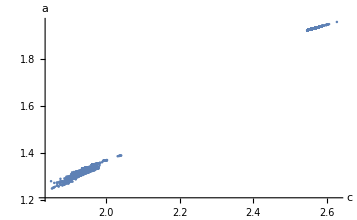

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@Select[su3nf6total,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],PlotRange->All,AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005]];
Show[p1]
```

```mathematica
Length[Select[su3nf6total,#["a"]>1.6&]]
```

23625

```mathematica
Length[Select[su3nf6total,#["a"]<1.6&]]
```

990

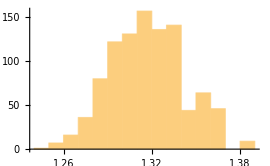

```mathematica
Histogram[#["a"]&/@Select[su3nf6total,#["a"]<1.6&],{0.01},PlotRange->Full]
```

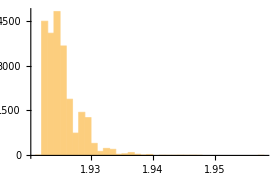

```mathematica
Histogram[#["a"]&/@Select[su3nf6total,#["a"]>1.6&],{0.001},PlotRange->Full]
```

```mathematica
data={#["c"],#["a"]}&/@Select[su3nf6total,#["a"]<1.6&];
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[-0.18225803868596429213+0.77518364487872474769 x]

```mathematica
{intercept, slope}=lm["BestFitParameters"]
```

{-0.18225803868596429213,0.77518364487872474769}

```mathematica
verticalDistances=lm["FitResiduals"];
```

```mathematica
orthogonalDistances=Map[Abs[#[[2]]-(slope*#[[1]]+intercept)]/Sqrt[slope^2+1]&,data];
```

```mathematica
binSize=0.0005
```

0.0005

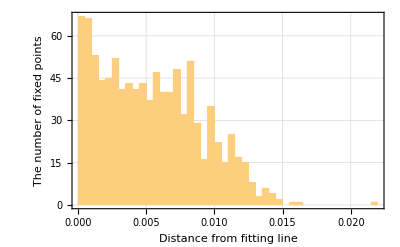

```mathematica
Histogram[orthogonalDistances,{binSize},PlotTheme->"Detailed",FrameLabel->{"Distance from fitting line","The number of fixed points"}]
```

```mathematica
data2={#["c"],#["a"]}&/@Select[su3nf6total,#["a"]>1.6&];
```

```mathematica
lm=LinearModelFit[data2,x,x]
```

FittedModel[0.82379079709316091728+0.43114533605611265338 x]

```mathematica
{intercept2, slope2}=lm["BestFitParameters"]
```

{0.82379079709316091728,0.43114533605611265338}

```mathematica
verticalDistances2=lm["FitResiduals"];
```

```mathematica
orthogonalDistances2=Map[Abs[#[[2]]-(slope2*#[[1]]+intercept2)]/Sqrt[slope2^2+1]&,data2];
```

```mathematica
binSize2=0.0000005
```

5.×10^-7

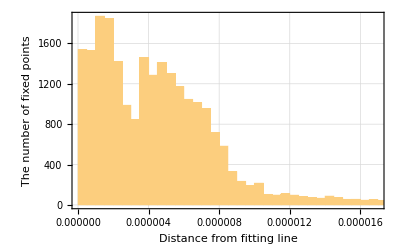

```mathematica
Histogram[orthogonalDistances2,{binSize2},PlotTheme->"Detailed",FrameLabel->{"Distance from fitting line","The number of fixed points"}]
```

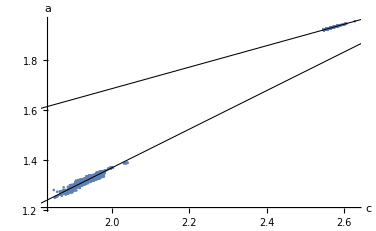

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@su3nf6total,PlotRange->All,AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005]];
p2=Plot[intercept2+slope2  x,{x,0,3},PlotStyle->{Black,Thickness->0.002}];
p3=Plot[intercept+slope  x,{x,0,3},PlotStyle->{Black,Thickness->0.002}];
Show[p1,p2,p3]
```

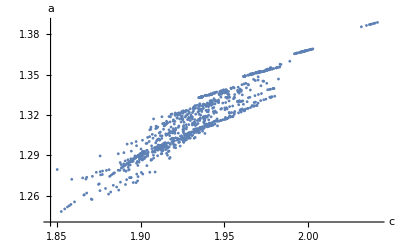

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@Select[su3nf6total,#["a"]<1.6&],PlotRange->All,AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005]];
p2=Plot[intercept+slope  x,{x,0,3},PlotStyle->{Black,Thickness->0.002}];
Show[p1]
```

### protected

```mathematica
su3nf6totalnoX=Select[su3nf6total,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&&#["consistency"]=="consistent"&];
```

```mathematica
su3Wgraph=toGlobalGraph[#["w"],#["n"][[2]]]&/@su3nf6totalnoX;
su2Wgraph=toGlobalGraph[#["w"],#["n"][[2]]]&/@total;
```

```mathematica
su2Wprotected=Select[total,MemberQ[su3Wgraph,toGlobalGraph[#["w"],#["n"][[2]]]]&];
%//Length
```

4158

```mathematica
su3Wprotected=Select[su3nf6totalnoX,MemberQ[su2Wgraph,toGlobalGraph[#["w"],#["n"][[2]]]]&];
%//Length
```

4158

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@Select[su2Wprotected,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],PlotRange->All,AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005],PlotRange->{{1.062,1.157},{0.75,0.792}}];
p2=ListPlot[{#["c"],#["a"]}&/@Select[Complement[total,su2Wprotected],!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->{PointSize[0.005],Red}];
Show[p1]
```

-Graphics-

```mathematica
p1=ListPlot[{#["c"],#["a"]}&/@Select[su3Wprotected,!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->PointSize[0.005],PlotRange->{{2.545,2.628},{1.921,1.958}}];
p2=ListPlot[{#["c"],#["a"]}&/@Select[Complement[su3nf6totalnoX,su3Wprotected],!AnyTrue[StringContainsQ[#,"X"]&/@#["w"],TrueQ]&],AxesLabel->{"c","a"},AxesStyle->Directive[{FontSize->14}],PlotStyle->{PointSize[0.005],Red},PlotRange->All];
Show[p1]
```

-Graphics-

```mathematica
Select[Complement[su3nf6totalnoX,su3Wprotected],#["c"]<2.5469&][[112]]
```

<|w→{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb2,q3*qb2,M3*q2*qb1},a→1.3385546140307950698,c→1.9497301582665615803,M1→1.1105956461138679159,M2→0.93369649717066913256,M3→1.1768991489431987834,q1→0.4487386226863189095,q2→0.38243511985698804206,q3→1.3824351198569880421,q4→0.38973721803669712484,q5→0.38973721803669712484,q6→0.38973721803669712484,qb1→0.44066573119981317457,qb2→0.61756488014301195794,qb3→0.38973721803669712484,qb4→0.38973721803669712484,qb5→0.38973721803669712484,qb6→0.38973721803669712484,consistency→consistent,global→<|M1→{1,1,1,0,-1,1,1,1,1},M2→{1,1,1,1,-2,1,1,1,1},M3→{0,0,0,-1,1,0,0,0,0},q1→{-1,-1,-1,-1,1,-1,-1,-1,-1},q2→{0,0,0,0,-1,0,0,0,0},q3→{0,0,0,0,-1,0,0,0,0},q4→{1,0,0,0,0,0,0,0,0},q5→{0,1,0,0,0,0,0,0,0},q6→{0,0,1,0,0,0,0,0,0},qb1→{0,0,0,1,0,0,0,0,0},qb2→{0,0,0,0,1,0,0,0,0},qb3→{0,0,0,0,0,1,0,0,0},qb4→{0,0,0,0,0,0,1,0,0},qb5→{0,0,0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,0,0,1}|>,rational→,n→{0,3,6,6,0,0,0,0,0},relevant→{M1,M2,M3,q1*qb3,q2*qb3,q3*qb1,q3*qb3,q4*qb1,q4*qb3,q1^2*qb1*qb3,q1*q2*qb1^2,q1*q4*qb1^2,q1^2*qb3^2,q1^2*qb3*qb4,q1*q2*qb3^2,q1*q2*qb3*qb4,q1*q4*qb3^2,q1*q4*qb3*qb4,q2^2*qb1*qb3,q2*q4*qb1^2,q2^2*qb3^2,q2^2*qb3*qb4,q2*q4*qb3^2,q2*q4*qb3*qb4,q4^2*qb1^2,q4^2*qb1*qb3,q4*q5*qb1^2,q4*q5*qb1*qb3,q4^2*qb3^2,q4^2*qb3*qb4,q4*q5*qb3*qb4,M1*q1*qb3,M1*q2*qb3,M1*q4*qb1,M1*q4*qb3,M2*q1*qb3,M2*q2*qb3,M2*q4*qb1,M2*q4*qb3,M2^2,M3*q2*qb3,M3*q4*qb3},flip→{M1,M2,M3,q1*qb3,q2*qb3,q4*qb1,q4*qb3}|>

```mathematica
FindCharges[2,{0,3,4,4,0,0,0,0,0},{"M1*q1*qb1","q2^2*qb2^2","M2*q1*qb2","q3*qb2","M3*q2*qb1"}]
```

<|w→{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb2,q3*qb2,M3*q2*qb1,q2*qb3*X1,q2*qb4*X2},a→0.23684833425881484985,c→0.4653528404505985334,X1→1.4276667611233189722,X2→1.4276667611233189722,M1→1.2442971893424115594,M2→0.84478596710259334974,M3→1.3995112222398182097,q1→0.40507918938392314138,q2→0.24986515648651649112,q3→1.2498651564865164911,q4→0.34949586807556599499,qb1→0.35062362127366529918,qb2→0.75013484351348350888,qb3→0.32246808239016453667,qb4→0.32246808239016453667,consistency→consistent,global→<|X1→{0,0,0,1,0},X2→{0,0,0,0,1},M1→{1,0,1,-1,0},M2→{1,1,0,-1,-1},M3→{0,-1,1,0,1},q1→{-1,-1,-1,1,0},q2→{0,0,-1,0,-1},q3→{0,0,-1,0,-1},q4→{1,0,0,0,0},qb1→{0,1,0,0,0},qb2→{0,0,1,0,1},qb3→{0,0,1,-1,1},qb4→{0,0,1,0,0}|>,rational→,n→{2,3,4,4,0,0,0,0,0},relevant→{M1,M2,M3,X1,q1*qb3,q3*qb1,q3*qb3,q4*qb1,q4*qb3,q1^2*qb1*qb3,q1*q2*qb1^2,q1*q4*qb1^2,q1^2*qb3^2,q1^2*qb3*qb4,q1*q2*qb3^2,q1*q4*qb3^2,q1*q4*qb3*qb4,q2^2*qb1*qb3,q2*q4*qb1^2,q2^2*qb3*qb4,q2*q4*qb3^2,q4^2*qb1^2,q4^2*qb1*qb3,q4^2*qb3^2,q4^2*qb3*qb4,M1*q1*qb3,M1*q4*qb1,M1*q4*qb3,M2*q1*qb3,M2*q4*qb1,M2*q4*qb3,M2*q2^2*qb3*qb4,M2^2},flip→{M1,M2,q1*qb3,q4*qb1,q4*qb3,q1*q2*qb3^2,q2^2*qb1*qb3,q2*q4*qb1^2,q2^2*qb3*qb4,q2*q4*qb3^2}|>

```mathematica
Sort[Differences[SortBy[{#["a"],#["c"]}&/@su3Wprotected,#[[1]]&]]][[1]]
Position[Differences[SortBy[{#["a"],#["c"]}&/@su3Wprotected,#[[1]]&]],{%[[1]],%[[2]]}]
```

{3.4×10^-17,2.11×10^-16}

{{3908}}

```mathematica
SortBy[su3Wprotected,#["a"]&][[3908]]["a"]
SortBy[su3Wprotected,#["a"]&][[3908]]["c"]
SortBy[su3Wprotected,#["a"]&][[3908]]["w"]
```

1.9336923360254912712

2.5742385278274092053

{M1*q1*qb1,q2^2*qb2*qb3,M2*q2*qb1,q1*q3*qb2*qb3,M3*q1*qb4}

```mathematica
SortBy[su3Wprotected,#["a"]&][[3909]]["a"]
SortBy[su3Wprotected,#["a"]&][[3909]]["c"]
SortBy[su3Wprotected,#["a"]&][[3909]]["w"]
```

1.9336923360254913053

2.5742385278274094164

{M1*q1*qb1,q2^2*qb2^2,M2*q1*qb2,q2^2*qb1*qb3,M3*q3*qb1}

```mathematica
Select[su3Wprotected,#["a"]==1.92557907068431444020021424192468181343`20.&]
```

{}

```mathematica
FindCharges[3,{0,3,6,6,0,0,0,0,0},{"M1*q1*qb1","q2^2*qb2*qb3","M2*q3*qb2","q2^2*qb3^2","M3*q2^2*"}]
```

<|w→{M1*q1*qb1,q2^2*qb2*qb3,M2*q3*qb2,q2^2*qb3^2},a→1.9255790706843144402,c→2.5555072711314834549,M1→0.95292443056541212614,M2→0.96822436227988363866,q1→0.52353778471729393693,q2→0.49218433956077073274,q3→0.52395997728088709407,q4→0.48685813214088262747,q5→0.48685813214088262747,q6→0.48685813214088262747,qb1→0.52353778471729393693,qb2→0.50781566043922926726,qb3→0.50781566043922926726,qb4→0.48685813214088262747,qb5→0.48685813214088262747,qb6→0.48685813214088262747,consistency→consistent,global→<|M1→{1,1,1,1,0,1,1,1,1},M2→{-1,0,0,0,0,-1,0,0,0},q1→{-1,-1,-1,-1,-1,-1,-1,-1,-1},q2→{0,0,0,0,0,-1,0,0,0},q3→{1,0,0,0,0,0,0,0,0},q4→{0,1,0,0,0,0,0,0,0},q5→{0,0,1,0,0,0,0,0,0},q6→{0,0,0,1,0,0,0,0,0},qb1→{0,0,0,0,1,0,0,0,0},qb2→{0,0,0,0,0,1,0,0,0},qb3→{0,0,0,0,0,1,0,0,0},qb4→{0,0,0,0,0,0,1,0,0},qb5→{0,0,0,0,0,0,0,1,0},qb6→{0,0,0,0,0,0,0,0,1}|>,rational→,n→{0,2,6,6,0,0,0,0,0},relevant→{M1,M2,q1*qb2,q1*qb3,q1*qb4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*qb1,q3*qb3,q3*qb4,q4*qb2,q4*qb3,q4*qb4,q1*q2*qb4^2,q1*q2*qb4*qb5,q1*q4*qb4^2,q1*q4*qb4*qb5,q2^2*qb1*qb4,q2^2*qb2*qb4,q2*q4*qb2^2,q2*q4*qb2*qb3,q2*q4*qb2*qb4,q2^2*qb3*qb4,q2*q4*qb3^2,q2*q4*qb3*qb4,q2^2*qb4^2,q2^2*qb4*qb5,q2*q3*qb4^2,q2*q3*qb4*qb5,q2*q4*qb4^2,q2*q4*qb4*qb5,q3*q4*qb4^2,q3*q4*qb4*qb5,q4^2*qb2^2,q4^2*qb2*qb3,q4^2*qb2*qb4,q4*q5*qb2^2,q4*q5*qb2*qb3,q4*q5*qb2*qb4,q4^2*qb3^2,q4^2*qb3*qb4,q4*q5*qb3^2,q4*q5*qb3*qb4,q4^2*qb4^2,q4^2*qb4*qb5,q4*q5*qb4*qb5,M1*q2*qb2,M1*q2*qb3,M1*q2*qb4,M1*q3*qb3,M1*q3*qb4,M1*q4*qb2,M1*q4*qb3,M1*q4*qb4,M1^2,M1*M2,M2*q1*qb3,M2*q1*qb4,M2*q2*qb1,M2*q2*qb3,M2*q2*qb4,M2*q3*qb4,M2*q4*qb3,M2*q4*qb4,M2^2},flip→{M1,M2,q1*qb2,q1*qb3,q1*qb4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*qb1,q3*qb3,q3*qb4,q4*qb2,q4*qb3,q4*qb4}|>

## Test

```mathematica
AbsoluteTiming[FindCharges[2,{0,3,4,4,0,0,0,0,0},{"M1*q2*q3","M2*q1*qb4","q4^2*qb1*qb2","M3*q1*q3","q3*qb1^2*qb2"}]]
```

{M1*q2*q3,M2*q1*qb4,q4^2*qb1*qb2,M3*q1*q3,q3*qb1^2*qb2}

5

Without Groebner basis

{0.,0.,0.,0.,0.}

{1.28472,<|w→{M1*q2*q3,M2*q1*qb4,q4^2*qb1*qb2,M3*q1*q3,q3*qb1^2*qb2},a→0.7581255366165672258,c→1.0812790195881863647,M1→0.95955608185862134624,M2→0.9636823655893823737,M3→0.90630582500609005792,q1→0.5447060791292975693,q2→0.49145582227676628098,q3→0.54898809586461237279,q4→0.51698045158980569494,qb1→0.48497280731499901709,qb2→0.48106628950538959302,qb3→0.44021889903780941487,qb4→0.49161155528132005701,consistency→consistent,global→<|M1→{-1,4,2,0,0},M2→{1,-3,-1,1,0},M3→{1,1,1,1,1},q1→{-1,3,1,-1,-1},q2→{1,0,0,0,0},q3→{0,-4,-2,0,0},q4→{0,-1,-1,0,0},qb1→{0,2,0,0,0},qb2→{0,0,2,0,0},qb3→{0,0,0,1,0},qb4→{0,0,0,0,1}|>,rational→,n→{0,3,4,4,0,0,0,0,0},relevant→{M1,M2,M3,q1*q2,q1*q4,q1*qb1,q1*qb2,q1*qb3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*q4,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb1,q4*qb2,q4*qb3,q4*qb4,qb1*qb2,qb1*qb3,qb1*qb4,qb2*qb3,qb2*qb4,qb3*qb4,q1*q2^2*qb3,q1*q2*q4*qb3,q1*q2*qb1*qb3,q1*q2*qb2*qb3,q1*q4*qb1*qb3,q1*q4*qb2*qb3,q1*qb1^2*qb2,q1*qb1^2*qb3,q1*qb1*qb2*qb3,q1*q2*qb2^2,q1*qb1*qb2^2,q1*qb2^2*qb3,q1^2*qb3^2,q1*q2*qb3^2,q1*q4*qb3^2,q1*qb1*qb3^2,q1*qb2*qb3^2,q1*qb3*qb4^2,q2^2*q3*qb3,q2^2*q4*qb1,q2^2*q4*qb2,q2^2*q4*qb3,q2^2*q4*qb4,q2*q4^2*qb3,q2*q4*qb1*qb2,q2*q4*qb1*qb3,q2*q4*qb1*qb4,q2*q4*qb2*qb3,q2*q4*qb2*qb4,q2*q4*qb3*qb4,q2^2*qb1^2,q2^2*qb1*qb2,q2^2*qb1*qb3,q2^2*qb1*qb4,q2*q4*qb1^2,q2*qb1^2*qb2,q2*qb1^2*qb3,q2*qb1^2*qb4,q2*qb1*qb2*qb3,q2*qb1*qb2*qb4,q2*qb1*qb3*qb4,q2^2*qb2^2,q2^2*qb2*qb3,q2^2*qb2*qb4,q2*q4*qb2^2,q2*qb1*qb2^2,q2*qb2^2*qb3,q2*qb2^2*qb4,q2*qb2*qb3*qb4,q2^2*qb3^2,q2^2*qb3*qb4,q2*q4*qb3^2,q2*qb1*qb3^2,q2*qb2*qb3^2,q2*qb3^2*qb4,q2^2*qb4^2,q2*q4*qb4^2,q2*qb1*qb4^2,q2*qb2*qb4^2,q2*qb3*qb4^2,q3*q4*qb1*qb3,q3*q4*qb2*qb3,q3*q4*qb3*qb4,q3*qb1^2*qb3,q3*qb1*qb2*qb3,q3*qb1*qb3*qb4,q3*qb1*qb2^2,q3*qb2^2*qb3,q3*qb2*qb3*qb4,q3^2*qb3^2,q3*q4*qb3^2,q3*qb1*qb3^2,q3*qb2*qb3^2,q3*qb3^2*qb4,q3*qb3*qb4^2,q4^2*qb1*qb3,q4*qb1^2*qb2,q4*qb1^2*qb3,q4*qb1^2*qb4,q4*qb1*qb2*qb3,q4*qb1*qb2*qb4,q4*qb1*qb3*qb4,q4^2*qb2^2,q4^2*qb2*qb3,q4*qb1*qb2^2,q4*qb2^2*qb3,q4*qb2^2*qb4,q4*qb2*qb3*qb4,q4^2*qb3^2,q4^2*qb3*qb4,q4*qb1*qb3^2,q4*qb2*qb3^2,q4*qb3^2*qb4,q4*qb1*qb4^2,q4*qb2*qb4^2,q4*qb3*qb4^2,qb1^2*qb2^2,qb1^2*qb2*qb3,qb1^2*qb2*qb4,qb1*qb2^2*qb3,qb1*qb2^2*qb4,qb1*qb2*qb3*qb4,qb1^2*qb3^2,qb1^2*qb3*qb4,qb1*qb2*qb3^2,qb1*qb3^2*qb4,qb1^2*qb4^2,qb1*qb2*qb4^2,qb1*qb3*qb4^2,qb2^2*qb3^2,qb2^2*qb3*qb4,qb2*qb3^2*qb4,qb2^2*qb4^2,qb2*qb3*qb4^2,qb3^2*qb4^2,M1*q1*q2,M1*q1*qb1,M1*q1*qb2,M1*q1*qb3,M1*q2*q4,M1*q2*qb1,M1*q2*qb2,M1*q2*qb3,M1*q2*qb4,M1*q4*qb1,M1*q4*qb2,M1*q4*qb3,M1*q4*qb4,M1*qb1*qb2,M1*qb1*qb3,M1*qb1*qb4,M1*qb2*qb3,M1*qb2*qb4,M1*qb3*qb4,M1^2,M1*M2,M1*M3,M2*q2*q4,M2*q2*qb1,M2*q2*qb2,M2*q2*qb3,M2*q2*qb4,M2*q3*qb1,M2*q3*qb2,M2*q3*qb3,M2*q4*qb1,M2*q4*qb2,M2*q4*qb3,M2*q4*qb4,M2*qb1*qb2,M2*qb1*qb3,M2*qb1*qb4,M2*qb2*qb3,M2*qb2*qb4,M2*qb3*qb4,M2^2,M2*M3,M3*q1*q2,M3*q1*q4,M3*q1*qb1,M3*q1*qb2,M3*q1*qb3,M3*q2*q4,M3*q2*qb1,M3*q2*qb2,M3*q2*qb3,M3*q2*qb4,M3*q3*q4,M3*q3*qb1,M3*q3*qb2,M3*q3*qb3,M3*q3*qb4,M3*q4*qb1,M3*q4*qb2,M3*q4*qb3,M3*q4*qb4,M3*qb1*qb2,M3*qb1*qb3,M3*qb1*qb4,M3*qb2*qb3,M3*qb2*qb4,M3*qb3*qb4,M3^2},flip→{M1,M2,M3,q1*q2,q1*q4,q1*qb1,q1*qb2,q1*qb3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*q4,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb1,q4*qb2,q4*qb3,q4*qb4,qb1*qb2,qb1*qb3,qb1*qb4,qb2*qb3,qb2*qb4,qb3*qb4},nsolve→exactly solved without Groebner|>}

```mathematica
AbsoluteTiming[ChargesGroebnerN[2,{0,3,4,4,0,0,0,0,0},{"M1*q2*q3","M2*q1*qb4","q4^2*qb1*qb2","M3*q1*q3","q3*qb1^2*qb2"}]]
```

{M1*q2*q3,M2*q1*qb4,q4^2*qb1*qb2,M3*q1*q3,q3*qb1^2*qb2}

5

{{q$442557[q2]→0.4914558222767662809763597343955755925720337852412,q$442557[qb1]→0.4849728073149990170940725740652254738389438663954,q$442557[qb2]→0.4810662895053895930241241322315009168461124047037,q$442557[qb3]→0.4402188990378094148747739222717314282273686690225,q$442557[qb4]→0.4916115552813200570053385500191370297034378434798}}

{0.,0.,0.,0.,0.}

{3.26268,<|w→{M1*q2*q3,M2*q1*qb4,q4^2*qb1*qb2,M3*q1*q3,q3*qb1^2*qb2},a→0.7581255366165672258,c→1.0812790195881863647,M1→0.95955608185862134624,M2→0.9636823655893823737,M3→0.90630582500609005792,q1→0.5447060791292975693,q2→0.49145582227676628098,q3→0.54898809586461237279,q4→0.51698045158980569494,qb1→0.48497280731499901709,qb2→0.48106628950538959302,qb3→0.44021889903780941487,qb4→0.49161155528132005701,consistency→consistent,global→<|M1→{-1,4,2,0,0},M2→{1,-3,-1,1,0},M3→{1,1,1,1,1},q1→{-1,3,1,-1,-1},q2→{1,0,0,0,0},q3→{0,-4,-2,0,0},q4→{0,-1,-1,0,0},qb1→{0,2,0,0,0},qb2→{0,0,2,0,0},qb3→{0,0,0,1,0},qb4→{0,0,0,0,1}|>,rational→,n→{0,3,4,4,0,0,0,0,0},relevant→{M1,M2,M3,q1*q2,q1*q4,q1*qb1,q1*qb2,q1*qb3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*q4,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb1,q4*qb2,q4*qb3,q4*qb4,qb1*qb2,qb1*qb3,qb1*qb4,qb2*qb3,qb2*qb4,qb3*qb4,q1*q2^2*qb3,q1*q2*q4*qb3,q1*q2*qb1*qb3,q1*q2*qb2*qb3,q1*q4*qb1*qb3,q1*q4*qb2*qb3,q1*qb1^2*qb2,q1*qb1^2*qb3,q1*qb1*qb2*qb3,q1*q2*qb2^2,q1*qb1*qb2^2,q1*qb2^2*qb3,q1^2*qb3^2,q1*q2*qb3^2,q1*q4*qb3^2,q1*qb1*qb3^2,q1*qb2*qb3^2,q1*qb3*qb4^2,q2^2*q3*qb3,q2^2*q4*qb1,q2^2*q4*qb2,q2^2*q4*qb3,q2^2*q4*qb4,q2*q4^2*qb3,q2*q4*qb1*qb2,q2*q4*qb1*qb3,q2*q4*qb1*qb4,q2*q4*qb2*qb3,q2*q4*qb2*qb4,q2*q4*qb3*qb4,q2^2*qb1^2,q2^2*qb1*qb2,q2^2*qb1*qb3,q2^2*qb1*qb4,q2*q4*qb1^2,q2*qb1^2*qb2,q2*qb1^2*qb3,q2*qb1^2*qb4,q2*qb1*qb2*qb3,q2*qb1*qb2*qb4,q2*qb1*qb3*qb4,q2^2*qb2^2,q2^2*qb2*qb3,q2^2*qb2*qb4,q2*q4*qb2^2,q2*qb1*qb2^2,q2*qb2^2*qb3,q2*qb2^2*qb4,q2*qb2*qb3*qb4,q2^2*qb3^2,q2^2*qb3*qb4,q2*q4*qb3^2,q2*qb1*qb3^2,q2*qb2*qb3^2,q2*qb3^2*qb4,q2^2*qb4^2,q2*q4*qb4^2,q2*qb1*qb4^2,q2*qb2*qb4^2,q2*qb3*qb4^2,q3*q4*qb1*qb3,q3*q4*qb2*qb3,q3*q4*qb3*qb4,q3*qb1^2*qb3,q3*qb1*qb2*qb3,q3*qb1*qb3*qb4,q3*qb1*qb2^2,q3*qb2^2*qb3,q3*qb2*qb3*qb4,q3^2*qb3^2,q3*q4*qb3^2,q3*qb1*qb3^2,q3*qb2*qb3^2,q3*qb3^2*qb4,q3*qb3*qb4^2,q4^2*qb1*qb3,q4*qb1^2*qb2,q4*qb1^2*qb3,q4*qb1^2*qb4,q4*qb1*qb2*qb3,q4*qb1*qb2*qb4,q4*qb1*qb3*qb4,q4^2*qb2^2,q4^2*qb2*qb3,q4*qb1*qb2^2,q4*qb2^2*qb3,q4*qb2^2*qb4,q4*qb2*qb3*qb4,q4^2*qb3^2,q4^2*qb3*qb4,q4*qb1*qb3^2,q4*qb2*qb3^2,q4*qb3^2*qb4,q4*qb1*qb4^2,q4*qb2*qb4^2,q4*qb3*qb4^2,qb1^2*qb2^2,qb1^2*qb2*qb3,qb1^2*qb2*qb4,qb1*qb2^2*qb3,qb1*qb2^2*qb4,qb1*qb2*qb3*qb4,qb1^2*qb3^2,qb1^2*qb3*qb4,qb1*qb2*qb3^2,qb1*qb3^2*qb4,qb1^2*qb4^2,qb1*qb2*qb4^2,qb1*qb3*qb4^2,qb2^2*qb3^2,qb2^2*qb3*qb4,qb2*qb3^2*qb4,qb2^2*qb4^2,qb2*qb3*qb4^2,qb3^2*qb4^2,M1*q1*q2,M1*q1*qb1,M1*q1*qb2,M1*q1*qb3,M1*q2*q4,M1*q2*qb1,M1*q2*qb2,M1*q2*qb3,M1*q2*qb4,M1*q4*qb1,M1*q4*qb2,M1*q4*qb3,M1*q4*qb4,M1*qb1*qb2,M1*qb1*qb3,M1*qb1*qb4,M1*qb2*qb3,M1*qb2*qb4,M1*qb3*qb4,M1^2,M1*M2,M1*M3,M2*q2*q4,M2*q2*qb1,M2*q2*qb2,M2*q2*qb3,M2*q2*qb4,M2*q3*qb1,M2*q3*qb2,M2*q3*qb3,M2*q4*qb1,M2*q4*qb2,M2*q4*qb3,M2*q4*qb4,M2*qb1*qb2,M2*qb1*qb3,M2*qb1*qb4,M2*qb2*qb3,M2*qb2*qb4,M2*qb3*qb4,M2^2,M2*M3,M3*q1*q2,M3*q1*q4,M3*q1*qb1,M3*q1*qb2,M3*q1*qb3,M3*q2*q4,M3*q2*qb1,M3*q2*qb2,M3*q2*qb3,M3*q2*qb4,M3*q3*q4,M3*q3*qb1,M3*q3*qb2,M3*q3*qb3,M3*q3*qb4,M3*q4*qb1,M3*q4*qb2,M3*q4*qb3,M3*q4*qb4,M3*qb1*qb2,M3*qb1*qb3,M3*qb1*qb4,M3*qb2*qb3,M3*qb2*qb4,M3*qb3*qb4,M3^2},flip→{M1,M2,M3,q1*q2,q1*q4,q1*qb1,q1*qb2,q1*qb3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*q4,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb1,q4*qb2,q4*qb3,q4*qb4,qb1*qb2,qb1*qb3,qb1*qb4,qb2*qb3,qb2*qb4,qb3*qb4},nsolve→exactly solved without Groebner|>}

```mathematica
AbsoluteTiming[Charges50[2,{0,3,4,4,0,0,0,0,0},{"M1*q2*q3","M2*q1*qb4","q4^2*qb1*qb2","M3*q1*q3","q3*qb1^2*qb2"}]]
```

{M1*q2*q3,M2*q1*qb4,q4^2*qb1*qb2,M3*q1*q3,q3*qb1^2*qb2}

5

Without Groebner basis

{0.,0.,0.,0.,0.}

{754.207,<|w→{M1*q2*q3,M2*q1*qb4,q4^2*qb1*qb2,M3*q1*q3,q3*qb1^2*qb2},a→0.7581255366165672258,c→1.0812790195881863647,M1→0.95955608185862134624,M2→0.9636823655893823737,M3→0.90630582500609005792,q1→0.5447060791292975693,q2→0.49145582227676628098,q3→0.54898809586461237279,q4→0.51698045158980569494,qb1→0.48497280731499901709,qb2→0.48106628950538959302,qb3→0.44021889903780941487,qb4→0.49161155528132005701,consistency→consistent,global→<|M1→{-1,4,2,0,0},M2→{1,-3,-1,1,0},M3→{1,1,1,1,1},q1→{-1,3,1,-1,-1},q2→{1,0,0,0,0},q3→{0,-4,-2,0,0},q4→{0,-1,-1,0,0},qb1→{0,2,0,0,0},qb2→{0,0,2,0,0},qb3→{0,0,0,1,0},qb4→{0,0,0,0,1}|>,rational→,n→{0,3,4,4,0,0,0,0,0},relevant→{M1,M2,M3,q1*q2,q1*q4,q1*qb1,q1*qb2,q1*qb3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*q4,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb1,q4*qb2,q4*qb3,q4*qb4,qb1*qb2,qb1*qb3,qb1*qb4,qb2*qb3,qb2*qb4,qb3*qb4,q1*q2^2*qb3,q1*q2*q4*qb3,q1*q2*qb1*qb3,q1*q2*qb2*qb3,q1*q4*qb1*qb3,q1*q4*qb2*qb3,q1*qb1^2*qb2,q1*qb1^2*qb3,q1*qb1*qb2*qb3,q1*q2*qb2^2,q1*qb1*qb2^2,q1*qb2^2*qb3,q1^2*qb3^2,q1*q2*qb3^2,q1*q4*qb3^2,q1*qb1*qb3^2,q1*qb2*qb3^2,q1*qb3*qb4^2,q2^2*q3*qb3,q2^2*q4*qb1,q2^2*q4*qb2,q2^2*q4*qb3,q2^2*q4*qb4,q2*q4^2*qb3,q2*q4*qb1*qb2,q2*q4*qb1*qb3,q2*q4*qb1*qb4,q2*q4*qb2*qb3,q2*q4*qb2*qb4,q2*q4*qb3*qb4,q2^2*qb1^2,q2^2*qb1*qb2,q2^2*qb1*qb3,q2^2*qb1*qb4,q2*q4*qb1^2,q2*qb1^2*qb2,q2*qb1^2*qb3,q2*qb1^2*qb4,q2*qb1*qb2*qb3,q2*qb1*qb2*qb4,q2*qb1*qb3*qb4,q2^2*qb2^2,q2^2*qb2*qb3,q2^2*qb2*qb4,q2*q4*qb2^2,q2*qb1*qb2^2,q2*qb2^2*qb3,q2*qb2^2*qb4,q2*qb2*qb3*qb4,q2^2*qb3^2,q2^2*qb3*qb4,q2*q4*qb3^2,q2*qb1*qb3^2,q2*qb2*qb3^2,q2*qb3^2*qb4,q2^2*qb4^2,q2*q4*qb4^2,q2*qb1*qb4^2,q2*qb2*qb4^2,q2*qb3*qb4^2,q3*q4*qb1*qb3,q3*q4*qb2*qb3,q3*q4*qb3*qb4,q3*qb1^2*qb3,q3*qb1*qb2*qb3,q3*qb1*qb3*qb4,q3*qb1*qb2^2,q3*qb2^2*qb3,q3*qb2*qb3*qb4,q3^2*qb3^2,q3*q4*qb3^2,q3*qb1*qb3^2,q3*qb2*qb3^2,q3*qb3^2*qb4,q3*qb3*qb4^2,q4^2*qb1*qb3,q4*qb1^2*qb2,q4*qb1^2*qb3,q4*qb1^2*qb4,q4*qb1*qb2*qb3,q4*qb1*qb2*qb4,q4*qb1*qb3*qb4,q4^2*qb2^2,q4^2*qb2*qb3,q4*qb1*qb2^2,q4*qb2^2*qb3,q4*qb2^2*qb4,q4*qb2*qb3*qb4,q4^2*qb3^2,q4^2*qb3*qb4,q4*qb1*qb3^2,q4*qb2*qb3^2,q4*qb3^2*qb4,q4*qb1*qb4^2,q4*qb2*qb4^2,q4*qb3*qb4^2,qb1^2*qb2^2,qb1^2*qb2*qb3,qb1^2*qb2*qb4,qb1*qb2^2*qb3,qb1*qb2^2*qb4,qb1*qb2*qb3*qb4,qb1^2*qb3^2,qb1^2*qb3*qb4,qb1*qb2*qb3^2,qb1*qb3^2*qb4,qb1^2*qb4^2,qb1*qb2*qb4^2,qb1*qb3*qb4^2,qb2^2*qb3^2,qb2^2*qb3*qb4,qb2*qb3^2*qb4,qb2^2*qb4^2,qb2*qb3*qb4^2,qb3^2*qb4^2,M1*q1*q2,M1*q1*qb1,M1*q1*qb2,M1*q1*qb3,M1*q2*q4,M1*q2*qb1,M1*q2*qb2,M1*q2*qb3,M1*q2*qb4,M1*q4*qb1,M1*q4*qb2,M1*q4*qb3,M1*q4*qb4,M1*qb1*qb2,M1*qb1*qb3,M1*qb1*qb4,M1*qb2*qb3,M1*qb2*qb4,M1*qb3*qb4,M1^2,M1*M2,M1*M3,M2*q2*q4,M2*q2*qb1,M2*q2*qb2,M2*q2*qb3,M2*q2*qb4,M2*q3*qb1,M2*q3*qb2,M2*q3*qb3,M2*q4*qb1,M2*q4*qb2,M2*q4*qb3,M2*q4*qb4,M2*qb1*qb2,M2*qb1*qb3,M2*qb1*qb4,M2*qb2*qb3,M2*qb2*qb4,M2*qb3*qb4,M2^2,M2*M3,M3*q1*q2,M3*q1*q4,M3*q1*qb1,M3*q1*qb2,M3*q1*qb3,M3*q2*q4,M3*q2*qb1,M3*q2*qb2,M3*q2*qb3,M3*q2*qb4,M3*q3*q4,M3*q3*qb1,M3*q3*qb2,M3*q3*qb3,M3*q3*qb4,M3*q4*qb1,M3*q4*qb2,M3*q4*qb3,M3*q4*qb4,M3*qb1*qb2,M3*qb1*qb3,M3*qb1*qb4,M3*qb2*qb3,M3*qb2*qb4,M3*qb3*qb4,M3^2},flip→{M1,M2,M3,q1*q2,q1*q4,q1*qb1,q1*qb2,q1*qb3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*q4,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb1,q4*qb2,q4*qb3,q4*qb4,qb1*qb2,qb1*qb3,qb1*qb4,qb2*qb3,qb2*qb4,qb3*qb4},nsolve→exactly solved without Groebner|>}

```mathematica
AbsoluteTiming[ChargesGroebner[2,{0,3,4,4,0,0,0,0,0},{"M1*q2*q3","M2*q1*qb4","q4^2*qb1*qb2","M3*q1*q3","q3*qb1^2*qb2"}]]
```

{M1*q2*q3,M2*q1*qb4,q4^2*qb1*qb2,M3*q1*q3,q3*qb1^2*qb2}

5

{0.,0.,0.,0.,0.}

{2.8708,<|w→{M1*q2*q3,M2*q1*qb4,q4^2*qb1*qb2,M3*q1*q3,q3*qb1^2*qb2},a→0.7581255366165672258,c→1.0812790195881863647,M1→0.95955608185862134624,M2→0.9636823655893823737,M3→0.90630582500609005792,q1→0.5447060791292975693,q2→0.49145582227676628098,q3→0.54898809586461237279,q4→0.51698045158980569494,qb1→0.48497280731499901709,qb2→0.48106628950538959302,qb3→0.44021889903780941487,qb4→0.49161155528132005701,consistency→consistent,global→<|M1→{-1,4,2,0,0},M2→{1,-3,-1,1,0},M3→{1,1,1,1,1},q1→{-1,3,1,-1,-1},q2→{1,0,0,0,0},q3→{0,-4,-2,0,0},q4→{0,-1,-1,0,0},qb1→{0,2,0,0,0},qb2→{0,0,2,0,0},qb3→{0,0,0,1,0},qb4→{0,0,0,0,1}|>,rational→,n→{0,3,4,4,0,0,0,0,0},relevant→{M1,M2,M3,q1*q2,q1*q4,q1*qb1,q1*qb2,q1*qb3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*q4,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb1,q4*qb2,q4*qb3,q4*qb4,qb1*qb2,qb1*qb3,qb1*qb4,qb2*qb3,qb2*qb4,qb3*qb4,q1*q2^2*qb3,q1*q2*q4*qb3,q1*q2*qb1*qb3,q1*q2*qb2*qb3,q1*q4*qb1*qb3,q1*q4*qb2*qb3,q1*qb1^2*qb2,q1*qb1^2*qb3,q1*qb1*qb2*qb3,q1*q2*qb2^2,q1*qb1*qb2^2,q1*qb2^2*qb3,q1^2*qb3^2,q1*q2*qb3^2,q1*q4*qb3^2,q1*qb1*qb3^2,q1*qb2*qb3^2,q1*qb3*qb4^2,q2^2*q3*qb3,q2^2*q4*qb1,q2^2*q4*qb2,q2^2*q4*qb3,q2^2*q4*qb4,q2*q4^2*qb3,q2*q4*qb1*qb2,q2*q4*qb1*qb3,q2*q4*qb1*qb4,q2*q4*qb2*qb3,q2*q4*qb2*qb4,q2*q4*qb3*qb4,q2^2*qb1^2,q2^2*qb1*qb2,q2^2*qb1*qb3,q2^2*qb1*qb4,q2*q4*qb1^2,q2*qb1^2*qb2,q2*qb1^2*qb3,q2*qb1^2*qb4,q2*qb1*qb2*qb3,q2*qb1*qb2*qb4,q2*qb1*qb3*qb4,q2^2*qb2^2,q2^2*qb2*qb3,q2^2*qb2*qb4,q2*q4*qb2^2,q2*qb1*qb2^2,q2*qb2^2*qb3,q2*qb2^2*qb4,q2*qb2*qb3*qb4,q2^2*qb3^2,q2^2*qb3*qb4,q2*q4*qb3^2,q2*qb1*qb3^2,q2*qb2*qb3^2,q2*qb3^2*qb4,q2^2*qb4^2,q2*q4*qb4^2,q2*qb1*qb4^2,q2*qb2*qb4^2,q2*qb3*qb4^2,q3*q4*qb1*qb3,q3*q4*qb2*qb3,q3*q4*qb3*qb4,q3*qb1^2*qb3,q3*qb1*qb2*qb3,q3*qb1*qb3*qb4,q3*qb1*qb2^2,q3*qb2^2*qb3,q3*qb2*qb3*qb4,q3^2*qb3^2,q3*q4*qb3^2,q3*qb1*qb3^2,q3*qb2*qb3^2,q3*qb3^2*qb4,q3*qb3*qb4^2,q4^2*qb1*qb3,q4*qb1^2*qb2,q4*qb1^2*qb3,q4*qb1^2*qb4,q4*qb1*qb2*qb3,q4*qb1*qb2*qb4,q4*qb1*qb3*qb4,q4^2*qb2^2,q4^2*qb2*qb3,q4*qb1*qb2^2,q4*qb2^2*qb3,q4*qb2^2*qb4,q4*qb2*qb3*qb4,q4^2*qb3^2,q4^2*qb3*qb4,q4*qb1*qb3^2,q4*qb2*qb3^2,q4*qb3^2*qb4,q4*qb1*qb4^2,q4*qb2*qb4^2,q4*qb3*qb4^2,qb1^2*qb2^2,qb1^2*qb2*qb3,qb1^2*qb2*qb4,qb1*qb2^2*qb3,qb1*qb2^2*qb4,qb1*qb2*qb3*qb4,qb1^2*qb3^2,qb1^2*qb3*qb4,qb1*qb2*qb3^2,qb1*qb3^2*qb4,qb1^2*qb4^2,qb1*qb2*qb4^2,qb1*qb3*qb4^2,qb2^2*qb3^2,qb2^2*qb3*qb4,qb2*qb3^2*qb4,qb2^2*qb4^2,qb2*qb3*qb4^2,qb3^2*qb4^2,M1*q1*q2,M1*q1*qb1,M1*q1*qb2,M1*q1*qb3,M1*q2*q4,M1*q2*qb1,M1*q2*qb2,M1*q2*qb3,M1*q2*qb4,M1*q4*qb1,M1*q4*qb2,M1*q4*qb3,M1*q4*qb4,M1*qb1*qb2,M1*qb1*qb3,M1*qb1*qb4,M1*qb2*qb3,M1*qb2*qb4,M1*qb3*qb4,M1^2,M1*M2,M1*M3,M2*q2*q4,M2*q2*qb1,M2*q2*qb2,M2*q2*qb3,M2*q2*qb4,M2*q3*qb1,M2*q3*qb2,M2*q3*qb3,M2*q4*qb1,M2*q4*qb2,M2*q4*qb3,M2*q4*qb4,M2*qb1*qb2,M2*qb1*qb3,M2*qb1*qb4,M2*qb2*qb3,M2*qb2*qb4,M2*qb3*qb4,M2^2,M2*M3,M3*q1*q2,M3*q1*q4,M3*q1*qb1,M3*q1*qb2,M3*q1*qb3,M3*q2*q4,M3*q2*qb1,M3*q2*qb2,M3*q2*qb3,M3*q2*qb4,M3*q3*q4,M3*q3*qb1,M3*q3*qb2,M3*q3*qb3,M3*q3*qb4,M3*q4*qb1,M3*q4*qb2,M3*q4*qb3,M3*q4*qb4,M3*qb1*qb2,M3*qb1*qb3,M3*qb1*qb4,M3*qb2*qb3,M3*qb2*qb4,M3*qb3*qb4,M3^2},flip→{M1,M2,M3,q1*q2,q1*q4,q1*qb1,q1*qb2,q1*qb3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*q4,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb1,q4*qb2,q4*qb3,q4*qb4,qb1*qb2,qb1*qb3,qb1*qb4,qb2*qb3,qb2*qb4,qb3*qb4},nsolve→exactly solved without Groebner|>}

```mathematica
AbsoluteTiming[ChargesWrong[2,{0,3,4,4,0,0,0,0,0},{"M1*q2*q3","M2*q1*qb4","q4^2*qb1*qb2","M3*q1*q3","q3*qb1^2*qb2"}]]
```

{M1*q2*q3,M2*q1*qb4,q4^2*qb1*qb2,M3*q1*q3,q3*qb1^2*qb2}

5

Without Groebner basis

{0.,0.,0.,0.,0.}

{760.25,<|w→{M1*q2*q3,M2*q1*qb4,q4^2*qb1*qb2,M3*q1*q3,q3*qb1^2*qb2},a→0.850304,c→1.20417,M1→0.95955608185862134624,M2→0.9636823655893823737,M3→0.90630582500609005792,q1→0.5447060791292975693,q2→0.49145582227676628098,q3→0.54898809586461237279,q4→0.51698045158980569494,qb1→0.48497280731499901709,qb2→0.48106628950538959302,qb3→0.44021889903780941487,qb4→0.49161155528132005701,consistency→consistent,global→<|M1→{-1,4,2,0,0},M2→{1,-3,-1,1,0},M3→{1,1,1,1,1},q1→{-1,3,1,-1,-1},q2→{1,0,0,0,0},q3→{0,-4,-2,0,0},q4→{0,-1,-1,0,0},qb1→{0,2,0,0,0},qb2→{0,0,2,0,0},qb3→{0,0,0,1,0},qb4→{0,0,0,0,1}|>,rational→,n→{0,3,4,4,0,0,0,0,0},relevant→{M1,M2,M3,q1*q2,q1*q4,q1*qb1,q1*qb2,q1*qb3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*q4,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb1,q4*qb2,q4*qb3,q4*qb4,qb1*qb2,qb1*qb3,qb1*qb4,qb2*qb3,qb2*qb4,qb3*qb4,q1*q2^2*qb3,q1*q2*q4*qb3,q1*q2*qb1*qb3,q1*q2*qb2*qb3,q1*q4*qb1*qb3,q1*q4*qb2*qb3,q1*qb1^2*qb2,q1*qb1^2*qb3,q1*qb1*qb2*qb3,q1*q2*qb2^2,q1*qb1*qb2^2,q1*qb2^2*qb3,q1^2*qb3^2,q1*q2*qb3^2,q1*q4*qb3^2,q1*qb1*qb3^2,q1*qb2*qb3^2,q1*qb3*qb4^2,q2^2*q3*qb3,q2^2*q4*qb1,q2^2*q4*qb2,q2^2*q4*qb3,q2^2*q4*qb4,q2*q4^2*qb3,q2*q4*qb1*qb2,q2*q4*qb1*qb3,q2*q4*qb1*qb4,q2*q4*qb2*qb3,q2*q4*qb2*qb4,q2*q4*qb3*qb4,q2^2*qb1^2,q2^2*qb1*qb2,q2^2*qb1*qb3,q2^2*qb1*qb4,q2*q4*qb1^2,q2*qb1^2*qb2,q2*qb1^2*qb3,q2*qb1^2*qb4,q2*qb1*qb2*qb3,q2*qb1*qb2*qb4,q2*qb1*qb3*qb4,q2^2*qb2^2,q2^2*qb2*qb3,q2^2*qb2*qb4,q2*q4*qb2^2,q2*qb1*qb2^2,q2*qb2^2*qb3,q2*qb2^2*qb4,q2*qb2*qb3*qb4,q2^2*qb3^2,q2^2*qb3*qb4,q2*q4*qb3^2,q2*qb1*qb3^2,q2*qb2*qb3^2,q2*qb3^2*qb4,q2^2*qb4^2,q2*q4*qb4^2,q2*qb1*qb4^2,q2*qb2*qb4^2,q2*qb3*qb4^2,q3*q4*qb1*qb3,q3*q4*qb2*qb3,q3*q4*qb3*qb4,q3*qb1^2*qb3,q3*qb1*qb2*qb3,q3*qb1*qb3*qb4,q3*qb1*qb2^2,q3*qb2^2*qb3,q3*qb2*qb3*qb4,q3^2*qb3^2,q3*q4*qb3^2,q3*qb1*qb3^2,q3*qb2*qb3^2,q3*qb3^2*qb4,q3*qb3*qb4^2,q4^2*qb1*qb3,q4*qb1^2*qb2,q4*qb1^2*qb3,q4*qb1^2*qb4,q4*qb1*qb2*qb3,q4*qb1*qb2*qb4,q4*qb1*qb3*qb4,q4^2*qb2^2,q4^2*qb2*qb3,q4*qb1*qb2^2,q4*qb2^2*qb3,q4*qb2^2*qb4,q4*qb2*qb3*qb4,q4^2*qb3^2,q4^2*qb3*qb4,q4*qb1*qb3^2,q4*qb2*qb3^2,q4*qb3^2*qb4,q4*qb1*qb4^2,q4*qb2*qb4^2,q4*qb3*qb4^2,qb1^2*qb2^2,qb1^2*qb2*qb3,qb1^2*qb2*qb4,qb1*qb2^2*qb3,qb1*qb2^2*qb4,qb1*qb2*qb3*qb4,qb1^2*qb3^2,qb1^2*qb3*qb4,qb1*qb2*qb3^2,qb1*qb3^2*qb4,qb1^2*qb4^2,qb1*qb2*qb4^2,qb1*qb3*qb4^2,qb2^2*qb3^2,qb2^2*qb3*qb4,qb2*qb3^2*qb4,qb2^2*qb4^2,qb2*qb3*qb4^2,qb3^2*qb4^2,M1*q1*q2,M1*q1*qb1,M1*q1*qb2,M1*q1*qb3,M1*q2*q4,M1*q2*qb1,M1*q2*qb2,M1*q2*qb3,M1*q2*qb4,M1*q4*qb1,M1*q4*qb2,M1*q4*qb3,M1*q4*qb4,M1*qb1*qb2,M1*qb1*qb3,M1*qb1*qb4,M1*qb2*qb3,M1*qb2*qb4,M1*qb3*qb4,M1^2,M1*M2,M1*M3,M2*q2*q4,M2*q2*qb1,M2*q2*qb2,M2*q2*qb3,M2*q2*qb4,M2*q3*qb1,M2*q3*qb2,M2*q3*qb3,M2*q4*qb1,M2*q4*qb2,M2*q4*qb3,M2*q4*qb4,M2*qb1*qb2,M2*qb1*qb3,M2*qb1*qb4,M2*qb2*qb3,M2*qb2*qb4,M2*qb3*qb4,M2^2,M2*M3,M3*q1*q2,M3*q1*q4,M3*q1*qb1,M3*q1*qb2,M3*q1*qb3,M3*q2*q4,M3*q2*qb1,M3*q2*qb2,M3*q2*qb3,M3*q2*qb4,M3*q3*q4,M3*q3*qb1,M3*q3*qb2,M3*q3*qb3,M3*q3*qb4,M3*q4*qb1,M3*q4*qb2,M3*q4*qb3,M3*q4*qb4,M3*qb1*qb2,M3*qb1*qb3,M3*qb1*qb4,M3*qb2*qb3,M3*qb2*qb4,M3*qb3*qb4,M3^2},flip→{M1,M2,M3,q1*q2,q1*q4,q1*qb1,q1*qb2,q1*qb3,q2*q4,q2*qb1,q2*qb2,q2*qb3,q2*qb4,q3*q4,q3*qb1,q3*qb2,q3*qb3,q3*qb4,q4*qb1,q4*qb2,q4*qb3,q4*qb4,qb1*qb2,qb1*qb3,qb1*qb4,qb2*qb3,qb2*qb4,qb3*qb4},nsolve→exactly solved without Groebner|>}

```mathematica
0.7581255366165672258047127587307005438`20.
```

```mathematica
0.7581255366165672258047127587307005438`20.
```

```mathematica
0.7581255366165672258047127587307005438`20.
```

```mathematica
0.7581255366165672258047127587307005438`20.
```

```mathematica
AbsoluteTiming[FindCharges[2,{0,3,4,4,0,0,0,0,0},{"M1*q2*q3","M2*q1*qb4","M3*q2*qb4"}]]
```

{M1*q2*q3,M2*q1*qb4,M3*q2*qb4}

7

Without Groebner basis

{0.,0.,0.,0.,0.,0.,0.}

{8.3227,<|w→{M1*q2*q3,M2*q1*qb4,M3*q2*qb4},a→0.7635601577909270217,c→1.0936883629191321499,M1→0.92307692307692307692,M2→0.92307692307692307692,M3→0.87179487179487179487,q1→0.51282051282051282051,q2→0.56410256410256410256,q3→0.51282051282051282051,q4→0.46153846153846153846,qb1→0.46153846153846153846,qb2→0.46153846153846153846,qb3→0.46153846153846153846,qb4→0.56410256410256410256,consistency→consistent,global→<|M1→{-1,-1,0,0,0,0,0},M2→{1,1,1,1,1,1,0},M3→{-1,0,0,0,0,0,-1},q1→{-1,-1,-1,-1,-1,-1,-1},q2→{1,0,0,0,0,0,0},q3→{0,1,0,0,0,0,0},q4→{0,0,1,0,0,0,0},qb1→{0,0,0,1,0,0,0},qb2→{0,0,0,0,1,0,0},qb3→{0,0,0,0,0,1,0},qb4→{0,0,0,0,0,0,1}|>,rational→<|a→3097/4056,c→1109/1014,M1→12/13,M2→12/13,M3→34/39,q1→20/39,q2→22/39,q3→20/39,q4→6/13,qb1→6/13,qb2→6/13,qb3→6/13,qb4→22/39|>,n→{0,3,4,4,0,0,0,0,0},relevant→{M1,M3,q1*q2,q1*q3,q1*q4,q2*q4,q4*qb1,q1*q3*q4*qb1,q1^2*q4^2,q1^2*q4*qb1,q1*q3*q4^2,q1*q4^2*qb1,q1*q4*qb1*qb2,q2*q4^2*qb1,q2*q4*qb1*qb2,q4^2*qb1^2,q4^2*qb1*qb2,q4*qb1*qb2*qb3,M1*q1*q3,M1*q1*q4,M1*q3*q4,M1*q4*qb1,M1*q4*qb4,M1^2,M1*M2,M1*M3,M3*q1*q2,M3*q1*q3,M3*q1*q4,M3*q2*q4,M3*q4*qb1,M3^2},flip→{M1,M3,q1*q2,q1*q3,q1*q4,q2*q4,q4*qb1},nsolve→exactly solved without Groebner|>}

```mathematica
AbsoluteTiming[FindCharges[2,{0,3,4,4,0,0,0,0,0},{"M1*q2*q3","M2*q1*qb4","M3*q2*qb4"}]]
```

{8.32572,<|w→{M1*q2*q3,M2*q1*qb4,M3*q2*qb4},a→0.7635601577909270217,c→1.0936883629191321499,M1→0.92307692307692307692,M2→0.92307692307692307692,M3→0.87179487179487179487,q1→0.51282051282051282051,q2→0.56410256410256410256,q3→0.51282051282051282051,q4→0.46153846153846153846,qb1→0.46153846153846153846,qb2→0.46153846153846153846,qb3→0.46153846153846153846,qb4→0.56410256410256410256,consistency→consistent,global→<|M1→{-1,-1,0,0,0,0,0},M2→{1,1,1,1,1,1,0},M3→{-1,0,0,0,0,0,-1},q1→{-1,-1,-1,-1,-1,-1,-1},q2→{1,0,0,0,0,0,0},q3→{0,1,0,0,0,0,0},q4→{0,0,1,0,0,0,0},qb1→{0,0,0,1,0,0,0},qb2→{0,0,0,0,1,0,0},qb3→{0,0,0,0,0,1,0},qb4→{0,0,0,0,0,0,1}|>,rational→<|a→3097/4056,c→1109/1014,M1→12/13,M2→12/13,M3→34/39,q1→20/39,q2→22/39,q3→20/39,q4→6/13,qb1→6/13,qb2→6/13,qb3→6/13,qb4→22/39|>,n→{0,3,4,4,0,0,0,0,0},relevant→{M1,M3,q1*q2,q1*q3,q1*q4,q2*q4,q4*qb1,q1*q3*q4*qb1,q1^2*q4^2,q1^2*q4*qb1,q1*q3*q4^2,q1*q4^2*qb1,q1*q4*qb1*qb2,q2*q4^2*qb1,q2*q4*qb1*qb2,q4^2*qb1^2,q4^2*qb1*qb2,q4*qb1*qb2*qb3,M1*q1*q3,M1*q1*q4,M1*q3*q4,M1*q4*qb1,M1*q4*qb4,M1^2,M1*M2,M1*M3,M3*q1*q2,M3*q1*q3,M3*q1*q4,M3*q2*q4,M3*q4*qb1,M3^2},flip→{M1,M3,q1*q2,q1*q3,q1*q4,q2*q4,q4*qb1}|>}